### Variando b0, y tomando b1,b2=1.5 b0

```mathematica
Quit[]
```

```mathematica
(* Ecuaciones Utilez *)
angu2[δ_,ϕ2_,b1_,b3_, Λ_,G_,M_,c_]:=((4 G M)/c^2  (-Cos[ϕ2]/b1+(Cos[δ+ϕ2]+Sin[δ])/b3)+1/6 (G M)/c^2  Λ ((2 b1)/(-1+Cos[ϕ2])-4 (b1-b3 Cos[δ]) Cos[ϕ2]-(2 b3)/(1+Cos[δ+ϕ2])+b3 Csc[(δ+ϕ2)/2]^2+b1 Sec[ϕ2/2]^2+4 b3 (Sin[δ]-Sin[δ] Sin[ϕ2]+Sec[δ] Tan[δ]))+1/36 (G M)/c^2  Λ^2 (b1^3 (-7+Cos[2 ϕ2]) Cot[ϕ2]^3 Csc[ϕ2]+b3^3 (-((-7+Cos[2 (δ+ϕ2)]) Cot[δ+ϕ2]^3 Csc[δ+ϕ2])+(7+Cos[2 δ]) Sec[δ] Tan[δ]^3)))+(-1/(4 b1^2 b3^2)(G^2 M^2)/c^4 (-15 b1^2 π+15 b3^2 π+30 b1^2 ϕ2-30 b3^2 ϕ2+b1^2 Sin[2 δ]-b3^2 Sin[2 ϕ2]+b1^2 Sin[2 (δ+ϕ2)])+1/384 (G^2 M^2)/c^4 Λ^2 (2 b1^2 (-30 π+60 ϕ2+97 Cot[ϕ2]) Csc[ϕ2]^4+62 b1^2 Cos[3 ϕ2] Csc[ϕ2]^5+b3^2 (12 (5 (π-2 (δ+ϕ2))-11 Cot[δ+ϕ2]) Csc[δ+ϕ2]^4+2 Sec[δ]^5 (60 δ Cos[δ]-97 Sin[δ]+31 Sin[3 δ])-31 Csc[δ+ϕ2]^6 Sin[4 (δ+ϕ2)]))+1/24 (G^2 M^2)/c^4 Λ (-15 π Csc[ϕ2]^2+30 ϕ2 Csc[ϕ2]^2+Cot[ϕ2] (-30+32 Csc[ϕ2]^2)+15 π Csc[δ+ϕ2]^2-30 δ Csc[δ+ϕ2]^2-30 ϕ2 Csc[δ+ϕ2]^2+Cot[δ+ϕ2] (30-32 Csc[δ+ϕ2]^2)+30 δ Sec[δ]^2-2 Sin[2 δ]+2 Sin[2 ϕ2]-2 Sin[2 (δ+ϕ2)]+30 Tan[δ]-32 Sec[δ]^2 Tan[δ])); (*Solución serie*)

Eq=-1-(Λ̄)/3+u[ϕ]^2-Rs u[ϕ]^3+u'[ϕ]^2==0;(*Ecuación de la geodésica*)

Ang[ϕ_,Rs_,Lb_]:=ArcTan[-(u[ϕ] √(1-Lb/(3 u[ϕ]^2)-Rs u[ϕ]))/u'[ϕ]]; 
(*conversión coordenadas*)
xf[ϕ_]:=Cos[ϕ]/u[ϕ];
yf[ϕ_]:=Sin[ϕ]/u[ϕ];
```

```mathematica
(*Cantidades Físicas, Tomando una Masa solar*)
Λf =0*1.1056 10^-52;(*m^-2*)
Msun=1.9885*10^30;(*kg*)
Rsun=6.96*10^8;(*m*)
Gf=6.674*10^-11;(*m^3 kg^-1 s^-2*)
c=299792458;(*m/s*)
M=Msun;
M2=0;
RSch=2Gf M/c^2 ;(*Sch radio -> m*)
RSchF=2Gf M2/c^2;
```

```mathematica
a=1.5; (*factor multiplicativo para d2, d3*)
```

```mathematica
b0val={5,5.8,7,9,10,11,14,15,20,30,40,50,60,80,100,150,200,300,500,1000,5000,10000,20000,40000,80000,100000,150000,200000,250000,500000,750000,10^6}; (*235672,*)(*valores del parámtro de impacto b0*)
```

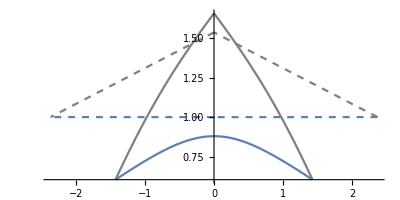

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

posición b2, b3{{ϕ→0.917951}}{ϕ→2.22364}0.4

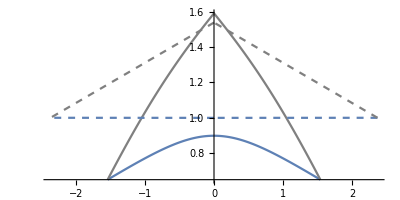

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

posición b2, b3{{ϕ→1.03201}}{ϕ→2.10958}0.4

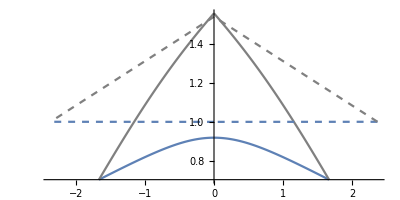

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve::ifun will be suppressed during this calculation.

posición b2, b3{{ϕ→1.11937}}{ϕ→2.02223}0.4

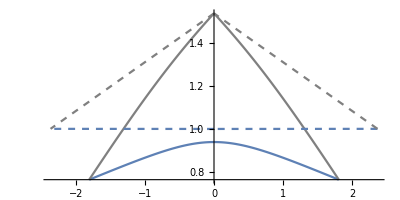

posición b2, b3{{ϕ→1.19046}}{ϕ→1.95113}0.4

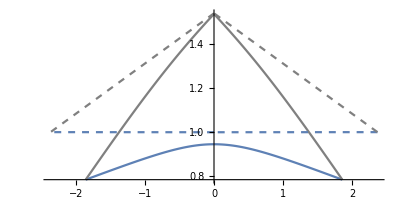

posición b2, b3{{ϕ→1.21147}}{ϕ→1.93013}0.4

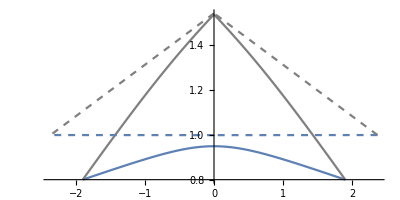

posición b2, b3{{ϕ→1.22746}}{ϕ→1.91413}0.4

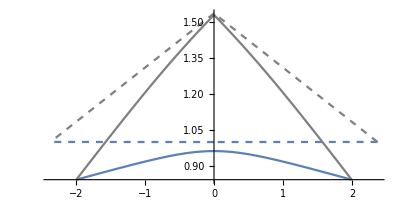

posición b2, b3{{ϕ→1.25868}}{ϕ→1.88291}0.4

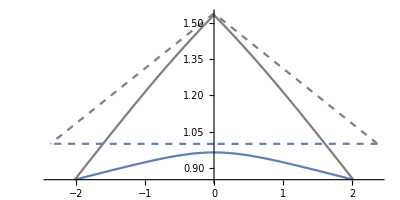

posición b2, b3{{ϕ→1.26575}}{ϕ→1.87584}0.4

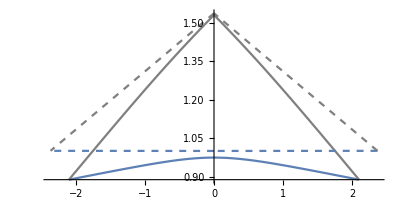

posición b2, b3{{ϕ→1.28898}}{ϕ→1.85262}0.4

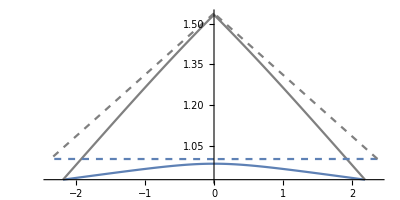

posición b2, b3{{ϕ→1.3101}}{ϕ→1.83149}0.4

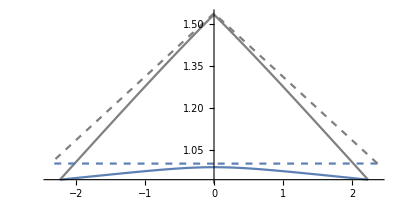

posición b2, b3{{ϕ→1.32002}}{ϕ→1.82157}0.4

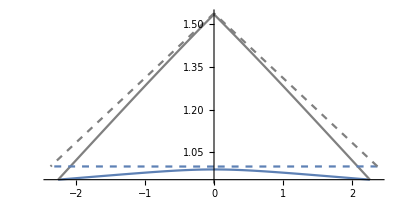

posición b2, b3{{ϕ→1.32575}}{ϕ→1.81584}0.4

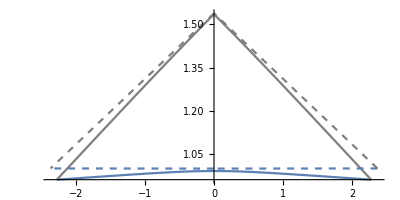

posición b2, b3{{ϕ→1.32949}}{ϕ→1.8121}0.4

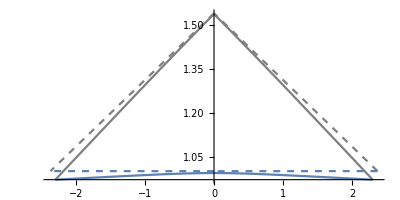

posición b2, b3{{ϕ→1.33408}}{ϕ→1.80752}0.4

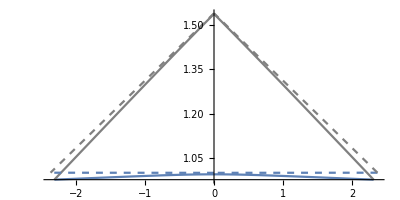

posición b2, b3{{ϕ→1.33679}}{ϕ→1.8048}0.4

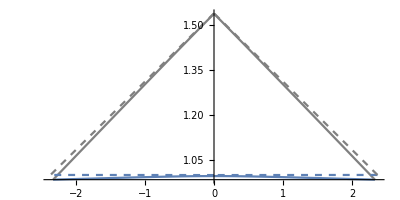

posición b2, b3{{ϕ→1.34035}}{ϕ→1.80125}0.4

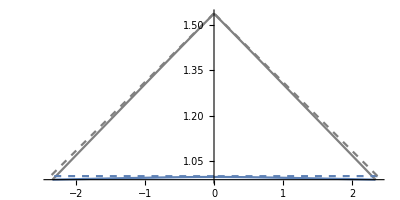

posición b2, b3{{ϕ→1.34211}}{ϕ→1.79948}0.4

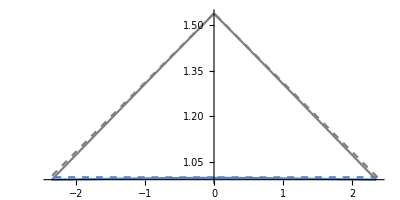

posición b2, b3{{ϕ→1.34385}}{ϕ→1.79774}0.4

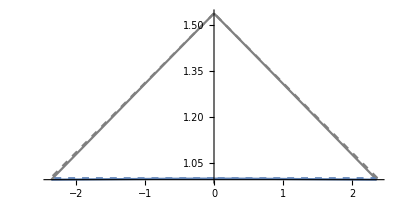

posición b2, b3{{ϕ→1.34524}}{ϕ→1.79635}0.4

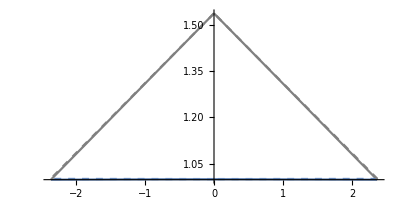

posición b2, b3{{ϕ→1.34627}}{ϕ→1.79533}0.4

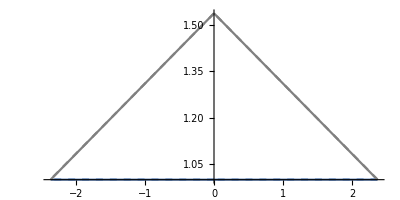

posición b2, b3{{ϕ→1.34709}}{ϕ→1.7945}0.4

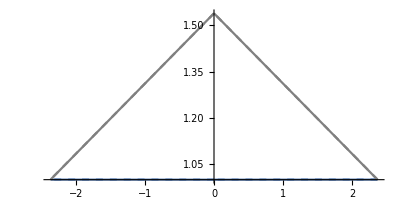

posición b2, b3{{ϕ→1.34719}}{ϕ→1.7944}0.4

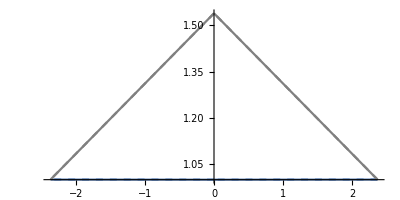

posición b2, b3{{ϕ→1.34724}}{ϕ→1.79435}0.4

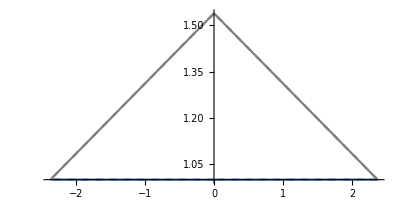

posición b2, b3{{ϕ→1.34727}}{ϕ→1.79432}0.4

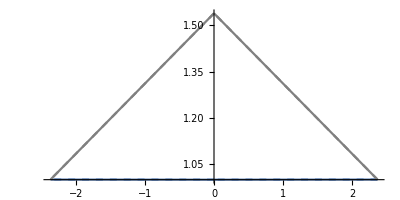

posición b2, b3{{ϕ→1.34728}}{ϕ→1.79431}0.4

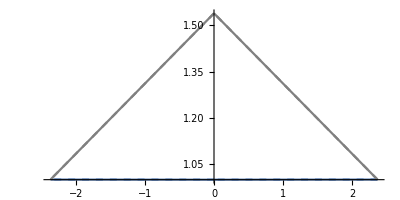

posición b2, b3{{ϕ→1.34729}}{ϕ→1.79431}0.4

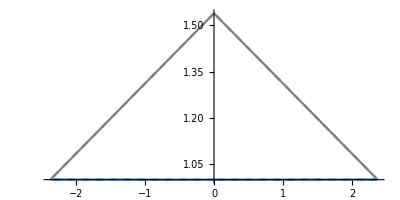

posición b2, b3{{ϕ→1.34729}}{ϕ→1.7943}0.4

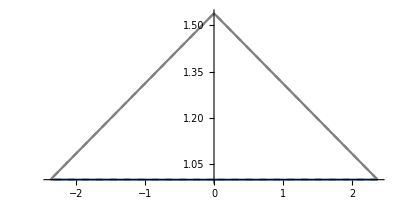

posición b2, b3{{ϕ→1.34729}}{ϕ→1.7943}0.4

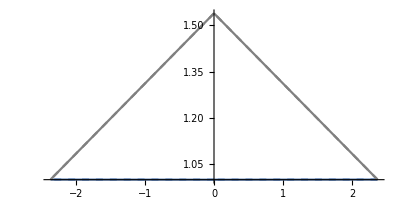

posición b2, b3{{ϕ→1.34729}}{ϕ→1.7943}0.4

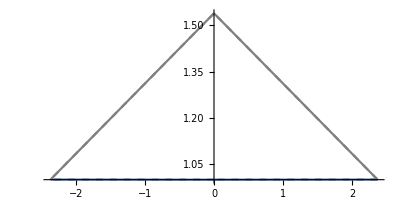

posición b2, b3{{ϕ→1.34729}}{ϕ→1.7943}0.4

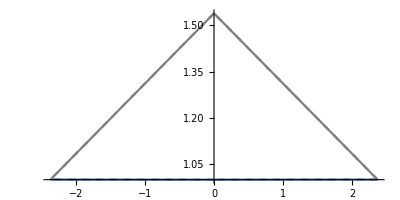

posición b2, b3{{ϕ→1.34729}}{ϕ→1.7943}0.4

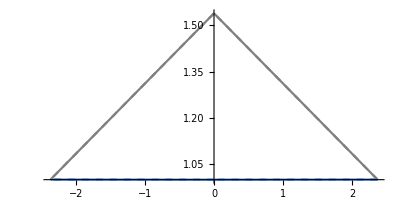

posición b2, b3{{ϕ→1.3473}}{ϕ→1.7943}0.4

```mathematica
DatAngN={};
DatAngSe={};
DataTriang={};
DataTriangFond={};
Do[
b=b0val[[i]];

(*C1*)
b0 =b*RSch;(*m*)
Rsval1=RSch/b0;(*Rs=rs/b*)
Rsval1F=RSchF/b0;(*Rs=rs/b*)
Lval1=Λf*b0^2; (*Λ̄ = Λ b^2 -> *)
ϕMin1=0.4;
ϕMax1=π-ϕMin1;
δval=0;

(*Geodesic C1*)(*Print["c1"];*)

(*Metrica*)
sol1=NDSolve[{Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1[[1]];
sol12=NDSolve[{Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]; (*[π/2, ϕMax]*)

(*Fondo*)
sol1F=NDSolve[({Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1F[[1]];
sol12F=NDSolve[({Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Geodesic C2*)(*Print["c2"];*)
b1 =a*b0;(*m*)
Rsval2=RSch/b1;(*Rs=rs/b*)
Rsval2F=RSchF/b1;
Lval2=Λf*b1^2; (*Λ̄ = Λ b^2 -> *)
ϕMin2=ϕMin1;
ϕMax2=π/2;

(*Metrica*)
temp=(u[ϕMin2]*b1/b0)/.sol1[[1]];
sol2=NDSolve[{Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2},{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)

(*Fondo*)
temp=(u[ϕMin2]*b1/b0)/.sol1F[[1]];
sol2F=NDSolve[({Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2F}),{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];

(*Geodesic C2*)(*Print["c3"];*)
b2 =a*b0;(*m*)
Rsval3=RSch/b2;(*Rs=rs/b*)
Rsval3F=RSchF/b2;
Lval3=Λf*b2^2; (*Λ̄ = Λ b^2 -> *)
ϕMin3=ϕMax2;
ϕMax3=ϕMax1;

(*Metrica*)
temp=(u[ϕMax3]*b2/b0)/.sol12[[1]];
sol3=NDSolve[{Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3},{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Fondo*)
temp=(u[ϕMax3]*b2/b0)/.sol12F[[1]];
sol3F=NDSolve[({Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3F}),{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Construyendo tríangulos*)
DatTr={};
DatTrF={{},{},{}};
C1ϕvalor=Subdivide[ϕMin1,ϕMax1, 1000];
C2ϕvalor=Subdivide[ϕMin2,ϕMax2, 1000];
C3ϕvalor=Subdivide[ϕMin3,ϕMax3, 1000];
Do[
AppendTo[DatTr,{C1ϕvalor[[i]],
			    If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1[[1]],xf[C1ϕvalor[[i]]]/.sol12[[1]]], 
			    If[C1ϕvalor[[i]]<=π/2,yf[C1ϕvalor[[i]]]/.sol1[[1]],yf[C1ϕvalor[[i]]]/.sol12[[1]]],
			    C2ϕvalor[[i]],
			    b1/b0*xf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    b1/b0*yf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    C3ϕvalor[[i]],
			    b2/b0*xf[C3ϕvalor[[i]]]/.sol3[[1]],
			    b2/b0*yf[C3ϕvalor[[i]]]/.sol3[[1]]}];

(*Fondo*)
AppendTo[DatTrF,{C1ϕvalor[[i]],
			       If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1F[[1]],xf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      If[C1ϕvalor[[i]]<=π/2, yf[C1ϕvalor[[i]]]/.sol1F[[1]], yf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      C2ϕvalor[[i]],
			      b1/b0*xf[C2ϕvalor[[i]]]/.sol2F[[1]],
			      b1/b0*yf[C2ϕvalor[[i]]]/.sol2F[[1]],C3ϕvalor[[i]],
			      b2/b0*xf[C3ϕvalor[[i]]]/.sol3F[[1]], 
			      b2/b0*yf[C3ϕvalor[[i]]]/.sol3F[[1]]}];
,{i,1,Length[C1ϕvalor]}];

(*Graficandolos*)

Pc1=ParametricPlot[{xf[ϕ]/.sol1[[1]],yf[ϕ]/.sol1[[1]]},{ϕ,ϕMin1,π/2}, PlotRange->All,AspectRatio->0.5];
Pc12=ParametricPlot[{xf[ϕ]/.sol12[[1]],yf[ϕ]/.sol12[[1]]},{ϕ,π/2,ϕMax1}, PlotRange->All,AspectRatio->0.5];
Pc2=ParametricPlot[{b1/b0*xf[ϕ]/.sol2[[1]],b1/b0*yf[ϕ]/.sol2[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->Gray,AspectRatio->1];
Pc3=ParametricPlot[{b2/b0*xf[ϕ]/.sol3[[1]],b2/b0*yf[ϕ]/.sol3[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->Gray,AspectRatio->1];

Pc1F=ParametricPlot[{xf[ϕ]/.sol1F[[1]],yf[ϕ]/.sol1F[[1]]},{ϕ,ϕMin1,π/2}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc12F=ParametricPlot[{xf[ϕ]/.sol12F[[1]],yf[ϕ]/.sol12F[[1]]},{ϕ,π/2,ϕMax1}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc2F=ParametricPlot[{b1/b0*xf[ϕ]/.sol2F[[1]],b1/b0*yf[ϕ]/.sol2F[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];
Pc3F=ParametricPlot[{b2/b0*xf[ϕ]/.sol3F[[1]],b2/b0*yf[ϕ]/.sol3F[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];

Print[Show[{Pc1,Pc12,Pc2, Pc3,Pc1F,Pc12F,Pc2F,Pc3F},PlotRange->All]];

(*Calculando angulos*)
ptos={ϕMax1,π/2,ϕMin1};
(*C1*)
angC1 = Last[{Ang[ptos[[1]],Rsval1,Lval1]/.sol12,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1];
angC1F = Last[{Ang[ptos[[1]],Rsval1F,Lval1]/.sol12F,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1F];
(*C2*)
angC2= Last[{Ang[ptos[[-1]],Rsval2,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2];
angC2F = Last[{Ang[ptos[[-1]],Rsval2F,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2F];
(*C3*)
angC3= Last[{Ang[ptos[[2]],Rsval3,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3];
angC3F = Last[{Ang[ptos[[2]],Rsval3F,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3F];
(*Betas*)
betas = {angC3[[2]]-angC1[[1]], angC1[[2]]-angC2[[1]],-angC3[[1]]+angC2[[2]]};
betasF = {angC3F[[2]]-angC1F[[1]], angC1F[[2]]-angC2F[[1]],-angC3F[[1]]+angC2F[[2]]};

(*Serie*)
delI=NSolve[(u'[ϕ]/.sol2[[1]])==0,ϕ];
delI2=FindRoot[(u'[ϕ]/.sol3[[1]])==0,{ϕ,ϕMax3}];
Print["posición b2, b3",delI,delI2, ϕMin1];
delt=π/2-ϕ/.delI;
ASer=Last@angu2[delt,ϕMin1,b0,b2, Λf,Gf,M,c];

(*Salvando*)
AppendTo[DataTriang,DatTr];
AppendTo[DataTriangFond,DatTrF];
AppendTo[DatAngN,{b,Abs[Last@Total[betas-betasF]]}];
AppendTo[DatAngSe,{b,Abs@ASer}],
{i, 1,Length[b0val]}
]
```

```mathematica
{b0val[[1]],b0val[[2]],b0val[[5]],b0val[[9]], b0val[[13]],b0val[[15]]}
```

{5,5.8,10,20,60,100}

```mathematica
Export["dataTriang1.dat", DataTriang[[1]]]
Export["dataTriang2.dat", DataTriang[[2]]]
Export["dataTriang3.dat", DataTriang[[5]]]
Export["dataTriang4.dat", DataTriang[[9]]]
Export["dataTriang5.dat", DataTriang[[13]]]
Export["dataTriang6.dat", DataTriang[[15]]]

Export["dataTriangFond.dat", DataTriangFond[[1]]]
Export["dataAngMathe.dat", DatAngN]
Export["dataAngSerMathe.dat", DatAngSe]
```

dataTriang1.dat

dataTriang2.dat

dataTriang3.dat

dataTriang4.dat

dataTriang5.dat

dataTriang6.dat

dataTriangFond.dat

dataAngMathe.dat

dataAngSerMathe.dat

```mathematica
DatAngSe
```

```mathematica
test={{5,0.12342906870490923},{5.8,0.10028137674999425},{7,0.07953959451727165},{9,0.05947970730077122},{10,0.05282729467161078},{11,0.04750680896324011},{14,0.03645838970288432},{15,0.033829081363716124},{20,0.024845929718657612},{30,0.016207200442734795},{40,0.012020014684652441},{50,0.009550277500712129},{60,0.007921847569761947},{80,0.0059067803971905196},{100,0.004708778562580526},{150,0.003124277669429392},{200,0.0023376196199371216},{300,0.0015546602259185228},{500,0.0009309984323992022},{1000,0.0004648206477714773},{5000,0.00009285581089947493},{10000,0.00004642113097874102},{20000,0.000023208871753293882},{40000,0.000011604012424395954},{80000,5.801898692234569*^-6},{100000,4.641502492386169*^-6},{150000,3.094320252066326*^-6},{200000,2.320734625064432*^-6},{250000,1.8565850202810921*^-6},{500000,9.282898201952285*^-7},{750000,6.188592803566809*^-7},{1000000,4.6414423506881363*^-7}};
```

```mathematica
test-DatAngSe
```

{{0,0.},{0.,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.}}

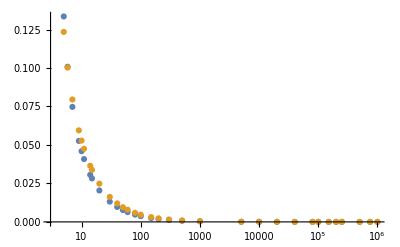

-Graphics-

```mathematica
ListLogLinearPlot[{DatAngN,DatAngSe}]
```

### Variando b0, y tomando b1,b2=1.5 b0

```mathematica
Quit[]
```

```mathematica
(* Ecuaciones Utilez *)
angu2[δ_,ϕ2_,b1_,b3_, Λ_,G_,M_,c_]:=((4 G M)/c^2  (-Cos[ϕ2]/b1+(Cos[δ+ϕ2]+Sin[δ])/b3)+1/6 (G M)/c^2  Λ ((2 b1)/(-1+Cos[ϕ2])-4 (b1-b3 Cos[δ]) Cos[ϕ2]-(2 b3)/(1+Cos[δ+ϕ2])+b3 Csc[(δ+ϕ2)/2]^2+b1 Sec[ϕ2/2]^2+4 b3 (Sin[δ]-Sin[δ] Sin[ϕ2]+Sec[δ] Tan[δ]))+1/36 (G M)/c^2  Λ^2 (b1^3 (-7+Cos[2 ϕ2]) Cot[ϕ2]^3 Csc[ϕ2]+b3^3 (-((-7+Cos[2 (δ+ϕ2)]) Cot[δ+ϕ2]^3 Csc[δ+ϕ2])+(7+Cos[2 δ]) Sec[δ] Tan[δ]^3)))+(-1/(4 b1^2 b3^2)(G^2 M^2)/c^4 (-15 b1^2 π+15 b3^2 π+30 b1^2 ϕ2-30 b3^2 ϕ2+b1^2 Sin[2 δ]-b3^2 Sin[2 ϕ2]+b1^2 Sin[2 (δ+ϕ2)])+1/384 (G^2 M^2)/c^4 Λ^2 (2 b1^2 (-30 π+60 ϕ2+97 Cot[ϕ2]) Csc[ϕ2]^4+62 b1^2 Cos[3 ϕ2] Csc[ϕ2]^5+b3^2 (12 (5 (π-2 (δ+ϕ2))-11 Cot[δ+ϕ2]) Csc[δ+ϕ2]^4+2 Sec[δ]^5 (60 δ Cos[δ]-97 Sin[δ]+31 Sin[3 δ])-31 Csc[δ+ϕ2]^6 Sin[4 (δ+ϕ2)]))+1/24 (G^2 M^2)/c^4 Λ (-15 π Csc[ϕ2]^2+30 ϕ2 Csc[ϕ2]^2+Cot[ϕ2] (-30+32 Csc[ϕ2]^2)+15 π Csc[δ+ϕ2]^2-30 δ Csc[δ+ϕ2]^2-30 ϕ2 Csc[δ+ϕ2]^2+Cot[δ+ϕ2] (30-32 Csc[δ+ϕ2]^2)+30 δ Sec[δ]^2-2 Sin[2 δ]+2 Sin[2 ϕ2]-2 Sin[2 (δ+ϕ2)]+30 Tan[δ]-32 Sec[δ]^2 Tan[δ])); (*Solución serie*)

Eq=-1-(Λ̄)/3+u[ϕ]^2-Rs u[ϕ]^3+u'[ϕ]^2==0;(*Ecuación de la geodésica*)

Ang[ϕ_,Rs_,Lb_]:=ArcTan[-(u[ϕ] √(1-Lb/(3 u[ϕ]^2)-Rs u[ϕ]))/u'[ϕ]]; 
(*conversión coordenadas*)
xf[ϕ_]:=Cos[ϕ]/u[ϕ];
yf[ϕ_]:=Sin[ϕ]/u[ϕ];
```

```mathematica
(*Cantidades Físicas, Tomando una Masa solar*)
Λf =1.1056 10^-52;(*m^-2*)
Msun=1.9885*10^30;(*kg*)
Rsun=6.96*10^8;(*m*)
Gf=6.674*10^-11;(*m^3 kg^-1 s^-2*)
c=299792458;(*m/s*)
M=10^(12)*Msun;
M2=0;
RSch=2Gf M/c^2 ;(*Sch radio -> m*)
RSchF=2Gf M2/c^2;
```

```mathematica
a=1.5; (*factor multiplicativo para d2, d3*)
```

```mathematica
b0val={5,5.8,7,9,10,11,14,15,20,30,40,50,60,80,100,150,200,300,500,1000,5000,10000,20000,40000,80000,100000,150000,200000,250000,500000,750000,10^6}; (*235672,*)(*valores del parámtro de impacto b0*)
```

```mathematica
DatAngN={};
DatAngSe={};
DataTriang={};
DataTriangFond={};
Do[
b=b0val[[i]];

(*C1*)
b0 =b*RSch;(*m*)
Rsval1=RSch/b0;(*Rs=rs/b*)
Rsval1F=RSchF/b0;(*Rs=rs/b*)
Lval1=Λf*b0^2; (*Λ̄ = Λ b^2 -> *)
ϕMin1=0.4;
ϕMax1=π-ϕMin1;
δval=0;

(*Geodesic C1*)(*Print["c1"];*)

(*Metrica*)
sol1=NDSolve[{Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1[[1]];
sol12=NDSolve[{Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]; (*[π/2, ϕMax]*)

(*Fondo*)
sol1F=NDSolve[({Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1F[[1]];
sol12F=NDSolve[({Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Geodesic C2*)(*Print["c2"];*)
b1 =a*b0;(*m*)
Rsval2=RSch/b1;(*Rs=rs/b*)
Rsval2F=RSchF/b1;
Lval2=Λf*b1^2; (*Λ̄ = Λ b^2 -> *)
ϕMin2=ϕMin1;
ϕMax2=π/2;

(*Metrica*)
temp=(u[ϕMin2]*b1/b0)/.sol1[[1]];
sol2=NDSolve[{Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2},{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)

(*Fondo*)
temp=(u[ϕMin2]*b1/b0)/.sol1F[[1]];
sol2F=NDSolve[({Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2F}),{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];

(*Geodesic C2*)(*Print["c3"];*)
b2 =a*b0;(*m*)
Rsval3=RSch/b2;(*Rs=rs/b*)
Rsval3F=RSchF/b2;
Lval3=Λf*b2^2; (*Λ̄ = Λ b^2 -> *)
ϕMin3=ϕMax2;
ϕMax3=ϕMax1;

(*Metrica*)
temp=(u[ϕMax3]*b2/b0)/.sol12[[1]];
sol3=NDSolve[{Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3},{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Fondo*)
temp=(u[ϕMax3]*b2/b0)/.sol12F[[1]];
sol3F=NDSolve[({Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3F}),{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Construyendo tríangulos*)
DatTr={};
DatTrF={{},{},{}};
C1ϕvalor=Subdivide[ϕMin1,ϕMax1, 1000];
C2ϕvalor=Subdivide[ϕMin2,ϕMax2, 1000];
C3ϕvalor=Subdivide[ϕMin3,ϕMax3, 1000];
Do[
AppendTo[DatTr,{C1ϕvalor[[i]],
			    If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1[[1]],xf[C1ϕvalor[[i]]]/.sol12[[1]]], 
			    If[C1ϕvalor[[i]]<=π/2,yf[C1ϕvalor[[i]]]/.sol1[[1]],yf[C1ϕvalor[[i]]]/.sol12[[1]]],
			    C2ϕvalor[[i]],
			    b1/b0*xf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    b1/b0*yf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    C3ϕvalor[[i]],
			    b2/b0*xf[C3ϕvalor[[i]]]/.sol3[[1]],
			    b2/b0*yf[C3ϕvalor[[i]]]/.sol3[[1]]}];

(*Fondo*)
AppendTo[DatTrF,{C1ϕvalor[[i]],
			       If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1F[[1]],xf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      If[C1ϕvalor[[i]]<=π/2, yf[C1ϕvalor[[i]]]/.sol1F[[1]], yf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      C2ϕvalor[[i]],
			      b1/b0*xf[C2ϕvalor[[i]]]/.sol2F[[1]],
			      b1/b0*yf[C2ϕvalor[[i]]]/.sol2F[[1]],C3ϕvalor[[i]],
			      b2/b0*xf[C3ϕvalor[[i]]]/.sol3F[[1]], 
			      b2/b0*yf[C3ϕvalor[[i]]]/.sol3F[[1]]}];
,{i,1,Length[C1ϕvalor]}];

(*Graficandolos*)

Pc1=ParametricPlot[{xf[ϕ]/.sol1[[1]],yf[ϕ]/.sol1[[1]]},{ϕ,ϕMin1,π/2}, PlotRange->All,AspectRatio->0.5];
Pc12=ParametricPlot[{xf[ϕ]/.sol12[[1]],yf[ϕ]/.sol12[[1]]},{ϕ,π/2,ϕMax1}, PlotRange->All,AspectRatio->0.5];
Pc2=ParametricPlot[{b1/b0*xf[ϕ]/.sol2[[1]],b1/b0*yf[ϕ]/.sol2[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->Gray,AspectRatio->1];
Pc3=ParametricPlot[{b2/b0*xf[ϕ]/.sol3[[1]],b2/b0*yf[ϕ]/.sol3[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->Gray,AspectRatio->1];

Pc1F=ParametricPlot[{xf[ϕ]/.sol1F[[1]],yf[ϕ]/.sol1F[[1]]},{ϕ,ϕMin1,π/2}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc12F=ParametricPlot[{xf[ϕ]/.sol12F[[1]],yf[ϕ]/.sol12F[[1]]},{ϕ,π/2,ϕMax1}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc2F=ParametricPlot[{b1/b0*xf[ϕ]/.sol2F[[1]],b1/b0*yf[ϕ]/.sol2F[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];
Pc3F=ParametricPlot[{b2/b0*xf[ϕ]/.sol3F[[1]],b2/b0*yf[ϕ]/.sol3F[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];

Print[Show[{Pc1,Pc12,Pc2, Pc3,Pc1F,Pc12F,Pc2F,Pc3F},PlotRange->All]];

(*Calculando angulos*)
ptos={ϕMax1,π/2,ϕMin1};
(*C1*)
angC1 = Last[{Ang[ptos[[1]],Rsval1,Lval1]/.sol12,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1];
angC1F = Last[{Ang[ptos[[1]],Rsval1F,Lval1]/.sol12F,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1F];
(*C2*)
angC2= Last[{Ang[ptos[[-1]],Rsval2,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2];
angC2F = Last[{Ang[ptos[[-1]],Rsval2F,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2F];
(*C3*)
angC3= Last[{Ang[ptos[[2]],Rsval3,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3];
angC3F = Last[{Ang[ptos[[2]],Rsval3F,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3F];
(*Betas*)
betas = {angC3[[2]]-angC1[[1]], angC1[[2]]-angC2[[1]],-angC3[[1]]+angC2[[2]]};
betasF = {angC3F[[2]]-angC1F[[1]], angC1F[[2]]-angC2F[[1]],-angC3F[[1]]+angC2F[[2]]};

(*Serie*)
delI=NSolve[(u'[ϕ]/.sol2[[1]])==0,ϕ];
delI2=FindRoot[(u'[ϕ]/.sol3[[1]])==0,{ϕ,ϕMax3}];
Print["posición b2, b3",delI,delI2, ϕMin1];
delt=π/2-ϕ/.delI;
ASer=Last@angu2[delt,ϕMin1,b0,b2, Λf,Gf,M,c];

(*Salvando*)
AppendTo[DataTriang,DatTr];
AppendTo[DataTriangFond,DatTrF];
AppendTo[DatAngN,{b,Abs[Last@Total[betas-betasF]]}];
AppendTo[DatAngSe,{b,Abs@ASer}],
{i, 1,Length[b0val]}
]
```

-Graphics-

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

posición b2, b3{{ϕ→0.917951}}{ϕ→2.22364}0.4

-Graphics-

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

posición b2, b3{{ϕ→1.03201}}{ϕ→2.10958}0.4

-Graphics-

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve::ifun will be suppressed during this calculation.

posición b2, b3{{ϕ→1.11937}}{ϕ→2.02223}0.4

-Graphics-

posición b2, b3{{ϕ→1.19046}}{ϕ→1.95113}0.4

-Graphics-

posición b2, b3{{ϕ→1.21147}}{ϕ→1.93013}0.4

-Graphics-

posición b2, b3{{ϕ→1.22746}}{ϕ→1.91413}0.4

-Graphics-

posición b2, b3{{ϕ→1.25868}}{ϕ→1.88291}0.4

-Graphics-

posición b2, b3{{ϕ→1.26575}}{ϕ→1.87584}0.4

-Graphics-

posición b2, b3{{ϕ→1.28898}}{ϕ→1.85262}0.4

-Graphics-

posición b2, b3{{ϕ→1.3101}}{ϕ→1.83149}0.4

-Graphics-

posición b2, b3{{ϕ→1.32002}}{ϕ→1.82157}0.4

-Graphics-

posición b2, b3{{ϕ→1.32575}}{ϕ→1.81584}0.4

-Graphics-

posición b2, b3{{ϕ→1.32949}}{ϕ→1.8121}0.4

-Graphics-

posición b2, b3{{ϕ→1.33408}}{ϕ→1.80752}0.4

-Graphics-

posición b2, b3{{ϕ→1.33679}}{ϕ→1.8048}0.4

-Graphics-

posición b2, b3{{ϕ→1.34035}}{ϕ→1.80125}0.4

```mathematica
{b0val[[1]],b0val[[2]],b0val[[5]],b0val[[9]], b0val[[13]],b0val[[15]]}
```

{5,5.8,10,20,60,100}

```mathematica
Export["dataTriang1.dat", DataTriang[[1]]]
Export["dataTriang2.dat", DataTriang[[2]]]
Export["dataTriang3.dat", DataTriang[[5]]]
Export["dataTriang4.dat", DataTriang[[9]]]
Export["dataTriang5.dat", DataTriang[[13]]]
Export["dataTriang6.dat", DataTriang[[15]]]

Export["dataTriangFond.dat", DataTriangFond[[1]]]
Export["dataAngMathe.dat", DatAngN]
Export["dataAngSerMathe.dat", DatAngSe]
```

dataTriang1.dat

dataTriang2.dat

dataTriang3.dat

dataTriang4.dat

dataTriang5.dat

dataTriang6.dat

dataTriangFond.dat

dataAngMathe.dat

dataAngSerMathe.dat

```mathematica
ListLogLinearPlot[{DatAngN,DatAngSe}]
```

-Graphics-

### Variando b2 caso 1, b0=1Radio del Sol

```mathematica
(*Variando b2*)
```

```mathematica
Quit[]
```

```mathematica
(* Ecuaciones Utilez *)
angu2[δ_,ϕ2_,b1_,b3_, Λ_,G_,M_,c_]:=((4 G M)/c^2  (-Cos[ϕ2]/b1+(Cos[δ+ϕ2]+Sin[δ])/b3)+1/6 (G M)/c^2  Λ ((2 b1)/(-1+Cos[ϕ2])-4 (b1-b3 Cos[δ]) Cos[ϕ2]-(2 b3)/(1+Cos[δ+ϕ2])+b3 Csc[(δ+ϕ2)/2]^2+b1 Sec[ϕ2/2]^2+4 b3 (Sin[δ]-Sin[δ] Sin[ϕ2]+Sec[δ] Tan[δ]))+1/36 (G M)/c^2  Λ^2 (b1^3 (-7+Cos[2 ϕ2]) Cot[ϕ2]^3 Csc[ϕ2]+b3^3 (-((-7+Cos[2 (δ+ϕ2)]) Cot[δ+ϕ2]^3 Csc[δ+ϕ2])+(7+Cos[2 δ]) Sec[δ] Tan[δ]^3)))+(-1/(4 b1^2 b3^2)(G^2 M^2)/c^4 (-15 b1^2 π+15 b3^2 π+30 b1^2 ϕ2-30 b3^2 ϕ2+b1^2 Sin[2 δ]-b3^2 Sin[2 ϕ2]+b1^2 Sin[2 (δ+ϕ2)])+1/384 (G^2 M^2)/c^4 Λ^2 (2 b1^2 (-30 π+60 ϕ2+97 Cot[ϕ2]) Csc[ϕ2]^4+62 b1^2 Cos[3 ϕ2] Csc[ϕ2]^5+b3^2 (12 (5 (π-2 (δ+ϕ2))-11 Cot[δ+ϕ2]) Csc[δ+ϕ2]^4+2 Sec[δ]^5 (60 δ Cos[δ]-97 Sin[δ]+31 Sin[3 δ])-31 Csc[δ+ϕ2]^6 Sin[4 (δ+ϕ2)]))+1/24 (G^2 M^2)/c^4 Λ (-15 π Csc[ϕ2]^2+30 ϕ2 Csc[ϕ2]^2+Cot[ϕ2] (-30+32 Csc[ϕ2]^2)+15 π Csc[δ+ϕ2]^2-30 δ Csc[δ+ϕ2]^2-30 ϕ2 Csc[δ+ϕ2]^2+Cot[δ+ϕ2] (30-32 Csc[δ+ϕ2]^2)+30 δ Sec[δ]^2-2 Sin[2 δ]+2 Sin[2 ϕ2]-2 Sin[2 (δ+ϕ2)]+30 Tan[δ]-32 Sec[δ]^2 Tan[δ])); (*Solución serie*)

Eq=-1-(Λ̄)/3+u[ϕ]^2-Rs u[ϕ]^3+u'[ϕ]^2==0;(*Ecuación de la geodésica*)

Ang[ϕ_,Rs_,Lb_]:=ArcTan[-(u[ϕ] √(1-Lb/(3 u[ϕ]^2)-Rs u[ϕ]))/u'[ϕ]]; 
(*conversión coordenadas*)
xf[ϕ_]:=Cos[ϕ]/u[ϕ];
yf[ϕ_]:=Sin[ϕ]/u[ϕ];
```

```mathematica
(*Cantidades Físicas, Tomando una Masa solar*)
Λf =1.1056 10^-52;(*m^-2*)
Msun=1.9885*10^30;(*kg*)
Rsun=6.96*10^8;(*m*)
Gf=6.674*10^-11;(*m^3 kg^-1 s^-2*)
c=299792458;(*m/s*)
M=1*Msun;
M2=0;
RSch=2Gf M/c^2 ;(*Sch radio -> m*)
RSchF=2Gf M2/c^2;
```

```mathematica
aVal={1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,2,2.1,2.2, 2.3,2.4,2.5,2.562,2.564,2.565}; (*{1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,2,2.1,2.2, 2.3,2.4,2.5, 2.51,2.52,2.53, 2.54,2.55,2.56, 2.561, 2.562,2.563,2.564}*)
```

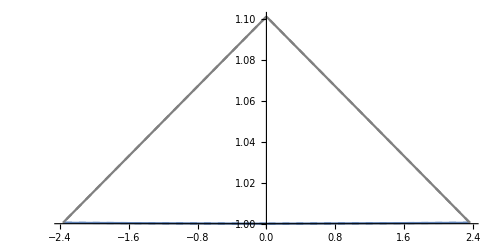

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

InterpolatingFunction::dmval: Input value {1.52883} lies outside the range of data in the interpolating function. Extrapolation will be used.

posición b2, b3{{ϕ→1.52832}}{ϕ→1.61327}0.4

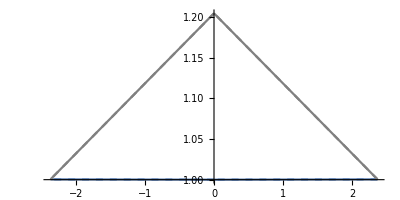

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

InterpolatingFunction::dmval: Input value {1.56712} lies outside the range of data in the interpolating function. Extrapolation will be used.

posición b2, b3{{ϕ→1.48479}}{ϕ→1.6568}0.4

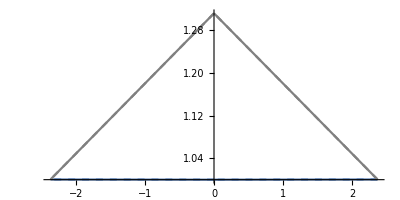

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve::ifun will be suppressed during this calculation.

$Aborted

```mathematica
DatAngN={};
DatAngSe={};
DataTriang={};
DataTriangFond={};
DatAngb2Pos={};
Do[
a=aVal[[i]];
(*C1*)
b0 =Rsun;(*m*)
Rsval1=RSch/b0;(*Rs=rs/b*)
Rsval1F=RSchF/b0;(*Rs=rs/b*)
Lval1=Λf*b0^2; (*Λ̄ = Λ b^2 -> *)
ϕMin1=0.4;
ϕMax1=π-ϕMin1;
δval=0;

(*Geodesic C1*)(*Print["c1"];*)

(*Metrica*)
sol1=NDSolve[{Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1[[1]];
sol12=NDSolve[{Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]; (*[π/2, ϕMax]*)

(*Fondo*)
sol1F=NDSolve[({Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1F[[1]];
sol12F=NDSolve[({Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Geodesic C2*)(*Print["c2"];*)
b1 =a*b0;(*m*)
Rsval2=RSch/b1;(*Rs=rs/b*)
Rsval2F=RSchF/b1;
Lval2=Λf*b1^2; (*Λ̄ = Λ b^2 -> *)
ϕMin2=ϕMin1;
ϕMax2=π/2;

(*Metrica*)
temp=(u[ϕMin2]*b1/b0)/.sol1[[1]];
sol2=NDSolve[{Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2},{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)

(*Fondo*)
temp=(u[ϕMin2]*b1/b0)/.sol1F[[1]];
sol2F=NDSolve[({Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2F}),{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];

(*Geodesic C2*)(*Print["c3"];*)
b2 =a*b0;(*m*)
Rsval3=RSch/b2;(*Rs=rs/b*)
Rsval3F=RSchF/b2;
Lval3=Λf*b2^2; (*Λ̄ = Λ b^2 -> *)
ϕMin3=ϕMax2;
ϕMax3=ϕMax1;

(*Metrica*)
temp=(u[ϕMax3]*b2/b0)/.sol12[[1]];
sol3=NDSolve[{Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3},{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Fondo*)
temp=(u[ϕMax3]*b2/b0)/.sol12F[[1]];
sol3F=NDSolve[({Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3F}),{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Construyendo tríangulos*)
DatTr={};
DatTrF={{},{},{}};
C1ϕvalor=Subdivide[ϕMin1,ϕMax1, 1000];
C2ϕvalor=Subdivide[ϕMin2,ϕMax2, 1000];
C3ϕvalor=Subdivide[ϕMin3,ϕMax3, 1000];
Do[
AppendTo[DatTr,{C1ϕvalor[[i]],
			    If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1[[1]],xf[C1ϕvalor[[i]]]/.sol12[[1]]], 
			    If[C1ϕvalor[[i]]<=π/2,yf[C1ϕvalor[[i]]]/.sol1[[1]],yf[C1ϕvalor[[i]]]/.sol12[[1]]],
			    C2ϕvalor[[i]],
			    b1/b0*xf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    b1/b0*yf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    C3ϕvalor[[i]],
			    b2/b0*xf[C3ϕvalor[[i]]]/.sol3[[1]],
			    b2/b0*yf[C3ϕvalor[[i]]]/.sol3[[1]]}];

(*Fondo*)
AppendTo[DatTrF,{C1ϕvalor[[i]],
			       If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1F[[1]],xf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      If[C1ϕvalor[[i]]<=π/2, yf[C1ϕvalor[[i]]]/.sol1F[[1]], yf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      C2ϕvalor[[i]],
			      b1/b0*xf[C2ϕvalor[[i]]]/.sol2F[[1]],
			      b1/b0*yf[C2ϕvalor[[i]]]/.sol2F[[1]],C3ϕvalor[[i]],
			      b2/b0*xf[C3ϕvalor[[i]]]/.sol3F[[1]], 
			      b2/b0*yf[C3ϕvalor[[i]]]/.sol3F[[1]]}];
,{i,1,Length[C1ϕvalor]}];

(*Graficandolos*)

Pc1=ParametricPlot[{xf[ϕ]/.sol1[[1]],yf[ϕ]/.sol1[[1]]},{ϕ,ϕMin1,π/2}, PlotRange->All,AspectRatio->0.5];
Pc12=ParametricPlot[{xf[ϕ]/.sol12[[1]],yf[ϕ]/.sol12[[1]]},{ϕ,π/2,ϕMax1}, PlotRange->All,AspectRatio->0.5];
Pc2=ParametricPlot[{b1/b0*xf[ϕ]/.sol2[[1]],b1/b0*yf[ϕ]/.sol2[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->Gray,AspectRatio->1];
Pc3=ParametricPlot[{b2/b0*xf[ϕ]/.sol3[[1]],b2/b0*yf[ϕ]/.sol3[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->Gray,AspectRatio->1];

Pc1F=ParametricPlot[{xf[ϕ]/.sol1F[[1]],yf[ϕ]/.sol1F[[1]]},{ϕ,ϕMin1,π/2}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc12F=ParametricPlot[{xf[ϕ]/.sol12F[[1]],yf[ϕ]/.sol12F[[1]]},{ϕ,π/2,ϕMax1}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc2F=ParametricPlot[{b1/b0*xf[ϕ]/.sol2F[[1]],b1/b0*yf[ϕ]/.sol2F[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];
Pc3F=ParametricPlot[{b2/b0*xf[ϕ]/.sol3F[[1]],b2/b0*yf[ϕ]/.sol3F[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];

Print[Show[{Pc1,Pc12,Pc2, Pc3,Pc1F,Pc12F,Pc2F,Pc3F},PlotRange->All]];

(*Calculando angulos*)
ptos={ϕMax1,π/2,ϕMin1};
(*C1*)
angC1 = Last[{Ang[ptos[[1]],Rsval1,Lval1]/.sol12,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1];
angC1F = Last[{Ang[ptos[[1]],Rsval1F,Lval1]/.sol12F,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1F];
(*C2*)
angC2= Last[{Ang[ptos[[-1]],Rsval2,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2];
angC2F = Last[{Ang[ptos[[-1]],Rsval2F,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2F];
(*C3*)
angC3= Last[{Ang[ptos[[2]],Rsval3,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3];
angC3F = Last[{Ang[ptos[[2]],Rsval3F,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3F];
(*Betas*)
betas = {angC3[[2]]-angC1[[1]], angC1[[2]]-angC2[[1]],-angC3[[1]]+angC2[[2]]};
betasF = {angC3F[[2]]-angC1F[[1]], angC1F[[2]]-angC2F[[1]],-angC3F[[1]]+angC2F[[2]]};
(*Serie*)
delI=NSolve[(u'[ϕ]/.sol2[[1]])==0,ϕ];
delI2=FindRoot[(u'[ϕ]/.sol3[[1]])==0,{ϕ,ϕMax3}];
Print["posición b2, b3",delI,delI2, ϕMin1];
delt=π/2-ϕ/.delI;
ASer=Last@angu2[delt,ϕMin1,b0,b2, Λf,Gf,M,c];
(*Salvando*)
AppendTo[DataTriang,DatTr];
AppendTo[DataTriangFond,DatTrF];
AppendTo[DatAngN,{a,Abs[Last@Total[betas-betasF]]}];
AppendTo[DatAngSe,{a,Abs@ASer}];
AppendTo[DatAngb2Pos,{a,ϕ/.delI[[1]]}],
{i, 1,Length[aVal]}
]
```

```mathematica
{aVal[[1]],aVal[[5]],aVal[[10]],aVal[[15]],aVal[[22]]}
```

{1.1,1.5,2.1,2.51,2.562}

```mathematica
Export["dataTriang1b2.dat", DataTriang[[1]]]
Export["dataTriang2b2.dat", DataTriang[[5]]]
Export["dataTriang3b2.dat", DataTriang[[10]]]
Export["dataTriang4b2.dat", DataTriang[[15]]]
Export["dataTriang5b2.dat", DataTriang[[22]]]

Export["dataTriangFond1b2.dat", DataTriangFond[[1]]]
Export["dataTriangFond2b2.dat", DataTriangFond[[5]]]
Export["dataTriangFond3b2.dat", DataTriangFond[[10]]]
Export["dataTriangFond4b2.dat", DataTriangFond[[15]]]
Export["dataTriangFond5b2.dat", DataTriangFond[[22]]]

Export["datab2Posit.dat", DatAngb2Pos]

Export["dataAngMatheb2.dat", DatAngN]
Export["dataAngSerMatheb2.dat", DatAngSe]
```

dataTriang1b2.dat

dataTriang2b2.dat

dataTriang3b2.dat

dataTriang4b2.dat

dataTriang5b2.dat

dataTriangFond1b2.dat

dataTriangFond2b2.dat

dataTriangFond3b2.dat

dataTriangFond4b2.dat

dataTriangFond5b2.dat

datab2Posit.dat

dataAngMatheb2.dat

dataAngSerMatheb2.dat

```mathematica
(*Length[aVal]*)
```

```mathematica
Ang2[M_,G_,b_, c_]:=4G M/(c^2b);
```

```mathematica
Ang2[M,Gf,b0,c]
```

0.000848635

```mathematica
{DatAngN,DatAngSe}
```

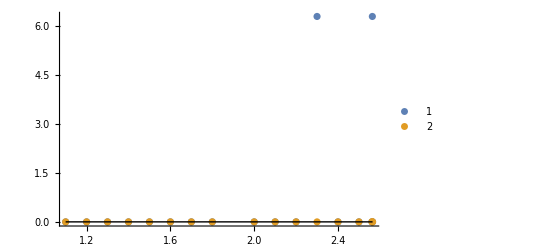

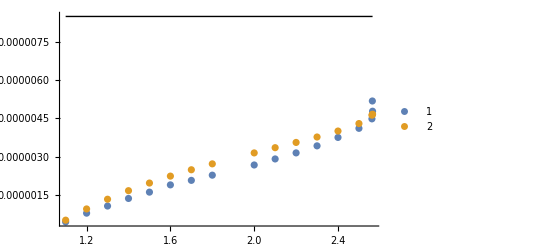

```mathematica
l1=Graphics[Line[{{aVal[[1]],Ang2[M,Gf,b0,c]},{aVal[[-1]],Ang2[M,Gf,b0,c]}}]];
l2=ListPlot[{DatAngN,DatAngSe},PlotLegends->Automatic,PlotRange->All,Joined->False];
Show[{l2,l1},PlotRange->All]
```

### Variando b2 caso 2, b0=2Radio del Sol

```mathematica
(*Caso 2*)
```

```mathematica
(*Variando b2*)
```

```mathematica
Quit[]
```

```mathematica
(* Ecuaciones Utilez *)
angu2[δ_,ϕ2_,b1_,b3_, Λ_,G_,M_,c_]:=((4 G M)/c^2  (-Cos[ϕ2]/b1+(Cos[δ+ϕ2]+Sin[δ])/b3)+1/6 (G M)/c^2  Λ ((2 b1)/(-1+Cos[ϕ2])-4 (b1-b3 Cos[δ]) Cos[ϕ2]-(2 b3)/(1+Cos[δ+ϕ2])+b3 Csc[(δ+ϕ2)/2]^2+b1 Sec[ϕ2/2]^2+4 b3 (Sin[δ]-Sin[δ] Sin[ϕ2]+Sec[δ] Tan[δ]))+1/36 (G M)/c^2  Λ^2 (b1^3 (-7+Cos[2 ϕ2]) Cot[ϕ2]^3 Csc[ϕ2]+b3^3 (-((-7+Cos[2 (δ+ϕ2)]) Cot[δ+ϕ2]^3 Csc[δ+ϕ2])+(7+Cos[2 δ]) Sec[δ] Tan[δ]^3)))+(-1/(4 b1^2 b3^2)(G^2 M^2)/c^4 (-15 b1^2 π+15 b3^2 π+30 b1^2 ϕ2-30 b3^2 ϕ2+b1^2 Sin[2 δ]-b3^2 Sin[2 ϕ2]+b1^2 Sin[2 (δ+ϕ2)])+1/384 (G^2 M^2)/c^4 Λ^2 (2 b1^2 (-30 π+60 ϕ2+97 Cot[ϕ2]) Csc[ϕ2]^4+62 b1^2 Cos[3 ϕ2] Csc[ϕ2]^5+b3^2 (12 (5 (π-2 (δ+ϕ2))-11 Cot[δ+ϕ2]) Csc[δ+ϕ2]^4+2 Sec[δ]^5 (60 δ Cos[δ]-97 Sin[δ]+31 Sin[3 δ])-31 Csc[δ+ϕ2]^6 Sin[4 (δ+ϕ2)]))+1/24 (G^2 M^2)/c^4 Λ (-15 π Csc[ϕ2]^2+30 ϕ2 Csc[ϕ2]^2+Cot[ϕ2] (-30+32 Csc[ϕ2]^2)+15 π Csc[δ+ϕ2]^2-30 δ Csc[δ+ϕ2]^2-30 ϕ2 Csc[δ+ϕ2]^2+Cot[δ+ϕ2] (30-32 Csc[δ+ϕ2]^2)+30 δ Sec[δ]^2-2 Sin[2 δ]+2 Sin[2 ϕ2]-2 Sin[2 (δ+ϕ2)]+30 Tan[δ]-32 Sec[δ]^2 Tan[δ])); (*Solución serie*)

Eq=-1-(Λ̄)/3+u[ϕ]^2-Rs u[ϕ]^3+u'[ϕ]^2==0;(*Ecuación de la geodésica*)

Ang[ϕ_,Rs_,Lb_]:=ArcTan[-(u[ϕ] √(1-Lb/(3 u[ϕ]^2)-Rs u[ϕ]))/u'[ϕ]]; 
(*conversión coordenadas*)
xf[ϕ_]:=Cos[ϕ]/u[ϕ];
yf[ϕ_]:=Sin[ϕ]/u[ϕ];
```

```mathematica
(*Cantidades Físicas, Tomando una Masa solar*)
Λf =1.1056 10^-52;(*m^-2*)
Msun=1.9885*10^30;(*kg*)
Rsun=6.96*10^8;(*m*)
Gf=6.674*10^-11;(*m^3 kg^-1 s^-2*)
c=299792458;(*m/s*)
M=Msun;
M2=0;
RSch=2Gf M/c^2 ;(*Sch radio -> m*)
RSchF=2Gf M2/c^2;
```

```mathematica
aVal={1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,2,2.1,2.2, 2.3,2.4,2.5,2.51,2.52, 2.53,2.54,2.55,2.56,2.562, 2.563,2.5635, 2.564};(*1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,2,2.1,2.2, 2.3,2.4,2.5,2.56, 2.565*)
```

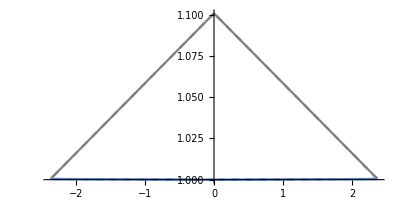

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

InterpolatingFunction::dmval: Input value {1.52883} lies outside the range of data in the interpolating function. Extrapolation will be used.

posición b2, b3{{ϕ→1.52832}}{ϕ→1.61327}0.4

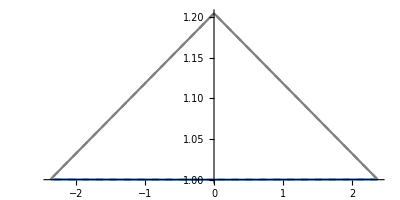

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

InterpolatingFunction::dmval: Input value {1.56712} lies outside the range of data in the interpolating function. Extrapolation will be used.

posición b2, b3{{ϕ→1.48479}}{ϕ→1.6568}0.4

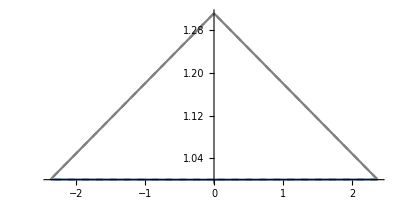

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve::ifun will be suppressed during this calculation.

posición b2, b3{{ϕ→1.44023}}{ϕ→1.70136}0.4

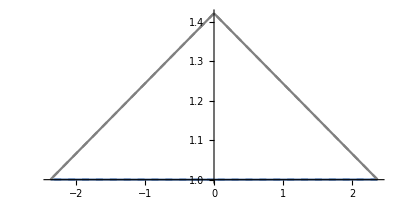

posición b2, b3{{ϕ→1.39446}}{ϕ→1.74713}0.4

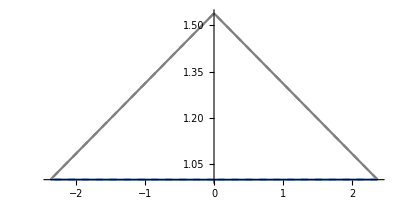

posición b2, b3{{ϕ→1.34729}}{ϕ→1.7943}0.4

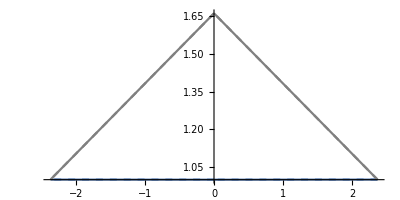

posición b2, b3{{ϕ→1.29852}}{ϕ→1.84307}0.4

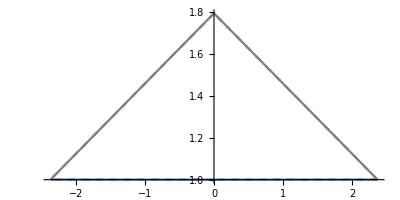

posición b2, b3{{ϕ→1.24769}}{ϕ→1.89391}0.4

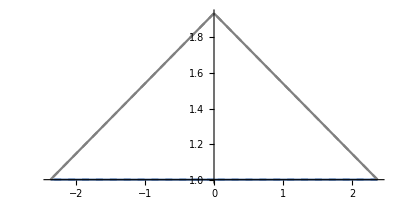

posición b2, b3{{ϕ→1.19447}}{ϕ→1.94712}0.4

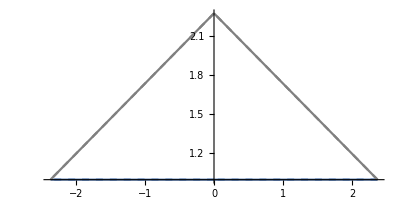

posición b2, b3{{ϕ→1.07851}}{ϕ→2.06308}0.4

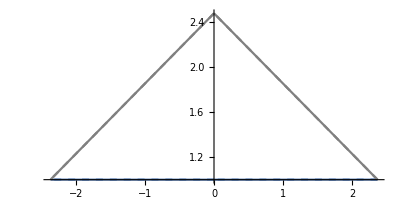

posición b2, b3{{ϕ→1.01386}}{ϕ→2.12774}0.4

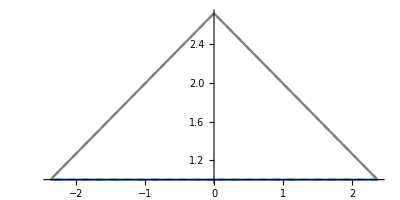

posición b2, b3{{ϕ→0.942618}}{ϕ→2.19897}0.4

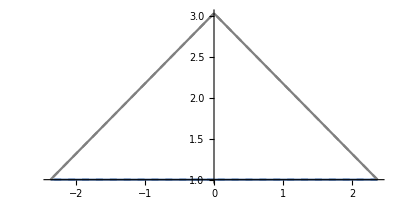

posición b2, b3{{ϕ→0.861728}}{ϕ→2.27986}0.4

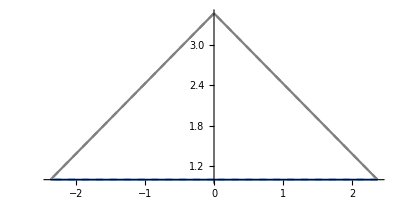

posición b2, b3{{ϕ→0.764759}}{ϕ→2.37683}0.4

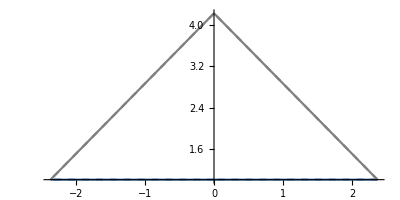

posición b2, b3{{ϕ→0.632319}}{ϕ→2.50927}0.4

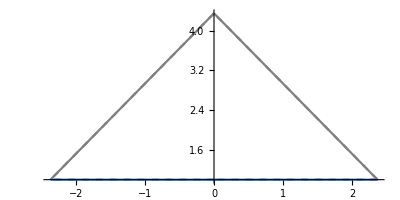

posición b2, b3{{ϕ→0.614764}}{ϕ→2.52683}0.4

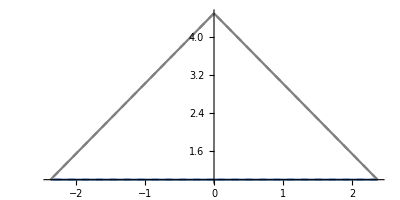

posición b2, b3{{ϕ→0.595656}}{ϕ→2.54594}0.4

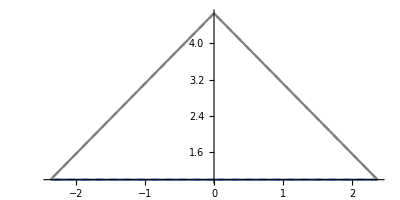

posición b2, b3{{ϕ→0.574505}}{ϕ→2.56709}0.4

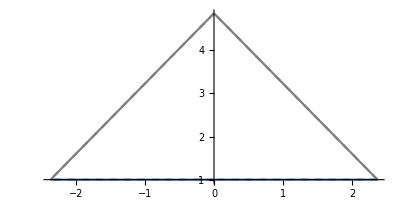

posición b2, b3{{ϕ→0.55044}}{ϕ→2.59115}0.4

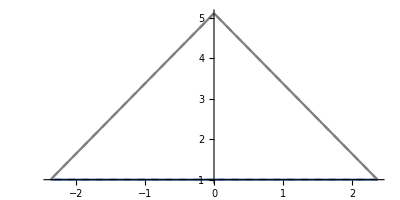

posición b2, b3{{ϕ→0.521749}}{ϕ→2.61984}0.4

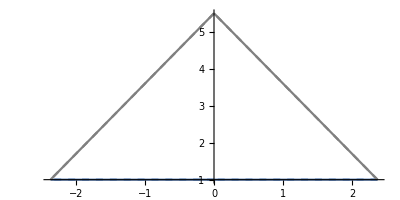

posición b2, b3{{ϕ→0.483813}}{ϕ→2.65778}0.4

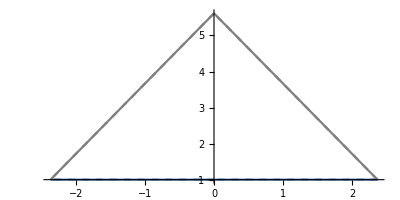

posición b2, b3{{ϕ→0.473919}}{ϕ→2.66767}0.4

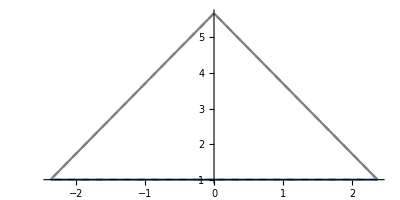

posición b2, b3{{ϕ→0.468447}}{ϕ→2.67315}0.4

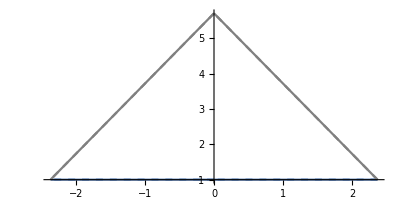

posición b2, b3{{ϕ→0.46554}}{ϕ→2.67605}0.4

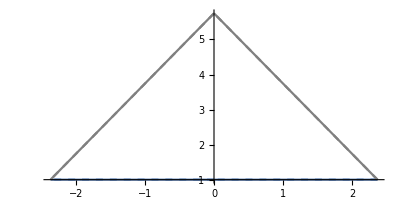

posición b2, b3{{ϕ→0.462499}}{ϕ→2.67909}0.4

```mathematica
DatAngN={};
DatAngSe={};
DataTriang={};
DataTriangFond={};
DatAngb2Pos={};
Do[
a=aVal[[i]];
(*C1*)
b0 =2*Rsun;(*m*)
Rsval1=RSch/b0;(*Rs=rs/b*)
Rsval1F=RSchF/b0;(*Rs=rs/b*)
Lval1=Λf*b0^2; (*Λ̄ = Λ b^2 -> *)
ϕMin1=0.4;
ϕMax1=π-ϕMin1;
δval=0;

(*Geodesic C1*)(*Print["c1"];*)

(*Metrica*)
sol1=NDSolve[{Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1[[1]];
sol12=NDSolve[{Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]; (*[π/2, ϕMax]*)

(*Fondo*)
sol1F=NDSolve[({Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1F[[1]];
sol12F=NDSolve[({Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Geodesic C2*)(*Print["c2"];*)
b1 =a*b0;(*m*)
Rsval2=RSch/b1;(*Rs=rs/b*)
Rsval2F=RSchF/b1;
Lval2=Λf*b1^2; (*Λ̄ = Λ b^2 -> *)
ϕMin2=ϕMin1;
ϕMax2=π/2;

(*Metrica*)
temp=(u[ϕMin2]*b1/b0)/.sol1[[1]];
sol2=NDSolve[{Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2},{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)

(*Fondo*)
temp=(u[ϕMin2]*b1/b0)/.sol1F[[1]];
sol2F=NDSolve[({Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2F}),{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];

(*Geodesic C2*)(*Print["c3"];*)
b2 =a*b0;(*m*)
Rsval3=RSch/b2;(*Rs=rs/b*)
Rsval3F=RSchF/b2;
Lval3=Λf*b2^2; (*Λ̄ = Λ b^2 -> *)
ϕMin3=ϕMax2;
ϕMax3=ϕMax1;

(*Metrica*)
temp=(u[ϕMax3]*b2/b0)/.sol12[[1]];
sol3=NDSolve[{Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3},{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Fondo*)
temp=(u[ϕMax3]*b2/b0)/.sol12F[[1]];
sol3F=NDSolve[({Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3F}),{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Construyendo tríangulos*)
DatTr={};
DatTrF={{},{},{}};
C1ϕvalor=Subdivide[ϕMin1,ϕMax1, 1000];
C2ϕvalor=Subdivide[ϕMin2,ϕMax2, 1000];
C3ϕvalor=Subdivide[ϕMin3,ϕMax3, 1000];
Do[
AppendTo[DatTr,{C1ϕvalor[[i]],
			    If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1[[1]],xf[C1ϕvalor[[i]]]/.sol12[[1]]], 
			    If[C1ϕvalor[[i]]<=π/2,yf[C1ϕvalor[[i]]]/.sol1[[1]],yf[C1ϕvalor[[i]]]/.sol12[[1]]],
			    C2ϕvalor[[i]],
			    b1/b0*xf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    b1/b0*yf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    C3ϕvalor[[i]],
			    b2/b0*xf[C3ϕvalor[[i]]]/.sol3[[1]],
			    b2/b0*yf[C3ϕvalor[[i]]]/.sol3[[1]]}];

(*Fondo*)
AppendTo[DatTrF,{C1ϕvalor[[i]],
			       If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1F[[1]],xf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      If[C1ϕvalor[[i]]<=π/2, yf[C1ϕvalor[[i]]]/.sol1F[[1]], yf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      C2ϕvalor[[i]],
			      b1/b0*xf[C2ϕvalor[[i]]]/.sol2F[[1]],
			      b1/b0*yf[C2ϕvalor[[i]]]/.sol2F[[1]],C3ϕvalor[[i]],
			      b2/b0*xf[C3ϕvalor[[i]]]/.sol3F[[1]], 
			      b2/b0*yf[C3ϕvalor[[i]]]/.sol3F[[1]]}];
,{i,1,Length[C1ϕvalor]}];

(*Graficandolos*)

Pc1=ParametricPlot[{xf[ϕ]/.sol1[[1]],yf[ϕ]/.sol1[[1]]},{ϕ,ϕMin1,π/2}, PlotRange->All,AspectRatio->0.5];
Pc12=ParametricPlot[{xf[ϕ]/.sol12[[1]],yf[ϕ]/.sol12[[1]]},{ϕ,π/2,ϕMax1}, PlotRange->All,AspectRatio->0.5];
Pc2=ParametricPlot[{b1/b0*xf[ϕ]/.sol2[[1]],b1/b0*yf[ϕ]/.sol2[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->Gray,AspectRatio->1];
Pc3=ParametricPlot[{b2/b0*xf[ϕ]/.sol3[[1]],b2/b0*yf[ϕ]/.sol3[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->Gray,AspectRatio->1];

Pc1F=ParametricPlot[{xf[ϕ]/.sol1F[[1]],yf[ϕ]/.sol1F[[1]]},{ϕ,ϕMin1,π/2}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc12F=ParametricPlot[{xf[ϕ]/.sol12F[[1]],yf[ϕ]/.sol12F[[1]]},{ϕ,π/2,ϕMax1}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc2F=ParametricPlot[{b1/b0*xf[ϕ]/.sol2F[[1]],b1/b0*yf[ϕ]/.sol2F[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];
Pc3F=ParametricPlot[{b2/b0*xf[ϕ]/.sol3F[[1]],b2/b0*yf[ϕ]/.sol3F[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];

Print[Show[{Pc1,Pc12,Pc2, Pc3,Pc1F,Pc12F,Pc2F,Pc3F},PlotRange->All]];

(*Calculando angulos*)
ptos={ϕMax1,π/2,ϕMin1};
(*C1*)
angC1 = Last[{Ang[ptos[[1]],Rsval1,Lval1]/.sol12,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1];
angC1F = Last[{Ang[ptos[[1]],Rsval1F,Lval1]/.sol12F,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1F];
(*C2*)
angC2= Last[{Ang[ptos[[-1]],Rsval2,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2];
angC2F = Last[{Ang[ptos[[-1]],Rsval2F,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2F];
(*C3*)
angC3= Last[{Ang[ptos[[2]],Rsval3,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3];
angC3F = Last[{Ang[ptos[[2]],Rsval3F,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3F];
(*Betas*)
betas = {angC3[[2]]-angC1[[1]], angC1[[2]]-angC2[[1]],-angC3[[1]]+angC2[[2]]};
betasF = {angC3F[[2]]-angC1F[[1]], angC1F[[2]]-angC2F[[1]],-angC3F[[1]]+angC2F[[2]]};
(*Serie*)
delI=NSolve[(u'[ϕ]/.sol2[[1]])==0,ϕ];
delI2=FindRoot[(u'[ϕ]/.sol3[[1]])==0,{ϕ,ϕMax3}];
Print["posición b2, b3",delI,delI2, ϕMin1];
delt=π/2-ϕ/.delI;
ASer=Last@angu2[delt,ϕMin1,b0,b2, Λf,Gf,M,c];
(*Salvando*)
AppendTo[DataTriang,DatTr];
AppendTo[DataTriangFond,DatTrF];
AppendTo[DatAngN,{a,Abs[Last@Total[betas-betasF]]}];
AppendTo[DatAngSe,{a,Abs@ASer}];
AppendTo[DatAngb2Pos,{a,ϕ/.delI[[1]]}],
{i, 1,Length[aVal]}
]
```

```mathematica
{aVal[[1]],aVal[[5]],aVal[[10]],aVal[[15]],aVal[[22]]}
```

{1.1,1.5,2.1,2.51,2.563}

```mathematica
Export["dataTriang1b2c2.dat", DataTriang[[1]]]
Export["dataTriang2b2c2.dat", DataTriang[[5]]]
Export["dataTriang3b2c2.dat", DataTriang[[10]]]
Export["dataTriang4b2c2.dat", DataTriang[[15]]]
Export["dataTriang5b2c2.dat", DataTriang[[22]]]

Export["dataTriangFond1b2c2.dat", DataTriangFond[[1]]]
Export["dataTriangFond2b2c2.dat", DataTriangFond[[5]]]
Export["dataTriangFond3b2c2.dat", DataTriangFond[[10]]]
Export["dataTriangFond4b2c2.dat", DataTriangFond[[15]]]
Export["dataTriangFond5b2c2.dat", DataTriangFond[[22]]]

Export["datab2Positc2.dat", DatAngb2Pos]

Export["dataAngMatheb2c2.dat", DatAngN]
Export["dataAngSerMatheb2c2.dat", DatAngSe]
```

dataTriang1b2c2.dat

dataTriang2b2c2.dat

dataTriang3b2c2.dat

dataTriang4b2c2.dat

dataTriang5b2c2.dat

dataTriangFond1b2c2.dat

dataTriangFond2b2c2.dat

dataTriangFond3b2c2.dat

dataTriangFond4b2c2.dat

dataTriangFond5b2c2.dat

datab2Positc2.dat

dataAngMatheb2c2.dat

dataAngSerMatheb2c2.dat

```mathematica
(*Length[aVal]*)
```

```mathematica
Ang2[M_,G_,b_, c_]:=4G M/(c^2b);
```

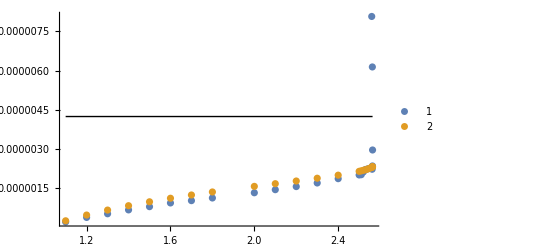

```mathematica
l1=Graphics[Line[{{aVal[[1]],Ang2[M,Gf,b0,c]},{aVal[[-1]],Ang2[M,Gf,b0,c]}}]];
l2=ListPlot[{DatAngN,DatAngSe},PlotLegends->Automatic,PlotRange->All,Joined->False];
Show[{l2,l1},PlotRange->All]
```

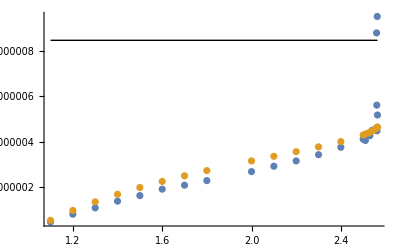

### Variando b2 caso 3, b0=0.5Radio del Sol

```mathematica
(*Caso 2*)
```

```mathematica
(*Variando b2*)
```

```mathematica
Quit[]
```

```mathematica
(* Ecuaciones Utilez *)
angu2[δ_,ϕ2_,b1_,b3_, Λ_,G_,M_,c_]:=((4 G M)/c^2  (-Cos[ϕ2]/b1+(Cos[δ+ϕ2]+Sin[δ])/b3)+1/6 (G M)/c^2  Λ ((2 b1)/(-1+Cos[ϕ2])-4 (b1-b3 Cos[δ]) Cos[ϕ2]-(2 b3)/(1+Cos[δ+ϕ2])+b3 Csc[(δ+ϕ2)/2]^2+b1 Sec[ϕ2/2]^2+4 b3 (Sin[δ]-Sin[δ] Sin[ϕ2]+Sec[δ] Tan[δ]))+1/36 (G M)/c^2  Λ^2 (b1^3 (-7+Cos[2 ϕ2]) Cot[ϕ2]^3 Csc[ϕ2]+b3^3 (-((-7+Cos[2 (δ+ϕ2)]) Cot[δ+ϕ2]^3 Csc[δ+ϕ2])+(7+Cos[2 δ]) Sec[δ] Tan[δ]^3)))+(-1/(4 b1^2 b3^2)(G^2 M^2)/c^4 (-15 b1^2 π+15 b3^2 π+30 b1^2 ϕ2-30 b3^2 ϕ2+b1^2 Sin[2 δ]-b3^2 Sin[2 ϕ2]+b1^2 Sin[2 (δ+ϕ2)])+1/384 (G^2 M^2)/c^4 Λ^2 (2 b1^2 (-30 π+60 ϕ2+97 Cot[ϕ2]) Csc[ϕ2]^4+62 b1^2 Cos[3 ϕ2] Csc[ϕ2]^5+b3^2 (12 (5 (π-2 (δ+ϕ2))-11 Cot[δ+ϕ2]) Csc[δ+ϕ2]^4+2 Sec[δ]^5 (60 δ Cos[δ]-97 Sin[δ]+31 Sin[3 δ])-31 Csc[δ+ϕ2]^6 Sin[4 (δ+ϕ2)]))+1/24 (G^2 M^2)/c^4 Λ (-15 π Csc[ϕ2]^2+30 ϕ2 Csc[ϕ2]^2+Cot[ϕ2] (-30+32 Csc[ϕ2]^2)+15 π Csc[δ+ϕ2]^2-30 δ Csc[δ+ϕ2]^2-30 ϕ2 Csc[δ+ϕ2]^2+Cot[δ+ϕ2] (30-32 Csc[δ+ϕ2]^2)+30 δ Sec[δ]^2-2 Sin[2 δ]+2 Sin[2 ϕ2]-2 Sin[2 (δ+ϕ2)]+30 Tan[δ]-32 Sec[δ]^2 Tan[δ])); (*Solución serie*)

Eq=-1-(Λ̄)/3+u[ϕ]^2-Rs u[ϕ]^3+u'[ϕ]^2==0;(*Ecuación de la geodésica*)

Ang[ϕ_,Rs_,Lb_]:=ArcTan[-(u[ϕ] √(1-Lb/(3 u[ϕ]^2)-Rs u[ϕ]))/u'[ϕ]]; 
(*conversión coordenadas*)
xf[ϕ_]:=Cos[ϕ]/u[ϕ];
yf[ϕ_]:=Sin[ϕ]/u[ϕ];
```

```mathematica
(*Cantidades Físicas, Tomando una Masa solar*)
Λf =1.1056 10^-52;(*m^-2*)
Msun=1.9885*10^30;(*kg*)
Rsun=6.96*10^8;(*m*)
Gf=6.674*10^-11;(*m^3 kg^-1 s^-2*)
c=299792458;(*m/s*)
M=Msun;
M2=0;
RSch=2Gf M/c^2 ;(*Sch radio -> m*)
RSchF=2Gf M2/c^2;
```

```mathematica
aVal={1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,2,2.1,2.2, 2.3,2.4,2.5,2.51,2.52, 2.53,2.54,2.55,2.56,2.562, 2.563,2.5635, 2.564};(*1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,2,2.1,2.2, 2.3,2.4,2.5,2.56, 2.565*)
```

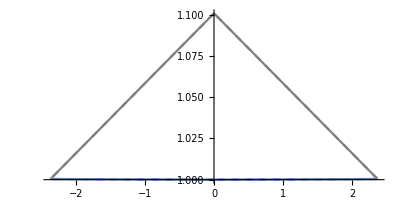

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

InterpolatingFunction::dmval: Input value {1.52883} lies outside the range of data in the interpolating function. Extrapolation will be used.

posición b2, b3{{ϕ→1.52832}}{ϕ→1.61328}0.4

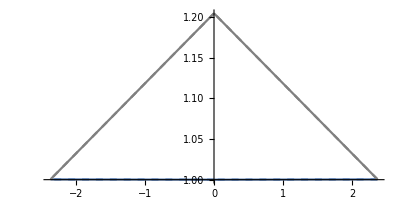

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

InterpolatingFunction::dmval: Input value {1.56712} lies outside the range of data in the interpolating function. Extrapolation will be used.

posición b2, b3{{ϕ→1.48479}}{ϕ→1.65681}0.4

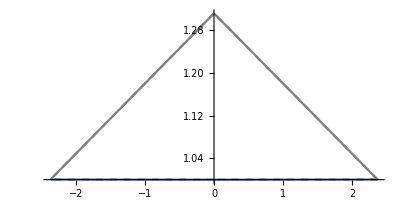

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve::ifun will be suppressed during this calculation.

posición b2, b3{{ϕ→1.44023}}{ϕ→1.70136}0.4

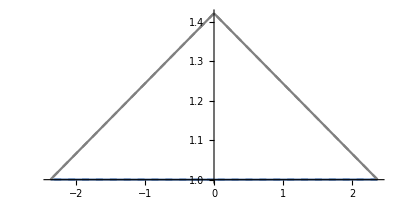

posición b2, b3{{ϕ→1.39445}}{ϕ→1.74714}0.4

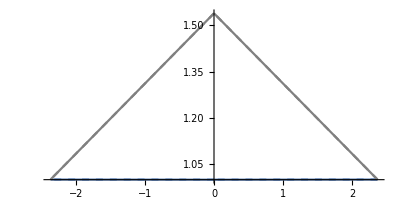

posición b2, b3{{ϕ→1.34729}}{ϕ→1.79431}0.4

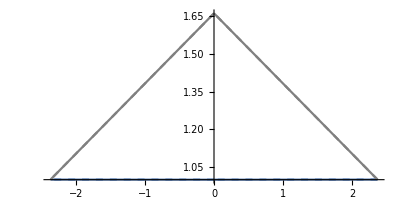

posición b2, b3{{ϕ→1.29851}}{ϕ→1.84308}0.4

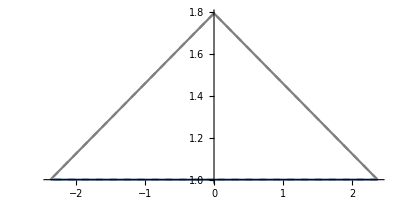

posición b2, b3{{ϕ→1.24768}}{ϕ→1.89391}0.4

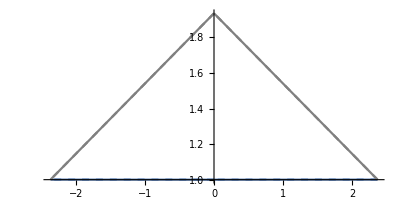

posición b2, b3{{ϕ→1.19446}}{ϕ→1.94713}0.4

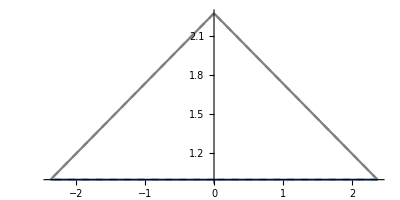

posición b2, b3{{ϕ→1.07849}}{ϕ→2.0631}0.4

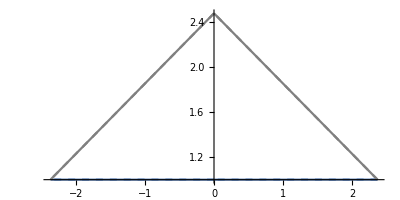

posición b2, b3{{ϕ→1.01384}}{ϕ→2.12775}0.4

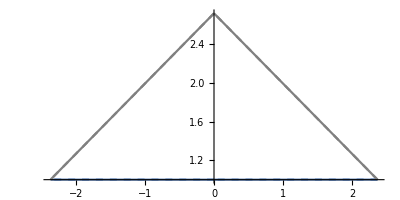

posición b2, b3{{ϕ→0.942596}}{ϕ→2.199}0.4

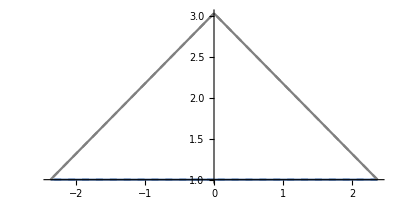

posición b2, b3{{ϕ→0.861701}}{ϕ→2.27989}0.4

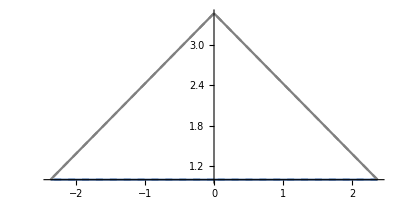

posición b2, b3{{ϕ→0.764723}}{ϕ→2.37687}0.4

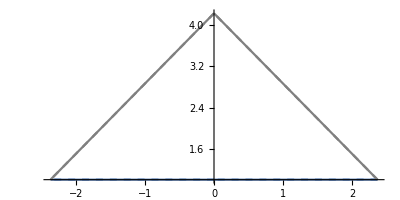

posición b2, b3{{ϕ→0.63226}}{ϕ→2.50933}0.4

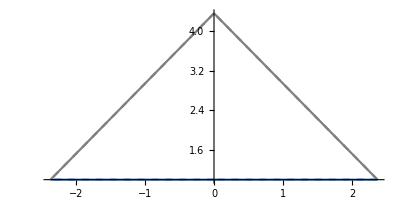

posición b2, b3{{ϕ→0.6147}}{ϕ→2.52689}0.4

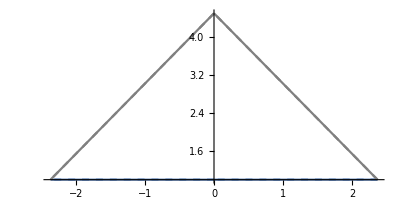

posición b2, b3{{ϕ→0.595586}}{ϕ→2.54601}0.4

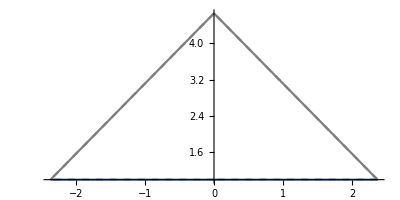

posición b2, b3{{ϕ→0.574426}}{ϕ→2.56717}0.4

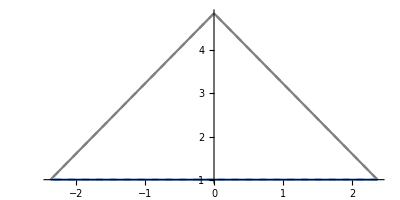

posición b2, b3{{ϕ→0.550348}}{ϕ→2.59124}0.4

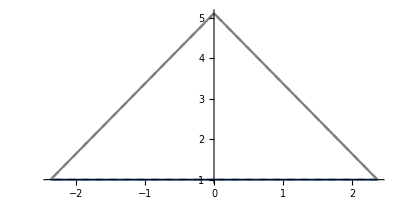

posición b2, b3{{ϕ→0.521634}}{ϕ→2.61996}0.4

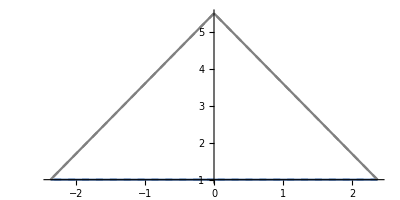

posición b2, b3{{ϕ→0.483646}}{ϕ→2.65795}0.4

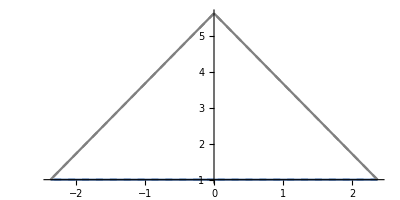

posición b2, b3{{ϕ→0.47373}}{ϕ→2.66786}0.4

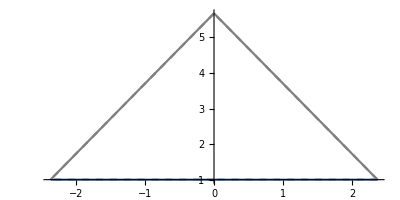

posición b2, b3{{ϕ→0.468243}}{ϕ→2.67335}0.4

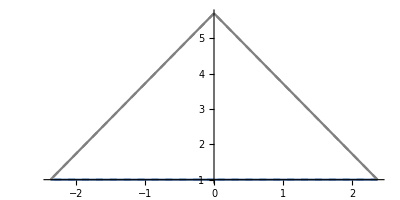

posición b2, b3{{ϕ→0.465327}}{ϕ→2.67627}0.4

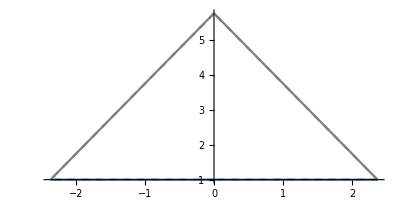

posición b2, b3{{ϕ→0.462274}}{ϕ→2.67932}0.4

```mathematica
DatAngN={};
DatAngSe={};
DataTriang={};
DataTriangFond={};
DatAngb2Pos={};
Do[
a=aVal[[i]];
(*C1*)
b0 =0.5*Rsun;(*m*)
Rsval1=RSch/b0;(*Rs=rs/b*)
Rsval1F=RSchF/b0;(*Rs=rs/b*)
Lval1=Λf*b0^2; (*Λ̄ = Λ b^2 -> *)
ϕMin1=0.4;
ϕMax1=π-ϕMin1;
δval=0;

(*Geodesic C1*)(*Print["c1"];*)

(*Metrica*)
sol1=NDSolve[{Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1[[1]];
sol12=NDSolve[{Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]; (*[π/2, ϕMax]*)

(*Fondo*)
sol1F=NDSolve[({Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1F[[1]];
sol12F=NDSolve[({Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Geodesic C2*)(*Print["c2"];*)
b1 =a*b0;(*m*)
Rsval2=RSch/b1;(*Rs=rs/b*)
Rsval2F=RSchF/b1;
Lval2=Λf*b1^2; (*Λ̄ = Λ b^2 -> *)
ϕMin2=ϕMin1;
ϕMax2=π/2;

(*Metrica*)
temp=(u[ϕMin2]*b1/b0)/.sol1[[1]];
sol2=NDSolve[{Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2},{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)

(*Fondo*)
temp=(u[ϕMin2]*b1/b0)/.sol1F[[1]];
sol2F=NDSolve[({Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2F}),{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];

(*Geodesic C2*)(*Print["c3"];*)
b2 =a*b0;(*m*)
Rsval3=RSch/b2;(*Rs=rs/b*)
Rsval3F=RSchF/b2;
Lval3=Λf*b2^2; (*Λ̄ = Λ b^2 -> *)
ϕMin3=ϕMax2;
ϕMax3=ϕMax1;

(*Metrica*)
temp=(u[ϕMax3]*b2/b0)/.sol12[[1]];
sol3=NDSolve[{Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3},{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Fondo*)
temp=(u[ϕMax3]*b2/b0)/.sol12F[[1]];
sol3F=NDSolve[({Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3F}),{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Construyendo tríangulos*)
DatTr={};
DatTrF={{},{},{}};
C1ϕvalor=Subdivide[ϕMin1,ϕMax1, 1000];
C2ϕvalor=Subdivide[ϕMin2,ϕMax2, 1000];
C3ϕvalor=Subdivide[ϕMin3,ϕMax3, 1000];
Do[
AppendTo[DatTr,{C1ϕvalor[[i]],
			    If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1[[1]],xf[C1ϕvalor[[i]]]/.sol12[[1]]], 
			    If[C1ϕvalor[[i]]<=π/2,yf[C1ϕvalor[[i]]]/.sol1[[1]],yf[C1ϕvalor[[i]]]/.sol12[[1]]],
			    C2ϕvalor[[i]],
			    b1/b0*xf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    b1/b0*yf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    C3ϕvalor[[i]],
			    b2/b0*xf[C3ϕvalor[[i]]]/.sol3[[1]],
			    b2/b0*yf[C3ϕvalor[[i]]]/.sol3[[1]]}];

(*Fondo*)
AppendTo[DatTrF,{C1ϕvalor[[i]],
			       If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1F[[1]],xf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      If[C1ϕvalor[[i]]<=π/2, yf[C1ϕvalor[[i]]]/.sol1F[[1]], yf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      C2ϕvalor[[i]],
			      b1/b0*xf[C2ϕvalor[[i]]]/.sol2F[[1]],
			      b1/b0*yf[C2ϕvalor[[i]]]/.sol2F[[1]],C3ϕvalor[[i]],
			      b2/b0*xf[C3ϕvalor[[i]]]/.sol3F[[1]], 
			      b2/b0*yf[C3ϕvalor[[i]]]/.sol3F[[1]]}];
,{i,1,Length[C1ϕvalor]}];

(*Graficandolos*)

Pc1=ParametricPlot[{xf[ϕ]/.sol1[[1]],yf[ϕ]/.sol1[[1]]},{ϕ,ϕMin1,π/2}, PlotRange->All,AspectRatio->0.5];
Pc12=ParametricPlot[{xf[ϕ]/.sol12[[1]],yf[ϕ]/.sol12[[1]]},{ϕ,π/2,ϕMax1}, PlotRange->All,AspectRatio->0.5];
Pc2=ParametricPlot[{b1/b0*xf[ϕ]/.sol2[[1]],b1/b0*yf[ϕ]/.sol2[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->Gray,AspectRatio->1];
Pc3=ParametricPlot[{b2/b0*xf[ϕ]/.sol3[[1]],b2/b0*yf[ϕ]/.sol3[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->Gray,AspectRatio->1];

Pc1F=ParametricPlot[{xf[ϕ]/.sol1F[[1]],yf[ϕ]/.sol1F[[1]]},{ϕ,ϕMin1,π/2}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc12F=ParametricPlot[{xf[ϕ]/.sol12F[[1]],yf[ϕ]/.sol12F[[1]]},{ϕ,π/2,ϕMax1}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc2F=ParametricPlot[{b1/b0*xf[ϕ]/.sol2F[[1]],b1/b0*yf[ϕ]/.sol2F[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];
Pc3F=ParametricPlot[{b2/b0*xf[ϕ]/.sol3F[[1]],b2/b0*yf[ϕ]/.sol3F[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];

Print[Show[{Pc1,Pc12,Pc2, Pc3,Pc1F,Pc12F,Pc2F,Pc3F},PlotRange->All]];

(*Calculando angulos*)
ptos={ϕMax1,π/2,ϕMin1};
(*C1*)
angC1 = Last[{Ang[ptos[[1]],Rsval1,Lval1]/.sol12,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1];
angC1F = Last[{Ang[ptos[[1]],Rsval1F,Lval1]/.sol12F,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1F];
(*C2*)
angC2= Last[{Ang[ptos[[-1]],Rsval2,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2];
angC2F = Last[{Ang[ptos[[-1]],Rsval2F,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2F];
(*C3*)
angC3= Last[{Ang[ptos[[2]],Rsval3,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3];
angC3F = Last[{Ang[ptos[[2]],Rsval3F,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3F];
(*Betas*)
betas = {angC3[[2]]-angC1[[1]], angC1[[2]]-angC2[[1]],-angC3[[1]]+angC2[[2]]};
betasF = {angC3F[[2]]-angC1F[[1]], angC1F[[2]]-angC2F[[1]],-angC3F[[1]]+angC2F[[2]]};
(*Serie*)
delI=NSolve[(u'[ϕ]/.sol2[[1]])==0,ϕ];
delI2=FindRoot[(u'[ϕ]/.sol3[[1]])==0,{ϕ,ϕMax3}];
Print["posición b2, b3",delI,delI2, ϕMin1];
delt=π/2-ϕ/.delI;
ASer=Last@angu2[delt,ϕMin1,b0,b2, Λf,Gf,M,c];
(*Salvando*)
AppendTo[DataTriang,DatTr];
AppendTo[DataTriangFond,DatTrF];
AppendTo[DatAngN,{a,Abs[Last@Total[betas-betasF]]}];
AppendTo[DatAngSe,{a,Abs@ASer}];
AppendTo[DatAngb2Pos,{a,ϕ/.delI[[1]]}],
{i, 1,Length[aVal]}
]
```

```mathematica
{aVal[[1]],aVal[[5]],aVal[[10]],aVal[[15]],aVal[[22]]}
```

{1.1,1.5,2.1,2.51,2.563}

```mathematica
Export["dataTriang1b2c3.dat", DataTriang[[1]]]
Export["dataTriang2b2c3.dat", DataTriang[[5]]]
Export["dataTriang3b2c3.dat", DataTriang[[10]]]
Export["dataTriang4b2c3.dat", DataTriang[[15]]]
Export["dataTriang5b2c3.dat", DataTriang[[22]]]

Export["dataTriangFond1b2c3.dat", DataTriangFond[[1]]]
Export["dataTriangFond2b2c3.dat", DataTriangFond[[5]]]
Export["dataTriangFond3b2c3.dat", DataTriangFond[[10]]]
Export["dataTriangFond4b2c3.dat", DataTriangFond[[15]]]
Export["dataTriangFond5b2c3.dat", DataTriangFond[[22]]]

Export["datab2Positc3.dat", DatAngb2Pos]

Export["dataAngMatheb2c3.dat", DatAngN]
Export["dataAngSerMatheb2c3.dat", DatAngSe]
```

dataTriang1b2c2.dat

dataTriang2b2c2.dat

dataTriang3b2c2.dat

dataTriang4b2c2.dat

dataTriang5b2c2.dat

dataTriangFond1b2c2.dat

dataTriangFond2b2c2.dat

dataTriangFond3b2c2.dat

dataTriangFond4b2c2.dat

dataTriangFond5b2c2.dat

datab2Positc2.dat

dataAngMatheb2c2.dat

dataAngSerMatheb2c2.dat

```mathematica
Export["dataAngMatheb2c3.dat", DatAngN]
Export["dataAngSerMatheb2c3.dat", DatAngSe]
```

dataAngMatheb2c3.dat

dataAngSerMatheb2c3.dat

```mathematica
(*Length[aVal]*)
```

```mathematica
Ang2[M_,G_,b_, c_]:=4G M/(c^2b);
```

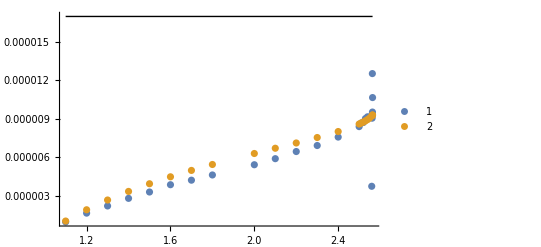

-Graphics-

```mathematica
l1=Graphics[Line[{{aVal[[1]],Ang2[M,Gf,b0,c]},{aVal[[-1]],Ang2[M,Gf,b0,c]}}]];
l2=ListPlot[{DatAngN,DatAngSe},PlotLegends->Automatic,PlotRange->All,Joined->False];
Show[{l2,l1},PlotRange->All]
```

### Variando b2 caso 1, b0=1Radio del Sol θMin=0.04

```mathematica
(*Variando b2*)
```

```mathematica
Quit[]
```

```mathematica
(* Ecuaciones Utilez *)
angu2[δ_,ϕ2_,b1_,b3_, Λ_,G_,M_,c_]:=((4 G M)/c^2  (-Cos[ϕ2]/b1+(Cos[δ+ϕ2]+Sin[δ])/b3)+1/6 (G M)/c^2  Λ ((2 b1)/(-1+Cos[ϕ2])-4 (b1-b3 Cos[δ]) Cos[ϕ2]-(2 b3)/(1+Cos[δ+ϕ2])+b3 Csc[(δ+ϕ2)/2]^2+b1 Sec[ϕ2/2]^2+4 b3 (Sin[δ]-Sin[δ] Sin[ϕ2]+Sec[δ] Tan[δ]))+1/36 (G M)/c^2  Λ^2 (b1^3 (-7+Cos[2 ϕ2]) Cot[ϕ2]^3 Csc[ϕ2]+b3^3 (-((-7+Cos[2 (δ+ϕ2)]) Cot[δ+ϕ2]^3 Csc[δ+ϕ2])+(7+Cos[2 δ]) Sec[δ] Tan[δ]^3)))+(-1/(4 b1^2 b3^2)(G^2 M^2)/c^4 (-15 b1^2 π+15 b3^2 π+30 b1^2 ϕ2-30 b3^2 ϕ2+b1^2 Sin[2 δ]-b3^2 Sin[2 ϕ2]+b1^2 Sin[2 (δ+ϕ2)])+1/384 (G^2 M^2)/c^4 Λ^2 (2 b1^2 (-30 π+60 ϕ2+97 Cot[ϕ2]) Csc[ϕ2]^4+62 b1^2 Cos[3 ϕ2] Csc[ϕ2]^5+b3^2 (12 (5 (π-2 (δ+ϕ2))-11 Cot[δ+ϕ2]) Csc[δ+ϕ2]^4+2 Sec[δ]^5 (60 δ Cos[δ]-97 Sin[δ]+31 Sin[3 δ])-31 Csc[δ+ϕ2]^6 Sin[4 (δ+ϕ2)]))+1/24 (G^2 M^2)/c^4 Λ (-15 π Csc[ϕ2]^2+30 ϕ2 Csc[ϕ2]^2+Cot[ϕ2] (-30+32 Csc[ϕ2]^2)+15 π Csc[δ+ϕ2]^2-30 δ Csc[δ+ϕ2]^2-30 ϕ2 Csc[δ+ϕ2]^2+Cot[δ+ϕ2] (30-32 Csc[δ+ϕ2]^2)+30 δ Sec[δ]^2-2 Sin[2 δ]+2 Sin[2 ϕ2]-2 Sin[2 (δ+ϕ2)]+30 Tan[δ]-32 Sec[δ]^2 Tan[δ])); (*Solución serie*)

Eq=-1-(Λ̄)/3+u[ϕ]^2-Rs u[ϕ]^3+u'[ϕ]^2==0;(*Ecuación de la geodésica*)

Ang[ϕ_,Rs_,Lb_]:=ArcTan[-(u[ϕ] √(1-Lb/(3 u[ϕ]^2)-Rs u[ϕ]))/u'[ϕ]]; 
(*conversión coordenadas*)
xf[ϕ_]:=Cos[ϕ]/u[ϕ];
yf[ϕ_]:=Sin[ϕ]/u[ϕ];
```

```mathematica
(*Cantidades Físicas, Tomando una Masa solar*)
Λf =1.1056 10^-52;(*m^-2*)
Msun=1.9885*10^30;(*kg*)
Rsun=6.96*10^8;(*m*)
Gf=6.674*10^-11;(*m^3 kg^-1 s^-2*)
c=299792458;(*m/s*)
M=1*Msun;
M2=0;
RSch=2Gf M/c^2 ;(*Sch radio -> m*)
RSchF=2Gf M2/c^2;
```

```mathematica
aVal={1.1,1.5,2,2.5,3.0,3.5,4.0,4.5,5.0,6,7,8,9,10, 11,12,13,13.8,14.8,15.85,16.7,18,19,20,21.8,22.75,23.7, 24.7,25.087}; (*{1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,2,2.1,2.2, 2.3,2.4,2.5, 2.51,2.52,2.53, 2.54,2.55,2.56, 2.561, 2.562,2.563,2.564}*)
```

1.1

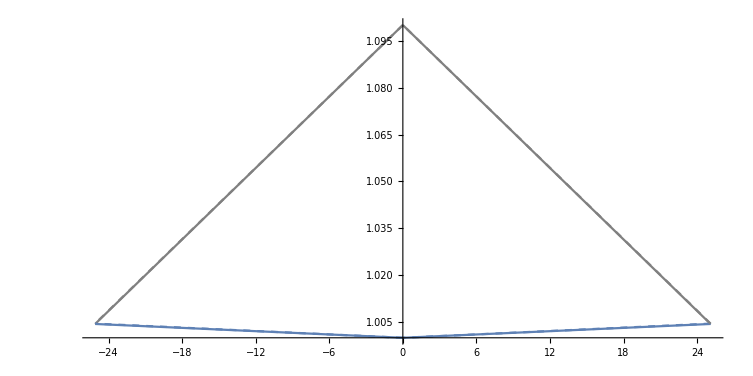

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

InterpolatingFunction::dmval: Input value {-2.59489} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.1116} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.55593} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

posición b2, b3{{ϕ→1.56699}}{ϕ→1.57461}0.04

1.5

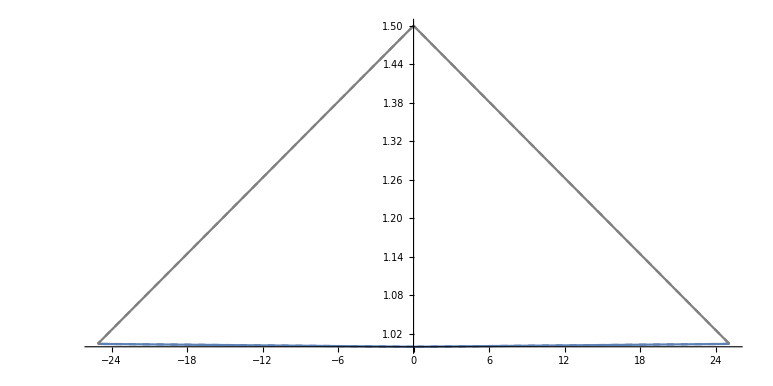

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

posición b2, b3{{ϕ→1.55104}}{ϕ→1.59055}0.04

2

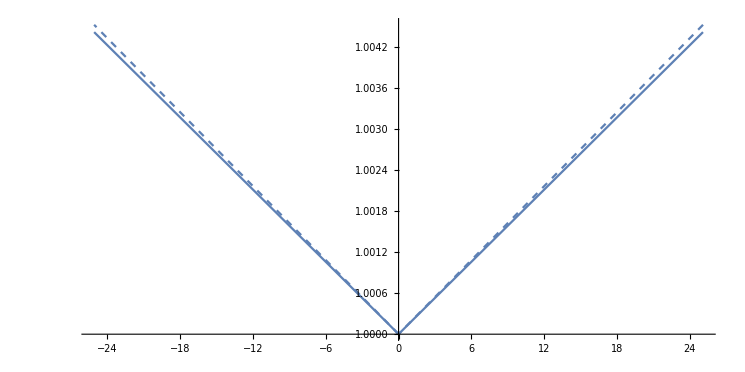

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve::ifun will be suppressed during this calculation.

posición b2, b3{{ϕ→1.53109}}{ϕ→1.61051}0.04

2.5

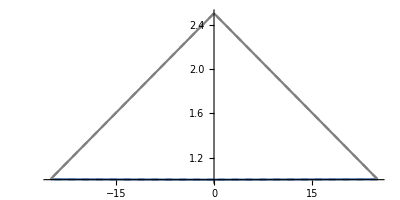

posición b2, b3{{ϕ→1.5111}}{ϕ→1.63049}0.04

3.

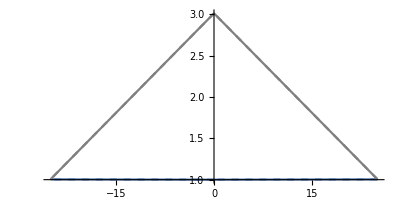

posición b2, b3{{ϕ→1.49108}}{ϕ→1.65052}0.04

3.5

NDSolve::ndcf: Repeated convergence test failure at ϕ == 1.5088; unable to continue.

NDSolve::ndcf: Repeated convergence test failure at ϕ == 1.63279; unable to continue.

General::stop: Further output of NDSolve::ndcf will be suppressed during this calculation.

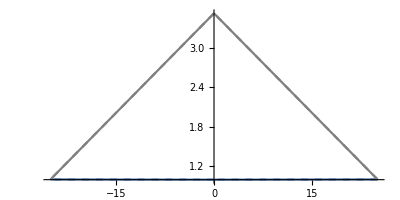

posición b2, b3{{ϕ→1.47099}}{ϕ→1.6706}0.04

4.

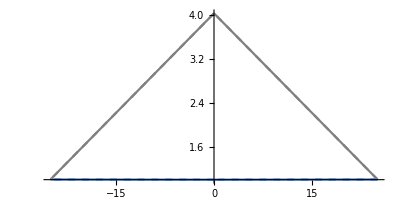

posición b2, b3{{ϕ→1.45087}}{ϕ→1.69073}0.04

4.5

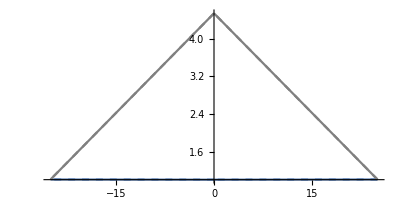

posición b2, b3{{ϕ→1.43066}}{ϕ→1.71093}0.04

5.

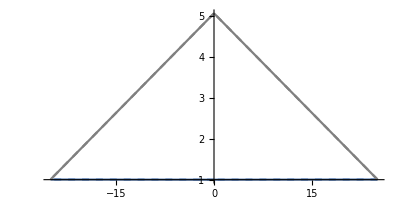

posición b2, b3{{ϕ→1.41039}}{ϕ→1.7312}0.04

6

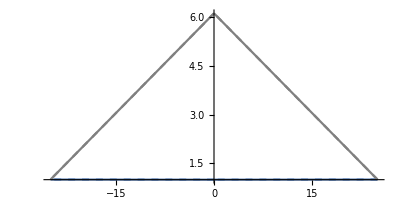

posición b2, b3{{ϕ→1.36958}}{ϕ→1.77201}0.04

7

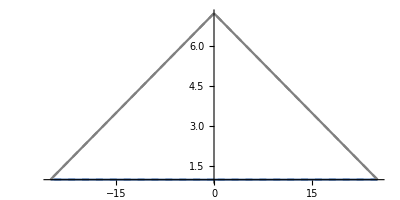

posición b2, b3{{ϕ→1.32837}}{ϕ→1.81322}0.04

8

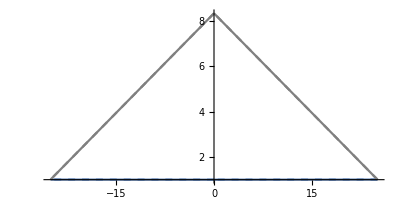

posición b2, b3{{ϕ→1.28664}}{ϕ→1.85495}0.04

9

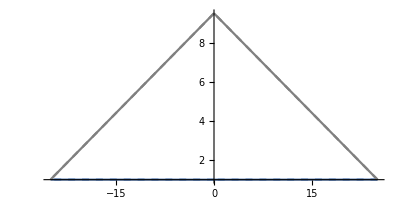

posición b2, b3{{ϕ→1.24433}}{ϕ→1.89726}0.04

10

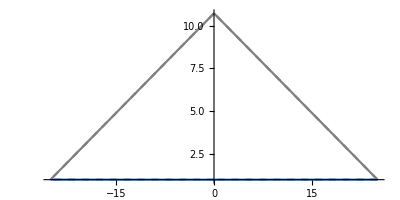

posición b2, b3{{ϕ→1.20131}}{ϕ→1.94028}0.04

11

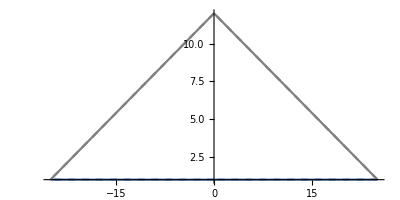

posición b2, b3{{ϕ→1.15749}}{ϕ→1.9841}0.04

12

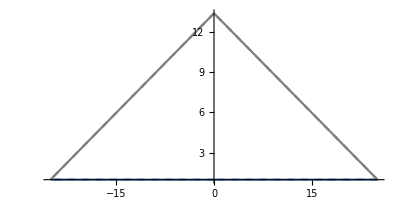

posición b2, b3{{ϕ→1.11269}}{ϕ→2.0289}0.04

13

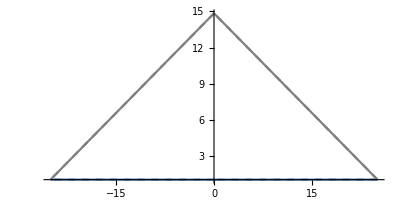

posición b2, b3{{ϕ→1.06677}}{ϕ→2.07482}0.04

13.8

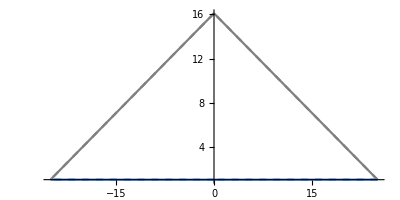

posición b2, b3{{ϕ→1.02912}}{ϕ→2.11247}0.04

14.8

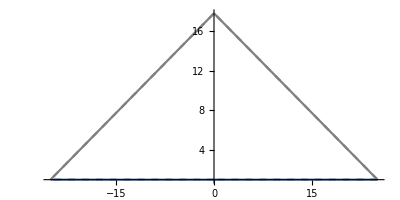

posición b2, b3{{ϕ→0.98068}}{ϕ→2.16091}0.04

15.85

-Graphics-

posición b2, b3{{ϕ→0.927897}}{ϕ→2.2137}0.04

16.7

-Graphics-

posición b2, b3{{ϕ→0.883472}}{ϕ→2.25812}0.04

18

-Graphics-

posición b2, b3{{ϕ→0.811822}}{ϕ→2.32977}0.04

19

-Graphics-

posición b2, b3{{ϕ→0.752922}}{ϕ→2.38867}0.04

20

-Graphics-

posición b2, b3{{ϕ→0.689702}}{ϕ→2.45189}0.04

21.8

-Graphics-

posición b2, b3{{ϕ→0.559773}}{ϕ→2.58182}0.04

22.75

-Graphics-

posición b2, b3{{ϕ→0.477639}}{ϕ→2.66395}0.04

23.7

-Graphics-

posición b2, b3{{ϕ→0.377522}}{ϕ→2.76407}0.04

24.7

-Graphics-

posición b2, b3{{ϕ→0.222509}}{ϕ→2.91908}0.04

25.087

-Graphics-

posición b2, b3{{ϕ→0.0890019}}{ϕ→3.05259}0.04

```mathematica
DatAngN={};
DatAngSe={};
DataTriang={};
DataTriangFond={};
DatAngb2Pos={};
Do[
a=aVal[[i]];
Print[a];
(*C1*)
b0 =Rsun;(*m*)
Rsval1=RSch/b0;(*Rs=rs/b*)
Rsval1F=RSchF/b0;(*Rs=rs/b*)
Lval1=Λf*b0^2; (*Λ̄ = Λ b^2 -> *)
ϕMin1=0.04;
ϕMax1=π-ϕMin1;
δval=0;

(*Geodesic C1*)(*Print["c1"];*)

(*Metrica*)
sol1=NDSolve[{Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1[[1]];
sol12=NDSolve[{Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]; (*[π/2, ϕMax]*)

(*Fondo*)
sol1F=NDSolve[({Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1F[[1]];
sol12F=NDSolve[({Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Geodesic C2*)(*Print["c2"];*)
b1 =a*b0;(*m*)
Rsval2=RSch/b1;(*Rs=rs/b*)
Rsval2F=RSchF/b1;
Lval2=Λf*b1^2; (*Λ̄ = Λ b^2 -> *)
ϕMin2=ϕMin1;
ϕMax2=π/2;

(*Metrica*)
temp=(u[ϕMin2]*b1/b0)/.sol1[[1]];
sol2=NDSolve[{Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2},{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)

(*Fondo*)
temp=(u[ϕMin2]*b1/b0)/.sol1F[[1]];
sol2F=NDSolve[({Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2F}),{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];

(*Geodesic C2*)(*Print["c3"];*)
b2 =a*b0;(*m*)
Rsval3=RSch/b2;(*Rs=rs/b*)
Rsval3F=RSchF/b2;
Lval3=Λf*b2^2; (*Λ̄ = Λ b^2 -> *)
ϕMin3=ϕMax2;
ϕMax3=ϕMax1;

(*Metrica*)
temp=(u[ϕMax3]*b2/b0)/.sol12[[1]];
sol3=NDSolve[{Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3},{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Fondo*)
temp=(u[ϕMax3]*b2/b0)/.sol12F[[1]];
sol3F=NDSolve[({Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3F}),{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Construyendo tríangulos*)
DatTr={};
DatTrF={{},{},{}};
C1ϕvalor=Subdivide[ϕMin1,ϕMax1, 1000];
C2ϕvalor=Subdivide[ϕMin2,ϕMax2, 1000];
C3ϕvalor=Subdivide[ϕMin3,ϕMax3, 1000];
Do[
AppendTo[DatTr,{C1ϕvalor[[i]],
			    If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1[[1]],xf[C1ϕvalor[[i]]]/.sol12[[1]]], 
			    If[C1ϕvalor[[i]]<=π/2,yf[C1ϕvalor[[i]]]/.sol1[[1]],yf[C1ϕvalor[[i]]]/.sol12[[1]]],
			    C2ϕvalor[[i]],
			    b1/b0*xf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    b1/b0*yf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    C3ϕvalor[[i]],
			    b2/b0*xf[C3ϕvalor[[i]]]/.sol3[[1]],
			    b2/b0*yf[C3ϕvalor[[i]]]/.sol3[[1]]}];

(*Fondo*)
AppendTo[DatTrF,{C1ϕvalor[[i]],
			       If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1F[[1]],xf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      If[C1ϕvalor[[i]]<=π/2, yf[C1ϕvalor[[i]]]/.sol1F[[1]], yf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      C2ϕvalor[[i]],
			      b1/b0*xf[C2ϕvalor[[i]]]/.sol2F[[1]],
			      b1/b0*yf[C2ϕvalor[[i]]]/.sol2F[[1]],C3ϕvalor[[i]],
			      b2/b0*xf[C3ϕvalor[[i]]]/.sol3F[[1]], 
			      b2/b0*yf[C3ϕvalor[[i]]]/.sol3F[[1]]}];
,{i,1,Length[C1ϕvalor]}];

(*Graficandolos*)

Pc1=ParametricPlot[{xf[ϕ]/.sol1[[1]],yf[ϕ]/.sol1[[1]]},{ϕ,ϕMin1,π/2}, PlotRange->All,AspectRatio->0.5];
Pc12=ParametricPlot[{xf[ϕ]/.sol12[[1]],yf[ϕ]/.sol12[[1]]},{ϕ,π/2,ϕMax1}, PlotRange->All,AspectRatio->0.5];
Pc2=ParametricPlot[{b1/b0*xf[ϕ]/.sol2[[1]],b1/b0*yf[ϕ]/.sol2[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->Gray,AspectRatio->1];
Pc3=ParametricPlot[{b2/b0*xf[ϕ]/.sol3[[1]],b2/b0*yf[ϕ]/.sol3[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->Gray,AspectRatio->1];

Pc1F=ParametricPlot[{xf[ϕ]/.sol1F[[1]],yf[ϕ]/.sol1F[[1]]},{ϕ,ϕMin1,π/2}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc12F=ParametricPlot[{xf[ϕ]/.sol12F[[1]],yf[ϕ]/.sol12F[[1]]},{ϕ,π/2,ϕMax1}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc2F=ParametricPlot[{b1/b0*xf[ϕ]/.sol2F[[1]],b1/b0*yf[ϕ]/.sol2F[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];
Pc3F=ParametricPlot[{b2/b0*xf[ϕ]/.sol3F[[1]],b2/b0*yf[ϕ]/.sol3F[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];

Print[Show[{Pc1,Pc12,Pc2, Pc3,Pc1F,Pc12F,Pc2F,Pc3F},PlotRange->All]];

(*Calculando angulos*)
ptos={ϕMax1,π/2,ϕMin1};
(*C1*)
angC1 = Last[{Ang[ptos[[1]],Rsval1,Lval1]/.sol12,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1];
angC1F = Last[{Ang[ptos[[1]],Rsval1F,Lval1]/.sol12F,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1F];
(*C2*)
angC2= Last[{Ang[ptos[[-1]],Rsval2,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2];
angC2F = Last[{Ang[ptos[[-1]],Rsval2F,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2F];
(*C3*)
angC3= Last[{Ang[ptos[[2]],Rsval3,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3];
angC3F = Last[{Ang[ptos[[2]],Rsval3F,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3F];
(*Betas*)
betas = {angC3[[2]]-angC1[[1]], angC1[[2]]-angC2[[1]],-angC3[[1]]+angC2[[2]]};
betasF = {angC3F[[2]]-angC1F[[1]], angC1F[[2]]-angC2F[[1]],-angC3F[[1]]+angC2F[[2]]};
(*Serie*)
delI=NSolve[(u'[ϕ]/.sol2[[1]])==0,ϕ];
delI2=FindRoot[(u'[ϕ]/.sol3[[1]])==0,{ϕ,ϕMax3}];
Print["posición b2, b3",delI,delI2, ϕMin1];
delt=π/2-ϕ/.delI;
ASer=Last@angu2[delt,ϕMin1,b0,b2, Λf,Gf,M,c];
(*Salvando*)
AppendTo[DataTriang,DatTr];
AppendTo[DataTriangFond,DatTrF];
AppendTo[DatAngN,{a,Abs[Last@Total[betas-betasF]]}];
AppendTo[DatAngSe,{a,Abs@ASer}];
AppendTo[DatAngb2Pos,{a,ϕ/.delI[[1]]}],
{i, 1,Length[aVal]}
]
```

```mathematica
{aVal[[1]],aVal[[5]],aVal[[10]],aVal[[15]],aVal[[22]]}
```

{1.1,1.5,2.1,2.51,2.562}

```mathematica
Export["dataTriang1b2_0_04.dat", DataTriang[[1]]]
Export["dataTriang2b2_0_04.dat", DataTriang[[5]]]
Export["dataTriang3b2_0_04.dat", DataTriang[[10]]]
Export["dataTriang4b2_0_04.dat", DataTriang[[15]]]
Export["dataTriang5b2_0_04.dat", DataTriang[[22]]]

Export["dataTriangFond1b2_0_04.dat", DataTriangFond[[1]]]
Export["dataTriangFond2b2_0_04.dat", DataTriangFond[[5]]]
Export["dataTriangFond3b2_0_04.dat", DataTriangFond[[10]]]
Export["dataTriangFond4b2_0_04.dat", DataTriangFond[[15]]]
Export["dataTriangFond5b2_0_04.dat", DataTriangFond[[22]]]

Export["datab2Posit_0_04.dat", DatAngb2Pos]

Export["dataAngMatheb2_0_04.dat", DatAngN]
Export["dataAngSerMatheb2_0_04.dat", DatAngSe]
```

dataTriang1b2_0_04.dat

dataTriang2b2_0_04.dat

dataTriang3b2_0_04.dat

dataTriang4b2_0_04.dat

dataTriang5b2_0_04.dat

dataTriangFond1b2_0_04.dat

dataTriangFond2b2_0_04.dat

dataTriangFond3b2_0_04.dat

dataTriangFond4b2_0_04.dat

dataTriangFond5b2_0_04.dat

datab2Posit_0_04.dat

dataAngMatheb2_0_04.dat

dataAngSerMatheb2_0_04.dat

```mathematica
Ang2[M_,G_,b_, c_]:=4G M/(c^2b);
```

```mathematica
l1=Graphics[Line[{{aVal[[1]],Ang2[M,Gf,b0,c]},{aVal[[-1]],Ang2[M,Gf,b0,c]}}]];
l2=ListPlot[{DatAngN,DatAngSe},PlotLegends->Automatic,PlotRange->All,Joined->False];
Show[{l2,l1},PlotRange->All]
```

-Graphics-

### Variando b2 caso 1, b0=1Radio del Sol θMin=0.008

```mathematica
(*Variando b2*)
```

```mathematica
Quit[]
```

```mathematica
(* Ecuaciones Utilez *)
angu2[δ_,ϕ2_,b1_,b3_, Λ_,G_,M_,c_]:=((4 G M)/c^2  (-Cos[ϕ2]/b1+(Cos[δ+ϕ2]+Sin[δ])/b3)+1/6 (G M)/c^2  Λ ((2 b1)/(-1+Cos[ϕ2])-4 (b1-b3 Cos[δ]) Cos[ϕ2]-(2 b3)/(1+Cos[δ+ϕ2])+b3 Csc[(δ+ϕ2)/2]^2+b1 Sec[ϕ2/2]^2+4 b3 (Sin[δ]-Sin[δ] Sin[ϕ2]+Sec[δ] Tan[δ]))+1/36 (G M)/c^2  Λ^2 (b1^3 (-7+Cos[2 ϕ2]) Cot[ϕ2]^3 Csc[ϕ2]+b3^3 (-((-7+Cos[2 (δ+ϕ2)]) Cot[δ+ϕ2]^3 Csc[δ+ϕ2])+(7+Cos[2 δ]) Sec[δ] Tan[δ]^3)))+(-1/(4 b1^2 b3^2)(G^2 M^2)/c^4 (-15 b1^2 π+15 b3^2 π+30 b1^2 ϕ2-30 b3^2 ϕ2+b1^2 Sin[2 δ]-b3^2 Sin[2 ϕ2]+b1^2 Sin[2 (δ+ϕ2)])+1/384 (G^2 M^2)/c^4 Λ^2 (2 b1^2 (-30 π+60 ϕ2+97 Cot[ϕ2]) Csc[ϕ2]^4+62 b1^2 Cos[3 ϕ2] Csc[ϕ2]^5+b3^2 (12 (5 (π-2 (δ+ϕ2))-11 Cot[δ+ϕ2]) Csc[δ+ϕ2]^4+2 Sec[δ]^5 (60 δ Cos[δ]-97 Sin[δ]+31 Sin[3 δ])-31 Csc[δ+ϕ2]^6 Sin[4 (δ+ϕ2)]))+1/24 (G^2 M^2)/c^4 Λ (-15 π Csc[ϕ2]^2+30 ϕ2 Csc[ϕ2]^2+Cot[ϕ2] (-30+32 Csc[ϕ2]^2)+15 π Csc[δ+ϕ2]^2-30 δ Csc[δ+ϕ2]^2-30 ϕ2 Csc[δ+ϕ2]^2+Cot[δ+ϕ2] (30-32 Csc[δ+ϕ2]^2)+30 δ Sec[δ]^2-2 Sin[2 δ]+2 Sin[2 ϕ2]-2 Sin[2 (δ+ϕ2)]+30 Tan[δ]-32 Sec[δ]^2 Tan[δ])); (*Solución serie*)

Eq=-1-(Λ̄)/3+u[ϕ]^2-Rs u[ϕ]^3+u'[ϕ]^2==0;(*Ecuación de la geodésica*)

Ang[ϕ_,Rs_,Lb_]:=ArcTan[-(u[ϕ] √(1-Lb/(3 u[ϕ]^2)-Rs u[ϕ]))/u'[ϕ]]; 
(*conversión coordenadas*)
xf[ϕ_]:=Cos[ϕ]/u[ϕ];
yf[ϕ_]:=Sin[ϕ]/u[ϕ];
```

```mathematica
(*Cantidades Físicas, Tomando una Masa solar*)
Λf =1.1056 10^-52;(*m^-2*)
Msun=1.9885*10^30;(*kg*)
Rsun=6.96*10^8;(*m*)
Gf=6.674*10^-11;(*m^3 kg^-1 s^-2*)
c=299792458;(*m/s*)
M=1*Msun;
M2=0;
RSch=2Gf M/c^2 ;(*Sch radio -> m*)
RSchF=2Gf M2/c^2;
```

```mathematica
aVal={1.1,1.5,2.4,3.45,4.5,5.0,6,8,9,10,12,13.8,15.85,16.7,18,23,27.3,31.2,36.5,46.8,54,63,74.65,82.8}; (*{1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,2,2.1,2.2, 2.3,2.4,2.5, 2.51,2.52,2.53, 2.54,2.55,2.56, 2.561, 2.562,2.563,2.564}*)
```

```mathematica
DatAngN={};
DatAngSe={};
DataTriang={};
DataTriangFond={};
DatAngb2Pos={};
Do[
a=aVal[[i]];
Print[a];
(*C1*)
b0 =Rsun;(*m*)
Rsval1=RSch/b0;(*Rs=rs/b*)
Rsval1F=RSchF/b0;(*Rs=rs/b*)
Lval1=Λf*b0^2; (*Λ̄ = Λ b^2 -> *)
ϕMin1=0.008;
ϕMax1=π-ϕMin1;
δval=0;

(*Geodesic C1*)(*Print["c1"];*)

(*Metrica*)
sol1=NDSolve[{Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1[[1]];
sol12=NDSolve[{Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]; (*[π/2, ϕMax]*)

(*Fondo*)
sol1F=NDSolve[({Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1F[[1]];
sol12F=NDSolve[({Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Geodesic C2*)(*Print["c2"];*)
b1 =a*b0;(*m*)
Rsval2=RSch/b1;(*Rs=rs/b*)
Rsval2F=RSchF/b1;
Lval2=Λf*b1^2; (*Λ̄ = Λ b^2 -> *)
ϕMin2=ϕMin1;
ϕMax2=π/2;

(*Metrica*)
temp=(u[ϕMin2]*b1/b0)/.sol1[[1]];
sol2=NDSolve[{Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2},{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)

(*Fondo*)
temp=(u[ϕMin2]*b1/b0)/.sol1F[[1]];
sol2F=NDSolve[({Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2F}),{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];

(*Geodesic C2*)(*Print["c3"];*)
b2 =a*b0;(*m*)
Rsval3=RSch/b2;(*Rs=rs/b*)
Rsval3F=RSchF/b2;
Lval3=Λf*b2^2; (*Λ̄ = Λ b^2 -> *)
ϕMin3=ϕMax2;
ϕMax3=ϕMax1;

(*Metrica*)
temp=(u[ϕMax3]*b2/b0)/.sol12[[1]];
sol3=NDSolve[{Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3},{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Fondo*)
temp=(u[ϕMax3]*b2/b0)/.sol12F[[1]];
sol3F=NDSolve[({Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3F}),{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Construyendo tríangulos*)
DatTr={};
DatTrF={{},{},{}};
C1ϕvalor=Subdivide[ϕMin1,ϕMax1, 1000];
C2ϕvalor=Subdivide[ϕMin2,ϕMax2, 1000];
C3ϕvalor=Subdivide[ϕMin3,ϕMax3, 1000];
Do[
AppendTo[DatTr,{C1ϕvalor[[i]],
			    If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1[[1]],xf[C1ϕvalor[[i]]]/.sol12[[1]]], 
			    If[C1ϕvalor[[i]]<=π/2,yf[C1ϕvalor[[i]]]/.sol1[[1]],yf[C1ϕvalor[[i]]]/.sol12[[1]]],
			    C2ϕvalor[[i]],
			    b1/b0*xf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    b1/b0*yf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    C3ϕvalor[[i]],
			    b2/b0*xf[C3ϕvalor[[i]]]/.sol3[[1]],
			    b2/b0*yf[C3ϕvalor[[i]]]/.sol3[[1]]}];

(*Fondo*)
AppendTo[DatTrF,{C1ϕvalor[[i]],
			       If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1F[[1]],xf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      If[C1ϕvalor[[i]]<=π/2, yf[C1ϕvalor[[i]]]/.sol1F[[1]], yf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      C2ϕvalor[[i]],
			      b1/b0*xf[C2ϕvalor[[i]]]/.sol2F[[1]],
			      b1/b0*yf[C2ϕvalor[[i]]]/.sol2F[[1]],C3ϕvalor[[i]],
			      b2/b0*xf[C3ϕvalor[[i]]]/.sol3F[[1]], 
			      b2/b0*yf[C3ϕvalor[[i]]]/.sol3F[[1]]}];
,{i,1,Length[C1ϕvalor]}];

(*Graficandolos*)

Pc1=ParametricPlot[{xf[ϕ]/.sol1[[1]],yf[ϕ]/.sol1[[1]]},{ϕ,ϕMin1,π/2}, PlotRange->All,AspectRatio->0.5];
Pc12=ParametricPlot[{xf[ϕ]/.sol12[[1]],yf[ϕ]/.sol12[[1]]},{ϕ,π/2,ϕMax1}, PlotRange->All,AspectRatio->0.5];
Pc2=ParametricPlot[{b1/b0*xf[ϕ]/.sol2[[1]],b1/b0*yf[ϕ]/.sol2[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->Gray,AspectRatio->1];
Pc3=ParametricPlot[{b2/b0*xf[ϕ]/.sol3[[1]],b2/b0*yf[ϕ]/.sol3[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->Gray,AspectRatio->1];

Pc1F=ParametricPlot[{xf[ϕ]/.sol1F[[1]],yf[ϕ]/.sol1F[[1]]},{ϕ,ϕMin1,π/2}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc12F=ParametricPlot[{xf[ϕ]/.sol12F[[1]],yf[ϕ]/.sol12F[[1]]},{ϕ,π/2,ϕMax1}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc2F=ParametricPlot[{b1/b0*xf[ϕ]/.sol2F[[1]],b1/b0*yf[ϕ]/.sol2F[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];
Pc3F=ParametricPlot[{b2/b0*xf[ϕ]/.sol3F[[1]],b2/b0*yf[ϕ]/.sol3F[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];

Print[Show[{Pc1,Pc12,Pc2, Pc3,Pc1F,Pc12F,Pc2F,Pc3F},PlotRange->All]];

(*Calculando angulos*)
ptos={ϕMax1,π/2,ϕMin1};
(*C1*)
angC1 = Last[{Ang[ptos[[1]],Rsval1,Lval1]/.sol12,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1];
angC1F = Last[{Ang[ptos[[1]],Rsval1F,Lval1]/.sol12F,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1F];
(*C2*)
angC2= Last[{Ang[ptos[[-1]],Rsval2,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2];
angC2F = Last[{Ang[ptos[[-1]],Rsval2F,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2F];
(*C3*)
angC3= Last[{Ang[ptos[[2]],Rsval3,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3];
angC3F = Last[{Ang[ptos[[2]],Rsval3F,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3F];
(*Betas*)
betas = {angC3[[2]]-angC1[[1]], angC1[[2]]-angC2[[1]],-angC3[[1]]+angC2[[2]]};
betasF = {angC3F[[2]]-angC1F[[1]], angC1F[[2]]-angC2F[[1]],-angC3F[[1]]+angC2F[[2]]};
(*Serie*)
delI=NSolve[(u'[ϕ]/.sol2[[1]])==0,ϕ];
delI2=FindRoot[(u'[ϕ]/.sol3[[1]])==0,{ϕ,ϕMax3}];
Print["posición b2, b3",delI,delI2, ϕMin1];
delt=π/2-ϕ/.delI;
ASer=Last@angu2[delt,ϕMin1,b0,b2, Λf,Gf,M,c];
(*Salvando*)
AppendTo[DataTriang,DatTr];
AppendTo[DataTriangFond,DatTrF];
AppendTo[DatAngN,{a,Abs[Last@Total[betas-betasF]]}];
AppendTo[DatAngSe,{a,Abs@ASer}];
AppendTo[DatAngb2Pos,{a,ϕ/.delI[[1]]}],
{i, 1,Length[aVal]}
]
```

1.1

-Graphics-

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

InterpolatingFunction::dmval: Input value {-25.7461} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.245623} lies outside the range of data in the interpolating function. Extrapolation will be used.

posición b2, b3{{ϕ→1.57017}}{ϕ→1.57142}0.008

1.5

-Graphics-

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

InterpolatingFunction::dmval: Input value {-18.0769} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

posición b2, b3{{ϕ→1.56704}}{ϕ→1.57455}0.008

2.4

-Graphics-

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve::ifun will be suppressed during this calculation.

posición b2, b3{{ϕ→1.56002}}{ϕ→1.58157}0.008

3.45

-Graphics-

posición b2, b3{{ϕ→1.5518}}{ϕ→1.58979}0.008

4.5

-Graphics-

posición b2, b3{{ϕ→1.54358}}{ϕ→1.59801}0.008

5.

-Graphics-

posición b2, b3{{ϕ→1.53967}}{ϕ→1.60193}0.008

6

-Graphics-

posición b2, b3{{ϕ→1.53183}}{ϕ→1.60976}0.008

8

-Graphics-

posición b2, b3{{ϕ→1.51616}}{ϕ→1.62543}0.008

9

-Graphics-

posición b2, b3{{ϕ→1.50832}}{ϕ→1.63327}0.008

10

-Graphics-

posición b2, b3{{ϕ→1.50048}}{ϕ→1.64112}0.008

12

-Graphics-

posición b2, b3{{ϕ→1.48477}}{ϕ→1.65682}0.008

13.8

-Graphics-

posición b2, b3{{ϕ→1.47063}}{ϕ→1.67097}0.008

15.85

-Graphics-

posición b2, b3{{ϕ→1.45447}}{ϕ→1.68712}0.008

16.7

-Graphics-

posición b2, b3{{ϕ→1.44776}}{ϕ→1.69383}0.008

18

NDSolve::ndcf: Repeated convergence test failure at ϕ == 1.4768; unable to continue.

NDSolve::ndcf: Repeated convergence test failure at ϕ == 1.66479; unable to continue.

General::stop: Further output of NDSolve::ndcf will be suppressed during this calculation.

-Graphics-

posición b2, b3{{ϕ→1.43749}}{ϕ→1.7041}0.008

23

-Graphics-

posición b2, b3{{ϕ→1.39786}}{ϕ→1.74373}0.008

27.3

-Graphics-

posición b2, b3{{ϕ→1.36355}}{ϕ→1.77805}0.008

31.2

-Graphics-

posición b2, b3{{ϕ→1.33221}}{ϕ→1.80939}0.008

36.5

-Graphics-

posición b2, b3{{ϕ→1.28919}}{ϕ→1.8524}0.008

46.8

-Graphics-

posición b2, b3{{ϕ→1.20393}}{ϕ→1.93767}0.008

54

-Graphics-

posición b2, b3{{ϕ→1.14261}}{ϕ→1.99899}0.008

63

-Graphics-

posición b2, b3{{ϕ→1.06337}}{ϕ→2.07822}0.008

74.65

-Graphics-

posición b2, b3{{ϕ→0.955082}}{ϕ→2.18651}0.008

82.8

-Graphics-

posición b2, b3{{ϕ→0.874078}}{ϕ→2.26752}0.008

```mathematica
{aVal[[1]],aVal[[6]],aVal[[11]],aVal[[16]],aVal[[23]]}
```

{1.1,5.,12,23,74.65}

```mathematica
Export["dataTriang1b2_0_008.dat", DataTriang[[1]]]
Export["dataTriang2b2_0_008.dat", DataTriang[[6]]]
Export["dataTriang3b2_0_008.dat", DataTriang[[11]]]
Export["dataTriang4b2_0_008.dat", DataTriang[[16]]]
Export["dataTriang5b2_0_008.dat", DataTriang[[23]]]

Export["dataTriangFond1b2_0_008.dat", DataTriangFond[[1]]]
Export["dataTriangFond2b2_0_008.dat", DataTriangFond[[6]]]
Export["dataTriangFond3b2_0_008.dat", DataTriangFond[[11]]]
Export["dataTriangFond4b2_0_008.dat", DataTriangFond[[16]]]
Export["dataTriangFond5b2_0_008.dat", DataTriangFond[[23]]]

Export["datab2Posit_0_008.dat", DatAngb2Pos]

Export["dataAngMatheb2_0_008.dat", DatAngN]
Export["dataAngSerMatheb2_0_008.dat", DatAngSe]
```

dataTriang1b2_0_008.dat

dataTriang2b2_0_008.dat

dataTriang3b2_0_008.dat

dataTriang4b2_0_008.dat

dataTriang5b2_0_008.dat

dataTriangFond1b2_0_008.dat

dataTriangFond2b2_0_008.dat

dataTriangFond3b2_0_008.dat

dataTriangFond4b2_0_008.dat

dataTriangFond5b2_0_008.dat

datab2Posit_0_008.dat

dataAngMatheb2_0_008.dat

dataAngSerMatheb2_0_008.dat

```mathematica
DatAngN
```

```mathematica
Ang2[M_,G_,b_, c_]:=4G M/(c^2b);
```

```mathematica
l1=Graphics[Line[{{aVal[[1]],Ang2[M,Gf,b0,c]},{aVal[[-1]],Ang2[M,Gf,b0,c]}}]];
l2=ListPlot[{DatAngN,DatAngSe},PlotLegends->Automatic,PlotRange->All,Joined->False];
Show[{l2,l1},PlotRange->{All,All}]
```

-Graphics-

```mathematica
a=Plot[u[ϕ]/.sol1,{ϕ,ϕMin1,π/2}];
b=Plot[u[ϕ]/.sol12,{ϕ,π/2,ϕMax1}];
Show[{a,b},PlotRange->All]
```

-Graphics-

-Graphics-

### Contribuciones b2 caso 1, b0=1Radio del Sol θMin=0.008

```mathematica
(*Variando b2*)
```

```mathematica
Quit[]
```

```mathematica
(* Ecuaciones Utilez *)
angu2[δ_,ϕ2_,b1_,b3_, Λ_,G_,M_,c_]:=((4 G M)/c^2  (-Cos[ϕ2]/b1+(Cos[δ+ϕ2]+Sin[δ])/b3)+1/6 (G M)/c^2  Λ ((2 b1)/(-1+Cos[ϕ2])-4 (b1-b3 Cos[δ]) Cos[ϕ2]-(2 b3)/(1+Cos[δ+ϕ2])+b3 Csc[(δ+ϕ2)/2]^2+b1 Sec[ϕ2/2]^2+4 b3 (Sin[δ]-Sin[δ] Sin[ϕ2]+Sec[δ] Tan[δ]))+1/36 (G M)/c^2  Λ^2 (b1^3 (-7+Cos[2 ϕ2]) Cot[ϕ2]^3 Csc[ϕ2]+b3^3 (-((-7+Cos[2 (δ+ϕ2)]) Cot[δ+ϕ2]^3 Csc[δ+ϕ2])+(7+Cos[2 δ]) Sec[δ] Tan[δ]^3)))+(-1/(4 b1^2 b3^2)(G^2 M^2)/c^4 (-15 b1^2 π+15 b3^2 π+30 b1^2 ϕ2-30 b3^2 ϕ2+b1^2 Sin[2 δ]-b3^2 Sin[2 ϕ2]+b1^2 Sin[2 (δ+ϕ2)])+1/384 (G^2 M^2)/c^4 Λ^2 (2 b1^2 (-30 π+60 ϕ2+97 Cot[ϕ2]) Csc[ϕ2]^4+62 b1^2 Cos[3 ϕ2] Csc[ϕ2]^5+b3^2 (12 (5 (π-2 (δ+ϕ2))-11 Cot[δ+ϕ2]) Csc[δ+ϕ2]^4+2 Sec[δ]^5 (60 δ Cos[δ]-97 Sin[δ]+31 Sin[3 δ])-31 Csc[δ+ϕ2]^6 Sin[4 (δ+ϕ2)]))+1/24 (G^2 M^2)/c^4 Λ (-15 π Csc[ϕ2]^2+30 ϕ2 Csc[ϕ2]^2+Cot[ϕ2] (-30+32 Csc[ϕ2]^2)+15 π Csc[δ+ϕ2]^2-30 δ Csc[δ+ϕ2]^2-30 ϕ2 Csc[δ+ϕ2]^2+Cot[δ+ϕ2] (30-32 Csc[δ+ϕ2]^2)+30 δ Sec[δ]^2-2 Sin[2 δ]+2 Sin[2 ϕ2]-2 Sin[2 (δ+ϕ2)]+30 Tan[δ]-32 Sec[δ]^2 Tan[δ])); (*Solución serie*)

Eq=-1-(Λ̄)/3+u[ϕ]^2-Rs u[ϕ]^3+u'[ϕ]^2==0;(*Ecuación de la geodésica*)

Ang[ϕ_,Rs_,Lb_]:=ArcTan[-(u[ϕ] √(1-Lb/(3 u[ϕ]^2)-Rs u[ϕ]))/u'[ϕ]]; 
(*conversión coordenadas*)
xf[ϕ_]:=Cos[ϕ]/u[ϕ];
yf[ϕ_]:=Sin[ϕ]/u[ϕ];
```

```mathematica
(*Cantidades Físicas, Tomando una Masa solar*)
Λf =1.1056 10^-52;(*m^-2*)
Msun=1.9885*10^30;(*kg*)
Rsun=6.96*10^8;(*m*)
Gf=6.674*10^-11;(*m^3 kg^-1 s^-2*)
c=299792458;(*m/s*)
M=10^(12)*Msun;(*10^(12), 1*)
M2=0;
RSch=2Gf M/c^2 ;(*Sch radio -> m*)
RSchF=2Gf M2/c^2;
```

```mathematica
aVal={100}; (*{1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,2,2.1,2.2, 2.3,2.4,2.5, 2.51,2.52,2.53, 2.54,2.55,2.56, 2.561, 2.562,2.563,2.564}*)
```

```mathematica
DatAngN={};
DatAngSe={};
DataTriang={};
DataTriangFond={};
DatAngb2Pos={};
Do[
a=aVal[[i]];
Print[a];
(*C1*)
b0 =5*10^(20);(*m*)(*5*10^(20), 7*10^11*Rsun, Rsun*)
Rsval1=RSch/b0;(*Rs=rs/b*)
Rsval1F=RSchF/b0;(*Rs=rs/b*)
Lval1=Λf*b0^2; (*Λ̄ = Λ b^2 -> *)
ϕMin1=0.008;(*0.008*)
ϕMax1=π-ϕMin1;
δval=0;

(*Geodesic C1*)(*Print["c1"];*)

(*Metrica*)
sol1=NDSolve[{Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1[[1]];
sol12=NDSolve[{Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]; (*[π/2, ϕMax]*)

(*Fondo*)
sol1F=NDSolve[({Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1F[[1]];
sol12F=NDSolve[({Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]; (*[π/2, ϕMax]*)

(*Geodesic C2*)(*Print["c2"];*)
b1 =a*b0;(*m*)
Rsval2=RSch/b1;(*Rs=rs/b*)
Rsval2F=RSchF/b1;
Lval2=Λf*b1^2; (*Λ̄ = Λ b^2 -> *)
ϕMin2=ϕMin1;
ϕMax2=π/2;

(*Metrica*)
temp=(u[ϕMin2]*b1/b0)/.sol1[[1]];
sol2=NDSolve[{Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2},{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)

(*Fondo*)
temp=(u[ϕMin2]*b1/b0)/.sol1F[[1]];
sol2F=NDSolve[({Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2F}),{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];

(*Geodesic C2*)(*Print["c3"];*)
b2 =a*b0;(*m*)
Rsval3=RSch/b2;(*Rs=rs/b*)
Rsval3F=RSchF/b2;
Lval3=Λf*b2^2; (*Λ̄ = Λ b^2 -> *)
ϕMin3=ϕMax2;
ϕMax3=ϕMax1;

(*Metrica*)
temp=(u[ϕMax3]*b2/b0)/.sol12[[1]];
sol3=NDSolve[{Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3},{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Fondo*)
temp=(u[ϕMax3]*b2/b0)/.sol12F[[1]];
sol3F=NDSolve[({Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3F}),{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Construyendo tríangulos*)
DatTr={};
DatTrF={{},{},{}};
C1ϕvalor=Subdivide[ϕMin1,ϕMax1, 1000];
C2ϕvalor=Subdivide[ϕMin2,ϕMax2, 1000];
C3ϕvalor=Subdivide[ϕMin3,ϕMax3, 1000];
Do[
AppendTo[DatTr,{C1ϕvalor[[i]],
			    If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1[[1]],xf[C1ϕvalor[[i]]]/.sol12[[1]]], 
			    If[C1ϕvalor[[i]]<=π/2,yf[C1ϕvalor[[i]]]/.sol1[[1]],yf[C1ϕvalor[[i]]]/.sol12[[1]]],
			    C2ϕvalor[[i]],
			    b1/b0*xf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    b1/b0*yf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    C3ϕvalor[[i]],
			    b2/b0*xf[C3ϕvalor[[i]]]/.sol3[[1]],
			    b2/b0*yf[C3ϕvalor[[i]]]/.sol3[[1]]}];

(*Fondo*)
AppendTo[DatTrF,{C1ϕvalor[[i]],
			       If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1F[[1]],xf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      If[C1ϕvalor[[i]]<=π/2, yf[C1ϕvalor[[i]]]/.sol1F[[1]], yf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      C2ϕvalor[[i]],
			      b1/b0*xf[C2ϕvalor[[i]]]/.sol2F[[1]],
			      b1/b0*yf[C2ϕvalor[[i]]]/.sol2F[[1]],C3ϕvalor[[i]],
			      b2/b0*xf[C3ϕvalor[[i]]]/.sol3F[[1]], 
			      b2/b0*yf[C3ϕvalor[[i]]]/.sol3F[[1]]}];
,{i,1,Length[C1ϕvalor]}];

(*Graficandolos*)

Pc1=ParametricPlot[{xf[ϕ]/.sol1[[1]],yf[ϕ]/.sol1[[1]]},{ϕ,ϕMin1,π/2}, PlotRange->All,AspectRatio->0.5];
Pc12=ParametricPlot[{xf[ϕ]/.sol12[[1]],yf[ϕ]/.sol12[[1]]},{ϕ,π/2,ϕMax1}, PlotRange->All,AspectRatio->0.5];
Pc2=ParametricPlot[{b1/b0*xf[ϕ]/.sol2[[1]],b1/b0*yf[ϕ]/.sol2[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->Gray,AspectRatio->1];
Pc3=ParametricPlot[{b2/b0*xf[ϕ]/.sol3[[1]],b2/b0*yf[ϕ]/.sol3[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->Gray,AspectRatio->1];

Pc1F=ParametricPlot[{xf[ϕ]/.sol1F[[1]],yf[ϕ]/.sol1F[[1]]},{ϕ,ϕMin1,π/2}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc12F=ParametricPlot[{xf[ϕ]/.sol12F[[1]],yf[ϕ]/.sol12F[[1]]},{ϕ,π/2,ϕMax1}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc2F=ParametricPlot[{b1/b0*xf[ϕ]/.sol2F[[1]],b1/b0*yf[ϕ]/.sol2F[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];
Pc3F=ParametricPlot[{b2/b0*xf[ϕ]/.sol3F[[1]],b2/b0*yf[ϕ]/.sol3F[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];

Print[Show[{Pc1,Pc12,Pc2, Pc3,Pc1F,Pc12F,Pc2F,Pc3F},PlotRange->All]];

(*Calculando angulos*)
ptos={ϕMax1,π/2,ϕMin1};
(*C1*)
angC1 = Last[{Ang[ptos[[1]],Rsval1,Lval1]/.sol12,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1];
angC1F = Last[{Ang[ptos[[1]],Rsval1F,Lval1]/.sol12F,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1F];
(*C2*)
angC2= Last[{Ang[ptos[[-1]],Rsval2,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2];
angC2F = Last[{Ang[ptos[[-1]],Rsval2F,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2F];
(*C3*)
angC3= Last[{Ang[ptos[[2]],Rsval3,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3];
angC3F = Last[{Ang[ptos[[2]],Rsval3F,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3F];
(*Betas*)
betas = {angC3[[2]]-angC1[[1]], angC1[[2]]-angC2[[1]],-angC3[[1]]+angC2[[2]]};
betasF = {angC3F[[2]]-angC1F[[1]], angC1F[[2]]-angC2F[[1]],-angC3F[[1]]+angC2F[[2]]};
(*Serie*)
delI=NSolve[(u'[ϕ]/.sol2[[1]])==0,ϕ];
delI2=FindRoot[(u'[ϕ]/.sol3[[1]])==0,{ϕ,ϕMax3}];
Print["posición b2, b3",delI,delI2, ϕMin1];
delt=π/2-ϕ/.delI;
ASer=Last@angu2[delt,ϕMin1,b0,b2, Λf,Gf,M,c];
(*Salvando*)
AppendTo[DataTriang,DatTr];
AppendTo[DataTriangFond,DatTrF];
AppendTo[DatAngN,{a,Abs[Last@Total[betas-betasF]]}];
AppendTo[DatAngSe,{a,Abs@ASer}];
AppendTo[DatAngb2Pos,{a,ϕ/.delI[[1]]}],
{i, 1,Length[aVal]}(*Length[aVal]*)
]
```

100

-Graphics-

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

posición b2, b3{{ϕ→0.680039}}{ϕ→2.46155}0.008

```mathematica
DatAngN
```

{{100,0.0000122752}}

```mathematica
DatAngSe
```

{{100,0.0000116473}}

```mathematica
Abs[(DatAngN[[1,2]]-DatAngSe[[1,2]])]/DatAngN[[1,2]]
```

0.0511508

```mathematica
Quit[]
```

```mathematica
term=Collect[angu2[ds,ϕs,b1s,b2s, Λs,Gs,Ms,cs],Λs,Simplify]
```

```mathematica
term=1/(4 b1s^2 b2s^2 cs^4)Gs Ms (16 b1s b2s cs^2 (-b2s Cos[ϕs]+b1s (Cos[ds+ϕs]+Sin[ds]))+Gs Ms (15 b1s^2 π-15 b2s^2 π-30 b1s^2 ϕs+30 b2s^2 ϕs-b1s^2 Sin[2 ds]+b2s^2 Sin[2 ϕs]-b1s^2 Sin[2 (ds+ϕs)]))+1/(24 cs^4)Gs Ms Λs (Gs Ms (-15 π Csc[ϕs]^2+30 ϕs Csc[ϕs]^2+Cot[ϕs] (-30+32 Csc[ϕs]^2)-30 ds Csc[ds+ϕs]^2+15 π Csc[ds+ϕs]^2-30 ϕs Csc[ds+ϕs]^2+Cot[ds+ϕs] (30-32 Csc[ds+ϕs]^2)+30 ds Sec[ds]^2-2 Sin[2 ds]+2 Sin[2 ϕs]-2 Sin[2 (ds+ϕs)]+30 Tan[ds]-32 Sec[ds]^2 Tan[ds])+4 cs^2 ((2 b1s)/(-1+Cos[ϕs])-4 (b1s-b2s Cos[ds]) Cos[ϕs]-(2 b2s)/(1+Cos[ds+ϕs])+b2s Csc[(ds+ϕs)/2]^2+b1s Sec[ϕs/2]^2+4 b2s (Sin[ds]-Sin[ds] Sin[ϕs]+Sec[ds] Tan[ds])))+1/(1152 cs^4)Gs Ms Λs^2 (3 Gs Ms (2 b1s^2 (-30 π+60 ϕs+97 Cot[ϕs]) Csc[ϕs]^4+62 b1s^2 Cos[3 ϕs] Csc[ϕs]^5+b2s^2 (12 (5 (π-2 (ds+ϕs))-11 Cot[ds+ϕs]) Csc[ds+ϕs]^4+2 Sec[ds]^5 (60 ds Cos[ds]-97 Sin[ds]+31 Sin[3 ds])-31 Csc[ds+ϕs]^6 Sin[4 (ds+ϕs)]))+32 cs^2 (b1s^3 (-7+Cos[2 ϕs]) Cot[ϕs]^3 Csc[ϕs]+b2s^3 (-((-7+Cos[2 (ds+ϕs)]) Cot[ds+ϕs]^3 Csc[ds+ϕs])+(7+Cos[2 ds]) Sec[ds] Tan[ds]^3)));
```

```mathematica
ord0=Coefficient[term, Λs,0];
ord1=Coefficient[term, Λs,1];
ord2=Coefficient[term, Λs,2];
```

```mathematica
val={ds->delt,ϕs->ϕMin1,b1s->b0,b2s->b2, Λs->Λf,Gs->Gf,Ms->M,cs->c}
```

{ds→{0.890757},ϕs→0.008,b1s→500000000000000000000,b2s→50000000000000000000000,Λs→1.1056×10^-52,Gs→6.674×10^-11,Ms→1.9885×10^42,cs→299792458}

```mathematica
fac=1(*206265*);
```

```mathematica
fac*ord0/.val
fac*Λs ord1/.val
fac*Λs^2 ord2/.val
```

{-0.0000116473}

{-8.25863×10^-13}

{-9.00961×10^-20}

```mathematica
ord0
```

1/(4 b1s^2 b2s^2 cs^4)Gs Ms (16 b1s b2s cs^2 (-b2s Cos[ϕs]+b1s (Cos[ds+ϕs]+Sin[ds]))+Gs Ms (15 b1s^2 π-15 b2s^2 π-30 b1s^2 ϕs+30 b2s^2 ϕs-b1s^2 Sin[2 ds]+b2s^2 Sin[2 ϕs]-b1s^2 Sin[2 (ds+ϕs)]))

```mathematica
N[-0.000011647331363102754,21]
```

-0.0000116473

### Variando b0, y tomando b1,b2=1.5 b0

```mathematica
Quit[]
```

```mathematica
(* Ecuaciones Utilez *)
angu2[δ_,ϕ2_,b1_,b3_, Λ_,G_,M_,c_]:=((4 G M)/c^2  (-Cos[ϕ2]/b1+(Cos[δ+ϕ2]+Sin[δ])/b3)+1/6 (G M)/c^2  Λ ((2 b1)/(-1+Cos[ϕ2])-4 (b1-b3 Cos[δ]) Cos[ϕ2]-(2 b3)/(1+Cos[δ+ϕ2])+b3 Csc[(δ+ϕ2)/2]^2+b1 Sec[ϕ2/2]^2+4 b3 (Sin[δ]-Sin[δ] Sin[ϕ2]+Sec[δ] Tan[δ]))+1/36 (G M)/c^2  Λ^2 (b1^3 (-7+Cos[2 ϕ2]) Cot[ϕ2]^3 Csc[ϕ2]+b3^3 (-((-7+Cos[2 (δ+ϕ2)]) Cot[δ+ϕ2]^3 Csc[δ+ϕ2])+(7+Cos[2 δ]) Sec[δ] Tan[δ]^3)))+(-1/(4 b1^2 b3^2)(G^2 M^2)/c^4 (-15 b1^2 π+15 b3^2 π+30 b1^2 ϕ2-30 b3^2 ϕ2+b1^2 Sin[2 δ]-b3^2 Sin[2 ϕ2]+b1^2 Sin[2 (δ+ϕ2)])+1/384 (G^2 M^2)/c^4 Λ^2 (2 b1^2 (-30 π+60 ϕ2+97 Cot[ϕ2]) Csc[ϕ2]^4+62 b1^2 Cos[3 ϕ2] Csc[ϕ2]^5+b3^2 (12 (5 (π-2 (δ+ϕ2))-11 Cot[δ+ϕ2]) Csc[δ+ϕ2]^4+2 Sec[δ]^5 (60 δ Cos[δ]-97 Sin[δ]+31 Sin[3 δ])-31 Csc[δ+ϕ2]^6 Sin[4 (δ+ϕ2)]))+1/24 (G^2 M^2)/c^4 Λ (-15 π Csc[ϕ2]^2+30 ϕ2 Csc[ϕ2]^2+Cot[ϕ2] (-30+32 Csc[ϕ2]^2)+15 π Csc[δ+ϕ2]^2-30 δ Csc[δ+ϕ2]^2-30 ϕ2 Csc[δ+ϕ2]^2+Cot[δ+ϕ2] (30-32 Csc[δ+ϕ2]^2)+30 δ Sec[δ]^2-2 Sin[2 δ]+2 Sin[2 ϕ2]-2 Sin[2 (δ+ϕ2)]+30 Tan[δ]-32 Sec[δ]^2 Tan[δ])); (*Solución serie*)

Eq=-1-(Λ̄)/3+u[ϕ]^2-Rs u[ϕ]^3+u'[ϕ]^2==0;(*Ecuación de la geodésica*)

Ang[ϕ_,Rs_,Lb_]:=ArcTan[-(u[ϕ] √(1-Lb/(3 u[ϕ]^2)-Rs u[ϕ]))/u'[ϕ]]; 
(*conversión coordenadas*)
xf[ϕ_]:=Cos[ϕ]/u[ϕ];
yf[ϕ_]:=Sin[ϕ]/u[ϕ];
```

```mathematica
(*Cantidades Físicas, Tomando una Masa solar*)
Λf =1.1056 10^-52;(*m^-2*)
Msun=1.9885*10^30;(*kg*)
Rsun=6.96*10^8;(*m*)
Gf=6.674*10^-11;(*m^3 kg^-1 s^-2*)
c=299792458;(*m/s*)
M=10^(12)*Msun;
M2=0;
RSch=2Gf M/c^2 ;(*Sch radio -> m*)
RSchF=2Gf M2/c^2;
```

```mathematica
a=1.5; (*factor multiplicativo para d2, d3*)
```

```mathematica
b0val={4.15, 4.2, 4.3, 4.4, 4.6, 4.7, 5,5.8,7,9,10,11,14,15,20,30,40,50,60,80,100,150,200,300,500,1000,5000,10000,20000,40000,80000,100000,150000,200000,250000,500000,750000,10^6};
(*{5,5.8,7,9,10,11,14,15,20,30,40,50,60,80,100,150,200,300,500,1000,5000,10000,20000,40000,80000,100000,150000,200000,250000,500000,750000,10^6}; (*235672,*)(*valores del parámtro de impacto b0*)*)
```

```mathematica
DatAngN={};
DatAngSe={};
DataTriang={};
DataTriangFond={};
Do[
b=b0val[[i]];

(*C1*)
b0 =b*RSch;(*m*)
Rsval1=RSch/b0;(*Rs=rs/b*)
Rsval1F=RSchF/b0;(*Rs=rs/b*)
Lval1=Λf*b0^2; (*Λ̄ = Λ b^2 -> *)
ϕMin1=0.4;
ϕMax1=π-ϕMin1;
δval=0;

(*Geodesic C1*)(*Print["c1"];*)

(*Metrica*)
sol1=NDSolve[{Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1[[1]];
sol12=NDSolve[{Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]; (*[π/2, ϕMax]*)

(*Fondo*)
sol1F=NDSolve[({Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1F[[1]];
sol12F=NDSolve[({Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Geodesic C2*)(*Print["c2"];*)
b1 =a*b0;(*m*)
Rsval2=RSch/b1;(*Rs=rs/b*)
Rsval2F=RSchF/b1;
Lval2=Λf*b1^2; (*Λ̄ = Λ b^2 -> *)
ϕMin2=ϕMin1;
ϕMax2=π/2;

(*Metrica*)
temp=(u[ϕMin2]*b1/b0)/.sol1[[1]];
sol2=NDSolve[{Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2},{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)

(*Fondo*)
temp=(u[ϕMin2]*b1/b0)/.sol1F[[1]];
sol2F=NDSolve[({Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2F}),{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];

(*Geodesic C2*)(*Print["c3"];*)
b2 =a*b0;(*m*)
Rsval3=RSch/b2;(*Rs=rs/b*)
Rsval3F=RSchF/b2;
Lval3=Λf*b2^2; (*Λ̄ = Λ b^2 -> *)
ϕMin3=ϕMax2;
ϕMax3=ϕMax1;

(*Metrica*)
temp=(u[ϕMax3]*b2/b0)/.sol12[[1]];
sol3=NDSolve[{Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3},{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Fondo*)
temp=(u[ϕMax3]*b2/b0)/.sol12F[[1]];
sol3F=NDSolve[({Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3F}),{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Construyendo tríangulos*)
DatTr={};
DatTrF={{},{},{}};
C1ϕvalor=Subdivide[ϕMin1,ϕMax1, 1000];
C2ϕvalor=Subdivide[ϕMin2,ϕMax2, 1000];
C3ϕvalor=Subdivide[ϕMin3,ϕMax3, 1000];
Do[
AppendTo[DatTr,{C1ϕvalor[[i]],
			    If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1[[1]],xf[C1ϕvalor[[i]]]/.sol12[[1]]], 
			    If[C1ϕvalor[[i]]<=π/2,yf[C1ϕvalor[[i]]]/.sol1[[1]],yf[C1ϕvalor[[i]]]/.sol12[[1]]],
			    C2ϕvalor[[i]],
			    b1/b0*xf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    b1/b0*yf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    C3ϕvalor[[i]],
			    b2/b0*xf[C3ϕvalor[[i]]]/.sol3[[1]],
			    b2/b0*yf[C3ϕvalor[[i]]]/.sol3[[1]]}];

(*Fondo*)
AppendTo[DatTrF,{C1ϕvalor[[i]],
			       If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1F[[1]],xf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      If[C1ϕvalor[[i]]<=π/2, yf[C1ϕvalor[[i]]]/.sol1F[[1]], yf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      C2ϕvalor[[i]],
			      b1/b0*xf[C2ϕvalor[[i]]]/.sol2F[[1]],
			      b1/b0*yf[C2ϕvalor[[i]]]/.sol2F[[1]],C3ϕvalor[[i]],
			      b2/b0*xf[C3ϕvalor[[i]]]/.sol3F[[1]], 
			      b2/b0*yf[C3ϕvalor[[i]]]/.sol3F[[1]]}];
,{i,1,Length[C1ϕvalor]}];

(*Graficandolos*)

Pc1=ParametricPlot[{xf[ϕ]/.sol1[[1]],yf[ϕ]/.sol1[[1]]},{ϕ,ϕMin1,π/2}, PlotRange->All,AspectRatio->0.5];
Pc12=ParametricPlot[{xf[ϕ]/.sol12[[1]],yf[ϕ]/.sol12[[1]]},{ϕ,π/2,ϕMax1}, PlotRange->All,AspectRatio->0.5];
Pc2=ParametricPlot[{b1/b0*xf[ϕ]/.sol2[[1]],b1/b0*yf[ϕ]/.sol2[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->Gray,AspectRatio->1];
Pc3=ParametricPlot[{b2/b0*xf[ϕ]/.sol3[[1]],b2/b0*yf[ϕ]/.sol3[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->Gray,AspectRatio->1];

Pc1F=ParametricPlot[{xf[ϕ]/.sol1F[[1]],yf[ϕ]/.sol1F[[1]]},{ϕ,ϕMin1,π/2}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc12F=ParametricPlot[{xf[ϕ]/.sol12F[[1]],yf[ϕ]/.sol12F[[1]]},{ϕ,π/2,ϕMax1}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc2F=ParametricPlot[{b1/b0*xf[ϕ]/.sol2F[[1]],b1/b0*yf[ϕ]/.sol2F[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];
Pc3F=ParametricPlot[{b2/b0*xf[ϕ]/.sol3F[[1]],b2/b0*yf[ϕ]/.sol3F[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];

Print[Show[{Pc1,Pc12,Pc2, Pc3,Pc1F,Pc12F,Pc2F,Pc3F},PlotRange->All]];

(*Calculando angulos*)
ptos={ϕMax1,π/2,ϕMin1};
(*C1*)
angC1 = Last[{Ang[ptos[[1]],Rsval1,Lval1]/.sol12,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1];
angC1F = Last[{Ang[ptos[[1]],Rsval1F,Lval1]/.sol12F,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1F];
(*C2*)
angC2= Last[{Ang[ptos[[-1]],Rsval2,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2];
angC2F = Last[{Ang[ptos[[-1]],Rsval2F,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2F];
(*C3*)
angC3= Last[{Ang[ptos[[2]],Rsval3,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3];
angC3F = Last[{Ang[ptos[[2]],Rsval3F,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3F];
(*Betas*)
betas = {angC3[[2]]-angC1[[1]], angC1[[2]]-angC2[[1]],-angC3[[1]]+angC2[[2]]};
betasF = {angC3F[[2]]-angC1F[[1]], angC1F[[2]]-angC2F[[1]],-angC3F[[1]]+angC2F[[2]]};

(*Serie*)
delI=NSolve[(u'[ϕ]/.sol2[[1]])==0,ϕ];
delI2=FindRoot[(u'[ϕ]/.sol3[[1]])==0,{ϕ,ϕMax3}];
Print["posición b2, b3",delI,delI2, ϕMin1];
delt=π/2-ϕ/.delI;
ASer=Last@angu2[delt,ϕMin1,b0,b2, Λf,Gf,M,c];

(*Salvando*)
AppendTo[DataTriang,DatTr];
AppendTo[DataTriangFond,DatTrF];
AppendTo[DatAngN,{b,Abs[Last@Total[betas-betasF]]}];
AppendTo[DatAngSe,{b,Abs@ASer}],
{i, 1,Length[b0val]}
]
```

-Graphics-

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

posición b2, b3{{ϕ→0.541755}}{ϕ→2.59984}0.4

-Graphics-

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

posición b2, b3{{ϕ→0.60039}}{ϕ→2.5412}0.4

-Graphics-

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve::ifun will be suppressed during this calculation.

posición b2, b3{{ϕ→0.67853}}{ϕ→2.46306}0.4

-Graphics-

posición b2, b3{{ϕ→0.734354}}{ϕ→2.40724}0.4

-Graphics-

posición b2, b3{{ϕ→0.814894}}{ϕ→2.3267}0.4

-Graphics-

posición b2, b3{{ϕ→0.845968}}{ϕ→2.29562}0.4

-Graphics-

posición b2, b3{{ϕ→0.917951}}{ϕ→2.22364}0.4

-Graphics-

posición b2, b3{{ϕ→1.03201}}{ϕ→2.10958}0.4

-Graphics-

posición b2, b3{{ϕ→1.11937}}{ϕ→2.02223}0.4

-Graphics-

posición b2, b3{{ϕ→1.19046}}{ϕ→1.95113}0.4

-Graphics-

posición b2, b3{{ϕ→1.21147}}{ϕ→1.93013}0.4

-Graphics-

posición b2, b3{{ϕ→1.22746}}{ϕ→1.91413}0.4

-Graphics-

posición b2, b3{{ϕ→1.25868}}{ϕ→1.88291}0.4

-Graphics-

posición b2, b3{{ϕ→1.26575}}{ϕ→1.87584}0.4

-Graphics-

posición b2, b3{{ϕ→1.28898}}{ϕ→1.85262}0.4

-Graphics-

posición b2, b3{{ϕ→1.3101}}{ϕ→1.83149}0.4

-Graphics-

posición b2, b3{{ϕ→1.32002}}{ϕ→1.82157}0.4

-Graphics-

posición b2, b3{{ϕ→1.32575}}{ϕ→1.81584}0.4

-Graphics-

posición b2, b3{{ϕ→1.32949}}{ϕ→1.8121}0.4

-Graphics-

posición b2, b3{{ϕ→1.33408}}{ϕ→1.80752}0.4

-Graphics-

posición b2, b3{{ϕ→1.33679}}{ϕ→1.8048}0.4

-Graphics-

posición b2, b3{{ϕ→1.34035}}{ϕ→1.80125}0.4

-Graphics-

posición b2, b3{{ϕ→1.34211}}{ϕ→1.79948}0.4

-Graphics-

posición b2, b3{{ϕ→1.34385}}{ϕ→1.79774}0.4

-Graphics-

posición b2, b3{{ϕ→1.34524}}{ϕ→1.79635}0.4

-Graphics-

posición b2, b3{{ϕ→1.34627}}{ϕ→1.79533}0.4

-Graphics-

posición b2, b3{{ϕ→1.34709}}{ϕ→1.7945}0.4

-Graphics-

posición b2, b3{{ϕ→1.34719}}{ϕ→1.7944}0.4

-Graphics-

posición b2, b3{{ϕ→1.34724}}{ϕ→1.79435}0.4

-Graphics-

posición b2, b3{{ϕ→1.34727}}{ϕ→1.79432}0.4

-Graphics-

posición b2, b3{{ϕ→1.34728}}{ϕ→1.79431}0.4

-Graphics-

posición b2, b3{{ϕ→1.34729}}{ϕ→1.79431}0.4

-Graphics-

posición b2, b3{{ϕ→1.34729}}{ϕ→1.7943}0.4

-Graphics-

posición b2, b3{{ϕ→1.34729}}{ϕ→1.7943}0.4

-Graphics-

posición b2, b3{{ϕ→1.34729}}{ϕ→1.7943}0.4

-Graphics-

posición b2, b3{{ϕ→1.34729}}{ϕ→1.7943}0.4

-Graphics-

posición b2, b3{{ϕ→1.34729}}{ϕ→1.7943}0.4

-Graphics-

posición b2, b3{{ϕ→1.3473}}{ϕ→1.7943}0.4

```mathematica
{b0val[[1]],b0val[[2]],b0val[[5]],b0val[[9]], b0val[[13]],b0val[[15]]}
```

{5,5.8,10,20,60,100}

```mathematica
Export["dataTriang1.dat", DataTriang[[1]]]
Export["dataTriang2.dat", DataTriang[[2]]]
Export["dataTriang3.dat", DataTriang[[5]]]
Export["dataTriang4.dat", DataTriang[[9]]]
Export["dataTriang5.dat", DataTriang[[13]]]
Export["dataTriang6.dat", DataTriang[[15]]]

Export["dataTriangFond.dat", DataTriangFond[[1]]]
Export["dataAngMathe.dat", DatAngN]
Export["dataAngSerMathe.dat", DatAngSe]
```

dataTriang1.dat

dataTriang2.dat

dataTriang3.dat

dataTriang4.dat

dataTriang5.dat

dataTriang6.dat

dataTriangFond.dat

dataAngMathe.dat

dataAngSerMathe.dat

```mathematica
DatAngN
```

{{4.15,0.22974},{4.2,0.216195},{4.3,0.197164},{4.4,0.182968},{4.6,0.161752},{4.7,0.153376},{5,0.13348},{5.8,0.100798},{7,0.0747205},{9,0.0526311},{10,0.0459396},{11,0.0407989},{14,0.0305935},{15,0.0282396},{20,0.0204243},{30,0.0131818},{40,0.00970323},{50,0.00769588},{60,0.00637092},{80,0.00475338},{100,0.00376469},{150,0.00250745},{200,0.00186774},{300,0.00125629},{500,0.000741099},{1000,0.000373219},{5000,0.0000744536},{10000,0.0000372229},{20000,0.0000186101},{40000,9.30469×10^-6},{80000,4.95045×10^-6},{100000,3.91245×10^-6},{150000,2.56579×10^-6},{200000,1.90842×10^-6},{250000,1.5191×10^-6},{500000,7.51913×10^-7},{750000,4.99576×10^-7},{1000000,3.74046×10^-7}}

```mathematica
ListLogLinearPlot[{DatAngN,DatAngSe}]
```

-Graphics-

### Variando b0, y tomando b1, b2=1.5 b0 v2

```mathematica
Quit[]
```

```mathematica
(* Ecuaciones Utilez *)
angu2[δ_,ϕ2_,b1_,b3_, Λ_,G_,M_,c_]:=((4 G M)/c^2  (-Cos[ϕ2]/b1+(Cos[δ+ϕ2]+Sin[δ])/b3)+1/6 (G M)/c^2  Λ ((2 b1)/(-1+Cos[ϕ2])-4 (b1-b3 Cos[δ]) Cos[ϕ2]-(2 b3)/(1+Cos[δ+ϕ2])+b3 Csc[(δ+ϕ2)/2]^2+b1 Sec[ϕ2/2]^2+4 b3 (Sin[δ]-Sin[δ] Sin[ϕ2]+Sec[δ] Tan[δ]))+1/36 (G M)/c^2  Λ^2 (b1^3 (-7+Cos[2 ϕ2]) Cot[ϕ2]^3 Csc[ϕ2]+b3^3 (-((-7+Cos[2 (δ+ϕ2)]) Cot[δ+ϕ2]^3 Csc[δ+ϕ2])+(7+Cos[2 δ]) Sec[δ] Tan[δ]^3)))+(-1/(4 b1^2 b3^2)(G^2 M^2)/c^4 (-15 b1^2 π+15 b3^2 π+30 b1^2 ϕ2-30 b3^2 ϕ2+b1^2 Sin[2 δ]-b3^2 Sin[2 ϕ2]+b1^2 Sin[2 (δ+ϕ2)])+1/384 (G^2 M^2)/c^4 Λ^2 (2 b1^2 (-30 π+60 ϕ2+97 Cot[ϕ2]) Csc[ϕ2]^4+62 b1^2 Cos[3 ϕ2] Csc[ϕ2]^5+b3^2 (12 (5 (π-2 (δ+ϕ2))-11 Cot[δ+ϕ2]) Csc[δ+ϕ2]^4+2 Sec[δ]^5 (60 δ Cos[δ]-97 Sin[δ]+31 Sin[3 δ])-31 Csc[δ+ϕ2]^6 Sin[4 (δ+ϕ2)]))+1/24 (G^2 M^2)/c^4 Λ (-15 π Csc[ϕ2]^2+30 ϕ2 Csc[ϕ2]^2+Cot[ϕ2] (-30+32 Csc[ϕ2]^2)+15 π Csc[δ+ϕ2]^2-30 δ Csc[δ+ϕ2]^2-30 ϕ2 Csc[δ+ϕ2]^2+Cot[δ+ϕ2] (30-32 Csc[δ+ϕ2]^2)+30 δ Sec[δ]^2-2 Sin[2 δ]+2 Sin[2 ϕ2]-2 Sin[2 (δ+ϕ2)]+30 Tan[δ]-32 Sec[δ]^2 Tan[δ])); (*Solución serie*)

Eq=-1-(Λ̄)/3+u[ϕ]^2-Rs u[ϕ]^3+u'[ϕ]^2==0;(*Ecuación de la geodésica*)

Ang[ϕ_,Rs_,Lb_]:=ArcTan[-(u[ϕ] √(1-Lb/(3 u[ϕ]^2)-Rs u[ϕ]))/u'[ϕ]]; 
(*conversión coordenadas*)
xf[ϕ_]:=Cos[ϕ]/u[ϕ];
yf[ϕ_]:=Sin[ϕ]/u[ϕ];
```

```mathematica
(*Cantidades Físicas, Tomando una Masa solar*)
Λf =0*1.1056 10^-52;(*1.1056 10^-52 m^-2*)
Msun=1.9885*10^30;(*kg*)
Rsun=6.96*10^8;(*m*)
Gf=6.674*10^-11;(*m^3 kg^-1 s^-2*)
c=299792458;(*m/s*)
M=10^12*Msun;(*100, 1*)
M2=0;
RSch=2Gf M/c^2 ;(*Sch radio -> m*)
RSchF=2Gf M2/c^2;
```

```mathematica
a=1.5; (*factor multiplicativo para d2, d3*)
```

```mathematica
b0val={4.15, 4.2, 4.3, 4.4, 4.6, 4.7, 5,5.8,7,9,10,11,14,15,20,30,40,50,80,100,150,450, 470, 480, 500, 650,700, 800, 1000, 3500, 3900}; (*235672,*)(*valores del parámtro de impacto b0*)
```

```mathematica
DatAngN={};
DatAngSe={};
DataTriang={};
test={};
DataTriangFond={};
Do[
b=b0val[[i]];
Print[i];
(*C1*)
b0 =b*RSch;(*m*)
Rsval1=RSch/b0;(*Rs=rs/b*)
Rsval1F=RSchF/b0;(*Rs=rs/b*)
Lval1=Λf*b0^2; (*Λ̄ = Λ b^2 -> *)
ϕMin1=0.4;
ϕMax1=π-ϕMin1;
δval=0;

(*Geodesic C1*)(*Print["c1"];*)

(*Metrica*)
sol1=NDSolve[{Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];(*0.000095*)(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1[[1]];
sol12=NDSolve[{Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]; (*[π/2, ϕMax]*)

(*Fondo*)
sol1F=NDSolve[({Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1F[[1]];
sol12F=NDSolve[({Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Geodesic C2*)(*Print["c2"];*)
b1 =a*b0;(*m*)
Rsval2=RSch/b1;(*Rs=rs/b*)
Rsval2F=RSchF/b1;
Lval2=Λf*b1^2; (*Λ̄ = Λ b^2 -> *)
ϕMin2=ϕMin1;
ϕMax2=π/2;

(*Metrica*)
temp=(u[ϕMin2]*b1/b0)/.sol1[[1]];
sol2=NDSolve[{Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2},{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)

(*Fondo*)
temp=(u[ϕMin2]*b1/b0)/.sol1F[[1]];
sol2F=NDSolve[({Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2F}),{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];

(*Geodesic C2*)(*Print["c3"];*)
b2 =a*b0;(*m*)
Rsval3=RSch/b2;(*Rs=rs/b*)
Rsval3F=RSchF/b2;
Lval3=Λf*b2^2; (*Λ̄ = Λ b^2 -> *)
ϕMin3=ϕMax2;
ϕMax3=ϕMax1;

(*Metrica*)
temp=(u[ϕMax3]*b2/b0)/.sol12[[1]];
sol3=NDSolve[{Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3},{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Fondo*)
temp=(u[ϕMax3]*b2/b0)/.sol12F[[1]];
sol3F=NDSolve[({Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3F}),{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)


(*Construyendo tríangulos*)
DatTr={};
DatTrF={{},{},{}};
C1ϕvalor=Subdivide[ϕMin1,ϕMax1, 1000];
C2ϕvalor=Subdivide[ϕMin2,ϕMax2, 1000];
C3ϕvalor=Subdivide[ϕMin3,ϕMax3, 1000];
Do[
AppendTo[DatTr,{C1ϕvalor[[i]],
			    If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1[[1]],xf[C1ϕvalor[[i]]]/.sol12[[1]]], 
			    If[C1ϕvalor[[i]]<=π/2,yf[C1ϕvalor[[i]]]/.sol1[[1]],yf[C1ϕvalor[[i]]]/.sol12[[1]]],
			    C2ϕvalor[[i]],
			    b1/b0*xf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    b1/b0*yf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    C3ϕvalor[[i]],
			    b2/b0*xf[C3ϕvalor[[i]]]/.sol3[[1]],
			    b2/b0*yf[C3ϕvalor[[i]]]/.sol3[[1]]}];

(*Fondo*)
AppendTo[DatTrF,{C1ϕvalor[[i]],
			       If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1F[[1]],xf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      If[C1ϕvalor[[i]]<=π/2, yf[C1ϕvalor[[i]]]/.sol1F[[1]], yf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      C2ϕvalor[[i]],
			      b1/b0*xf[C2ϕvalor[[i]]]/.sol2F[[1]],
			      b1/b0*yf[C2ϕvalor[[i]]]/.sol2F[[1]],C3ϕvalor[[i]],
			      b2/b0*xf[C3ϕvalor[[i]]]/.sol3F[[1]], 
			      b2/b0*yf[C3ϕvalor[[i]]]/.sol3F[[1]]}];
,{i,1,Length[C1ϕvalor]}];

(*Graficandolos*)

Pc1=ParametricPlot[{xf[ϕ]/.sol1[[1]],yf[ϕ]/.sol1[[1]]},{ϕ,ϕMin1,π/2}, PlotRange->All,AspectRatio->0.5];
Pc12=ParametricPlot[{xf[ϕ]/.sol12[[1]],yf[ϕ]/.sol12[[1]]},{ϕ,π/2,ϕMax1}, PlotRange->All,AspectRatio->0.5];
Pc2=ParametricPlot[{b1/b0*xf[ϕ]/.sol2[[1]],b1/b0*yf[ϕ]/.sol2[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->Gray,AspectRatio->1];
Pc3=ParametricPlot[{b2/b0*xf[ϕ]/.sol3[[1]],b2/b0*yf[ϕ]/.sol3[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->Gray,AspectRatio->1];

Pc1F=ParametricPlot[{xf[ϕ]/.sol1F[[1]],yf[ϕ]/.sol1F[[1]]},{ϕ,ϕMin1,π/2}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc12F=ParametricPlot[{xf[ϕ]/.sol12F[[1]],yf[ϕ]/.sol12F[[1]]},{ϕ,π/2,ϕMax1}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc2F=ParametricPlot[{b1/b0*xf[ϕ]/.sol2F[[1]],b1/b0*yf[ϕ]/.sol2F[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];
Pc3F=ParametricPlot[{b2/b0*xf[ϕ]/.sol3F[[1]],b2/b0*yf[ϕ]/.sol3F[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];

Print[Show[{Pc1,Pc12,Pc2, Pc3,Pc1F,Pc12F,Pc2F,Pc3F},PlotRange->All]];

(*Calculando angulos*)
ptos={ϕMax1,π/2,ϕMin1};
(*C1*)
angC1 = Last[{Ang[ptos[[1]],Rsval1,Lval1]/.sol12,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1];
angC1F = Last[{Ang[ptos[[1]],Rsval1F,Lval1]/.sol12F,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1F];
(*C2*)
angC2= Last[{Ang[ptos[[-1]],Rsval2,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2];
angC2F = Last[{Ang[ptos[[-1]],Rsval2F,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2F];
(*C3*)
angC3= Last[{Ang[ptos[[2]],Rsval3,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3];
angC3F = Last[{Ang[ptos[[2]],Rsval3F,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3F];
(*Betas*)
betas = {angC3[[2]]-angC1[[1]], angC1[[2]]-angC2[[1]],-angC3[[1]]+angC2[[2]]};
betasF = {angC3F[[2]]-angC1F[[1]], angC1F[[2]]-angC2F[[1]],-angC3F[[1]]+angC2F[[2]]};

(*Serie*)
delI=NSolve[(u'[ϕ]/.sol2[[1]])==0,ϕ];
delI2=FindRoot[(u'[ϕ]/.sol3[[1]])==0,{ϕ,ϕMax3}];
Print["posición b2, b3",delI,delI2, ϕMin1];
delt=π/2-ϕ/.delI;
ASer=Last@angu2[delt,ϕMin1,b0,b2, Λf,Gf,M,c];

(*Salvando*)
AppendTo[DataTriang,DatTr];
AppendTo[DataTriangFond,DatTrF];
AppendTo[DatAngN,{b,Abs[Last@Total[betas-betasF]]}];
AppendTo[DatAngSe,{b,Abs@ASer}];
AppendTo[test,{ASer}],
{i, 1,Length[b0val]}
]
```

1

-Graphics-

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

posición b2, b3{{ϕ→0.541755}}{ϕ→2.59984}0.4

2

-Graphics-

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

posición b2, b3{{ϕ→0.60039}}{ϕ→2.5412}0.4

3

-Graphics-

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve::ifun will be suppressed during this calculation.

posición b2, b3{{ϕ→0.67853}}{ϕ→2.46306}0.4

4

-Graphics-

posición b2, b3{{ϕ→0.734354}}{ϕ→2.40724}0.4

5

-Graphics-

posición b2, b3{{ϕ→0.814894}}{ϕ→2.3267}0.4

6

-Graphics-

posición b2, b3{{ϕ→0.845968}}{ϕ→2.29562}0.4

7

-Graphics-

posición b2, b3{{ϕ→0.917951}}{ϕ→2.22364}0.4

8

-Graphics-

posición b2, b3{{ϕ→1.03201}}{ϕ→2.10958}0.4

9

-Graphics-

posición b2, b3{{ϕ→1.11937}}{ϕ→2.02223}0.4

10

-Graphics-

posición b2, b3{{ϕ→1.19046}}{ϕ→1.95113}0.4

11

-Graphics-

posición b2, b3{{ϕ→1.21147}}{ϕ→1.93013}0.4

12

-Graphics-

posición b2, b3{{ϕ→1.22746}}{ϕ→1.91413}0.4

13

-Graphics-

posición b2, b3{{ϕ→1.25868}}{ϕ→1.88291}0.4

14

-Graphics-

posición b2, b3{{ϕ→1.26575}}{ϕ→1.87584}0.4

15

-Graphics-

posición b2, b3{{ϕ→1.28898}}{ϕ→1.85262}0.4

16

-Graphics-

posición b2, b3{{ϕ→1.3101}}{ϕ→1.83149}0.4

17

-Graphics-

posición b2, b3{{ϕ→1.32002}}{ϕ→1.82157}0.4

18

-Graphics-

posición b2, b3{{ϕ→1.32575}}{ϕ→1.81584}0.4

19

-Graphics-

posición b2, b3{{ϕ→1.33408}}{ϕ→1.80752}0.4

20

-Graphics-

posición b2, b3{{ϕ→1.33679}}{ϕ→1.8048}0.4

21

-Graphics-

posición b2, b3{{ϕ→1.34035}}{ϕ→1.80125}0.4

22

-Graphics-

posición b2, b3{{ϕ→1.345}}{ϕ→1.79659}0.4

23

-Graphics-

posición b2, b3{{ϕ→1.34511}}{ϕ→1.79649}0.4

24

-Graphics-

posición b2, b3{{ϕ→1.34515}}{ϕ→1.79644}0.4

25

-Graphics-

posición b2, b3{{ϕ→1.34524}}{ϕ→1.79635}0.4

26

-Graphics-

posición b2, b3{{ϕ→1.34571}}{ϕ→1.79588}0.4

27

-Graphics-

posición b2, b3{{ϕ→1.34582}}{ϕ→1.79577}0.4

28

-Graphics-

posición b2, b3{{ϕ→1.34601}}{ϕ→1.79558}0.4

29

-Graphics-

posición b2, b3{{ϕ→1.34627}}{ϕ→1.79533}0.4

30

-Graphics-

posición b2, b3{{ϕ→1.347}}{ϕ→1.79459}0.4

31

-Graphics-

posición b2, b3{{ϕ→1.34703}}{ϕ→1.79456}0.4

```mathematica
test
```

{{-0.193301},{-0.182146},{-0.167549},{-0.157289},{-0.142594},{-0.136897},{-0.123429},{-0.100281},{-0.0795396},{-0.0594797},{-0.0528273},{-0.0475068},{-0.0364584},{-0.0338291},{-0.0248459},{-0.0162072},{-0.01202},{-0.00955028},{-0.00590678},{-0.00470878},{-0.00312428},{-0.00103477},{-0.000990607},{-0.000969907},{-0.000930998},{-0.000715669},{-0.000664444},{-0.000581237},{-0.000464821},{-0.000132668},{-0.000119056}}

```mathematica
testM
```

{{-0.193301},{-0.182146},{-0.167549},{-0.157289},{-0.142594},{-0.136897},{-0.123429},{-0.100281},{-0.0795396},{-0.0594797},{-0.0528273},{-0.0475068},{-0.0364584},{-0.0338291},{-0.0248459},{-0.0162072},{-0.01202},{-0.00955028},{-0.00590678},{-0.00470878},{-0.00312428},{-0.00103477},{-0.000990607},{-0.000969907},{-0.000930998},{-0.000715669},{-0.000664444},{-0.000581237},{-0.000464821},{-0.000132668},{-0.000119056}}

```mathematica
test-testM
```

{{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{-3.77302×10^-17},{4.70544×10^-16},{9.58326×10^-16},{1.361×10^-15},{1.47289×10^-15},{-1.23653×10^-15},{8.59447×10^-16},{-9.17669×10^-16},{2.23075×10^-17},{-9.32414×10^-18}}

```mathematica
{b0val[[1]],b0val[[2]],b0val[[5]],b0val[[9]], b0val[[13]],b0val[[15]]}
```

{5,5.8,10,20,60,100}

```mathematica
(*Export["dataTriang1.dat", DataTriang[[1]]]
Export["dataTriang2.dat", DataTriang[[2]]]
Export["dataTriang3.dat", DataTriang[[5]]]
Export["dataTriang4.dat", DataTriang[[9]]]
Export["dataTriang5.dat", DataTriang[[13]]]
Export["dataTriang6.dat", DataTriang[[15]]]

Export["dataTriangFond.dat", DataTriangFond[[1]]]*)
Export["dataAngMathe100ML0.dat", DatAngN]
Export["dataAngSerMathe100ML0.dat", DatAngSe]
```

dataAngMathe100MLm20.dat

dataAngSerMathe100MLm20.dat

```mathematica
DatAngN
```

{{4.15,0.22974},{4.2,0.216195},{4.3,0.197164},{4.4,0.182968},{4.6,0.161752},{4.7,0.153376},{5,0.13348},{5.8,0.100798},{7,0.0747205},{9,0.0526311},{10,0.0459396},{11,0.0407989},{14,0.0305936},{15,0.0282396},{20,0.0204243},{30,0.0131818},{40,0.0097033},{50,0.00769597},{80,0.00474081},{100,0.00376451},{150,0.00250837},{450,0.000830131},{470,0.000793164},{480,0.000776586},{500,0.000746297},{650,0.000575061},{700,0.000534996},{800,0.000461306},{1000,0.000348244},{3500,0.000112598},{3900,0.000348578}}

{{4.15,0.22974},{4.2,0.216195},{4.3,0.197164},{4.4,0.182968},{4.6,0.161752},{4.7,0.153376},{5,0.13348},{5.8,0.100798},{7,0.0747205},{9,0.0526311},{10,0.0459396},{11,0.0407989},{14,0.0305935},{15,0.0282396},{20,0.0204243},{30,0.0131818},{40,0.00970323},{50,0.00769588},{80,0.00475338},{100,0.00376469},{150,0.00250745},{450,0.00083545},{470,0.000788914},{480,0.00077231},{500,0.000741099},{650,0.000574387},{700,0.000533328},{800,0.000466535},{1000,0.000373219},{3500,0.000106721},{3900,0.0000958106}}

```mathematica
(0.0001125977618282592-0.00010672072466960669)/0.0001125977618282592
```

0.052195

```mathematica
{{4.15,0.22973964903609134},{4.2,0.21619475868513494},{4.3,0.19716377346256309},{4.4,0.18296754266339316},{4.6,0.16175247524644742},{4.7,0.15337611169345233},{5,0.13347990307616286},{5.8,0.10079778310601722},{7,0.07472052973424226},{9,0.05263112159469285},{10,0.045939599940383324},{11,0.04079889665621317},{14,0.030593560920454788},{15,0.02823959882264293},{20,0.0204243074285666},{30,0.013181848673351482},{40,0.00970330118500684},{50,0.007695971032012472},{80,0.004740809195847684},{100,0.003764507587415644},{150,0.002508369579909575},{450,0.0008301310426363506},{470,0.0007931640316377053},{480,0.0007765859723787849},{500,0.000746297144995689},{650,0.0005750612614986994},{700,0.0005349964450352962},{800,0.00046130641413311135},{1000,0.00034824391541732336},{3500,0.0001125977618282592}}-DatAngN
```

{{0.,6.78065×10^-9},{0.,4.4401×10^-9},{0.,3.86695×10^-9},{0.,4.00795×10^-9},{0.,4.64115×10^-9},{0.,4.91544×10^-9},{0,5.88636×10^-9},{0.,8.14788×10^-9},{0,1.46988×10^-8},{0,1.52831×10^-8},{0,1.88862×10^-8},{0,1.81788×10^-8},{0,2.31994×10^-8},{0,2.59539×10^-8},{0,3.23237×10^-8},{0,5.26029×10^-8},{0,6.68231×10^-8},{0,8.82825×10^-8},{0,-0.0000125757},{0,-1.84116×10^-7},{0,9.22792×10^-7},{0,-5.31866×10^-6},{0,4.24962×10^-6},{0,4.27645×10^-6},{0,5.19827×10^-6},{0,6.73766×10^-7},{0,1.66825×10^-6},{0,-5.22841×10^-6},{0,-0.0000249752},{0,5.87704×10^-6}}

```mathematica
ListLogLinearPlot[{DatAngN,DatAngSe}]
```

-Graphics-

```mathematica
DataTriang[[1]][[1]]
```

{0.4,1.26261,0.533824,0.4,1.26261,0.533824,1.5708,1.32603×10^-16,2.16557}

### Contribuciones Galaxy

```mathematica
(*Variando b2*)
```

```mathematica
Quit[]
```

```mathematica
(* Ecuaciones Utilez *)
angu2[δ_,ϕ2_,b1_,b3_, Λ_,G_,M_,c_]:=((4 G M)/c^2  (-Cos[ϕ2]/b1+(Cos[δ+ϕ2]+Sin[δ])/b3)+1/6 (G M)/c^2  Λ ((2 b1)/(-1+Cos[ϕ2])-4 (b1-b3 Cos[δ]) Cos[ϕ2]-(2 b3)/(1+Cos[δ+ϕ2])+b3 Csc[(δ+ϕ2)/2]^2+b1 Sec[ϕ2/2]^2+4 b3 (Sin[δ]-Sin[δ] Sin[ϕ2]+Sec[δ] Tan[δ]))+1/36 (G M)/c^2  Λ^2 (b1^3 (-7+Cos[2 ϕ2]) Cot[ϕ2]^3 Csc[ϕ2]+b3^3 (-((-7+Cos[2 (δ+ϕ2)]) Cot[δ+ϕ2]^3 Csc[δ+ϕ2])+(7+Cos[2 δ]) Sec[δ] Tan[δ]^3)))+(-1/(4 b1^2 b3^2)(G^2 M^2)/c^4 (-15 b1^2 π+15 b3^2 π+30 b1^2 ϕ2-30 b3^2 ϕ2+b1^2 Sin[2 δ]-b3^2 Sin[2 ϕ2]+b1^2 Sin[2 (δ+ϕ2)])+1/384 (G^2 M^2)/c^4 Λ^2 (2 b1^2 (-30 π+60 ϕ2+97 Cot[ϕ2]) Csc[ϕ2]^4+62 b1^2 Cos[3 ϕ2] Csc[ϕ2]^5+b3^2 (12 (5 (π-2 (δ+ϕ2))-11 Cot[δ+ϕ2]) Csc[δ+ϕ2]^4+2 Sec[δ]^5 (60 δ Cos[δ]-97 Sin[δ]+31 Sin[3 δ])-31 Csc[δ+ϕ2]^6 Sin[4 (δ+ϕ2)]))+1/24 (G^2 M^2)/c^4 Λ (-15 π Csc[ϕ2]^2+30 ϕ2 Csc[ϕ2]^2+Cot[ϕ2] (-30+32 Csc[ϕ2]^2)+15 π Csc[δ+ϕ2]^2-30 δ Csc[δ+ϕ2]^2-30 ϕ2 Csc[δ+ϕ2]^2+Cot[δ+ϕ2] (30-32 Csc[δ+ϕ2]^2)+30 δ Sec[δ]^2-2 Sin[2 δ]+2 Sin[2 ϕ2]-2 Sin[2 (δ+ϕ2)]+30 Tan[δ]-32 Sec[δ]^2 Tan[δ])); (*Solución serie*)

Eq=-1-(Λ̄)/3+u[ϕ]^2-Rs u[ϕ]^3+u'[ϕ]^2==0;(*Ecuación de la geodésica*)

Ang[ϕ_,Rs_,Lb_]:=ArcTan[-(u[ϕ] √(1-Lb/(3 u[ϕ]^2)-Rs u[ϕ]))/u'[ϕ]]; 
(*conversión coordenadas*)
xf[ϕ_]:=Cos[ϕ]/u[ϕ];
yf[ϕ_]:=Sin[ϕ]/u[ϕ];
```

```mathematica
(*Cantidades Físicas, Tomando una Masa solar*)
Λf =1.1056 10^-52;(*m^-2*)
Msun=1.9885*10^30;(*kg*)
Rsun=6.96*10^8;(*m*)
Gf=6.674*10^-11;(*m^3 kg^-1 s^-2*)
c=299792458;(*m/s*)
M=10^(12) Msun;(*10^(12), 1*)
M2=0;
RSch=2Gf M/c^2 ;(*Sch radio -> m*)
RSchF=2Gf M2/c^2;
```

```mathematica
aVal={100}(*{5,10,20, 30, 40,50,60,75,80,90,100,120}*); (*{1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,2,2.1,2.2, 2.3,2.4,2.5, 2.51,2.52,2.53, 2.54,2.55,2.56, 2.561, 2.562,2.563,2.564}*)
```

```mathematica
DatAngN={};
DatAngSe={};
DataTriang={};
DataTriangFond={};
DatAngb2Pos={};
Do[
a=aVal[[i]];
Print[a];
(*C1*)
b0 =7*10^11*Rsun;(*m*)(*5*10^(20), 7*10^11*Rsun, Rsun*)
Rsval1=RSch/b0;(*Rs=rs/b*)
Rsval1F=RSchF/b0;(*Rs=rs/b*)
Lval1=Λf*b0^2; (*Λ̄ = Λ b^2 -> *)
ϕMin1=0.008;(*0.008*)
ϕMax1=π-ϕMin1;
δval=0;

(*Geodesic C1*)(*Print["c1"];*)

(*Metrica*)
sol1=NDSolve[{Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1[[1]];
sol12=NDSolve[{Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]; (*[π/2, ϕMax]*)

(*Fondo*)
sol1F=NDSolve[({Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1F[[1]];
sol12F=NDSolve[({Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]; (*[π/2, ϕMax]*)

(*Geodesic C2*)(*Print["c2"];*)
b1 =a*b0;(*m*)
Rsval2=RSch/b1;(*Rs=rs/b*)
Rsval2F=RSchF/b1;
Lval2=Λf*b1^2; (*Λ̄ = Λ b^2 -> *)
ϕMin2=ϕMin1;
ϕMax2=π/2;

(*Metrica*)
temp=(u[ϕMin2]*b1/b0)/.sol1[[1]];
sol2=NDSolve[{Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2},{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)

(*Fondo*)
temp=(u[ϕMin2]*b1/b0)/.sol1F[[1]];
sol2F=NDSolve[({Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2F}),{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];

(*Geodesic C2*)(*Print["c3"];*)
b2 =a*b0;(*m*)
Rsval3=RSch/b2;(*Rs=rs/b*)
Rsval3F=RSchF/b2;
Lval3=Λf*b2^2; (*Λ̄ = Λ b^2 -> *)
ϕMin3=ϕMax2;
ϕMax3=ϕMax1;

(*Metrica*)
temp=(u[ϕMax3]*b2/b0)/.sol12[[1]];
sol3=NDSolve[{Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3},{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Fondo*)
temp=(u[ϕMax3]*b2/b0)/.sol12F[[1]];
sol3F=NDSolve[({Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3F}),{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Construyendo tríangulos*)
DatTr={};
DatTrF={{},{},{}};
C1ϕvalor=Subdivide[ϕMin1,ϕMax1, 1000];
C2ϕvalor=Subdivide[ϕMin2,ϕMax2, 1000];
C3ϕvalor=Subdivide[ϕMin3,ϕMax3, 1000];
Do[
AppendTo[DatTr,{C1ϕvalor[[i]],
			    If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1[[1]],xf[C1ϕvalor[[i]]]/.sol12[[1]]], 
			    If[C1ϕvalor[[i]]<=π/2,yf[C1ϕvalor[[i]]]/.sol1[[1]],yf[C1ϕvalor[[i]]]/.sol12[[1]]],
			    C2ϕvalor[[i]],
			    b1/b0*xf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    b1/b0*yf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    C3ϕvalor[[i]],
			    b2/b0*xf[C3ϕvalor[[i]]]/.sol3[[1]],
			    b2/b0*yf[C3ϕvalor[[i]]]/.sol3[[1]]}];

(*Fondo*)
AppendTo[DatTrF,{C1ϕvalor[[i]],
			       If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1F[[1]],xf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      If[C1ϕvalor[[i]]<=π/2, yf[C1ϕvalor[[i]]]/.sol1F[[1]], yf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      C2ϕvalor[[i]],
			      b1/b0*xf[C2ϕvalor[[i]]]/.sol2F[[1]],
			      b1/b0*yf[C2ϕvalor[[i]]]/.sol2F[[1]],C3ϕvalor[[i]],
			      b2/b0*xf[C3ϕvalor[[i]]]/.sol3F[[1]], 
			      b2/b0*yf[C3ϕvalor[[i]]]/.sol3F[[1]]}];
,{i,1,Length[C1ϕvalor]}];

(*Graficandolos*)

Pc1=ParametricPlot[{xf[ϕ]/.sol1[[1]],yf[ϕ]/.sol1[[1]]},{ϕ,ϕMin1,π/2}, PlotRange->All,AspectRatio->0.5];
Pc12=ParametricPlot[{xf[ϕ]/.sol12[[1]],yf[ϕ]/.sol12[[1]]},{ϕ,π/2,ϕMax1}, PlotRange->All,AspectRatio->0.5];
Pc2=ParametricPlot[{b1/b0*xf[ϕ]/.sol2[[1]],b1/b0*yf[ϕ]/.sol2[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->Gray,AspectRatio->1];
Pc3=ParametricPlot[{b2/b0*xf[ϕ]/.sol3[[1]],b2/b0*yf[ϕ]/.sol3[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->Gray,AspectRatio->1];

Pc1F=ParametricPlot[{xf[ϕ]/.sol1F[[1]],yf[ϕ]/.sol1F[[1]]},{ϕ,ϕMin1,π/2}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc12F=ParametricPlot[{xf[ϕ]/.sol12F[[1]],yf[ϕ]/.sol12F[[1]]},{ϕ,π/2,ϕMax1}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc2F=ParametricPlot[{b1/b0*xf[ϕ]/.sol2F[[1]],b1/b0*yf[ϕ]/.sol2F[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];
Pc3F=ParametricPlot[{b2/b0*xf[ϕ]/.sol3F[[1]],b2/b0*yf[ϕ]/.sol3F[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];

Print[Show[{Pc1,Pc12,Pc2, Pc3,Pc1F,Pc12F,Pc2F,Pc3F},PlotRange->All]];

(*Calculando angulos*)
ptos={ϕMax1,π/2,ϕMin1};
(*C1*)
angC1 = Last[{Ang[ptos[[1]],Rsval1,Lval1]/.sol12,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1];
angC1F = Last[{Ang[ptos[[1]],Rsval1F,Lval1]/.sol12F,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1F];
(*C2*)
angC2= Last[{Ang[ptos[[-1]],Rsval2,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2];
angC2F = Last[{Ang[ptos[[-1]],Rsval2F,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2F];
(*C3*)
angC3= Last[{Ang[ptos[[2]],Rsval3,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3];
angC3F = Last[{Ang[ptos[[2]],Rsval3F,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3F];
(*Betas*)
betas = {angC3[[2]]-angC1[[1]], angC1[[2]]-angC2[[1]],-angC3[[1]]+angC2[[2]]};
betasF = {angC3F[[2]]-angC1F[[1]], angC1F[[2]]-angC2F[[1]],-angC3F[[1]]+angC2F[[2]]};
(*Serie*)
delI=NSolve[(u'[ϕ]/.sol2[[1]])==0,ϕ];
delI2=FindRoot[(u'[ϕ]/.sol3[[1]])==0,{ϕ,ϕMax3}];
Print["posición b2, b3",delI,delI2, ϕMin1];
delt=π/2-ϕ/.delI;
ASer=Last@angu2[delt,ϕMin1,b0,b2, Λf,Gf,M,c];
(*Salvando*)
AppendTo[DataTriang,DatTr];
AppendTo[DataTriangFond,DatTrF];
AppendTo[DatAngN,{a,Abs[Last@Total[betas-betasF]]}];
AppendTo[DatAngSe,{a,Abs@ASer}];
AppendTo[DatAngb2Pos,{a,ϕ/.delI[[1]]}],
{i, 1,Length[aVal]}(*Length[aVal]*)
]
```

100

-Graphics-

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

posición b2, b3{{ϕ→0.680014}}{ϕ→2.46158}0.008

```mathematica
(*term=Collect[angu2[ds,ϕs,b1s,b2s, Λs,Gs,Ms,cs],Λs,Simplify]*)
```

```mathematica
term=1/(4 b1s^2 b2s^2 cs^4)Gs Ms (16 b1s b2s cs^2 (-b2s Cos[ϕs]+b1s (Cos[ds+ϕs]+Sin[ds]))+Gs Ms (15 b1s^2 π-15 b2s^2 π-30 b1s^2 ϕs+30 b2s^2 ϕs-b1s^2 Sin[2 ds]+b2s^2 Sin[2 ϕs]-b1s^2 Sin[2 (ds+ϕs)]))+1/(24 cs^4)Gs Ms Λs (Gs Ms (-15 π Csc[ϕs]^2+30 ϕs Csc[ϕs]^2+Cot[ϕs] (-30+32 Csc[ϕs]^2)-30 ds Csc[ds+ϕs]^2+15 π Csc[ds+ϕs]^2-30 ϕs Csc[ds+ϕs]^2+Cot[ds+ϕs] (30-32 Csc[ds+ϕs]^2)+30 ds Sec[ds]^2-2 Sin[2 ds]+2 Sin[2 ϕs]-2 Sin[2 (ds+ϕs)]+30 Tan[ds]-32 Sec[ds]^2 Tan[ds])+4 cs^2 ((2 b1s)/(-1+Cos[ϕs])-4 (b1s-b2s Cos[ds]) Cos[ϕs]-(2 b2s)/(1+Cos[ds+ϕs])+b2s Csc[(ds+ϕs)/2]^2+b1s Sec[ϕs/2]^2+4 b2s (Sin[ds]-Sin[ds] Sin[ϕs]+Sec[ds] Tan[ds])))+1/(1152 cs^4)Gs Ms Λs^2 (3 Gs Ms (2 b1s^2 (-30 π+60 ϕs+97 Cot[ϕs]) Csc[ϕs]^4+62 b1s^2 Cos[3 ϕs] Csc[ϕs]^5+b2s^2 (12 (5 (π-2 (ds+ϕs))-11 Cot[ds+ϕs]) Csc[ds+ϕs]^4+2 Sec[ds]^5 (60 ds Cos[ds]-97 Sin[ds]+31 Sin[3 ds])-31 Csc[ds+ϕs]^6 Sin[4 (ds+ϕs)]))+32 cs^2 (b1s^3 (-7+Cos[2 ϕs]) Cot[ϕs]^3 Csc[ϕs]+b2s^3 (-((-7+Cos[2 (ds+ϕs)]) Cot[ds+ϕs]^3 Csc[ds+ϕs])+(7+Cos[2 ds]) Sec[ds] Tan[ds]^3)));
```

```mathematica
ord0=Coefficient[term, Λs,0];
ord1=Coefficient[term, Λs,1];
ord2=Coefficient[term, Λs,2];
```

```mathematica
val={ds->delt,ϕs->ϕMin1,b1s->b0,b2s->b2, Λs->Λf,Gs->Gf,Ms->M,cs->c}
```

{ds→{0.890782},ϕs→0.008,b1s→4.872×10^20,b2s→4.872×10^22,Λs→1.1056×10^-52,Gs→6.674×10^-11,Ms→1.9885×10^42,cs→299792458}

```mathematica
fac=206265;
```

```mathematica
fac*ord0/.val
fac*Λs ord1/.val
fac*Λs^2 ord2/.val
```

{-2.46556}

{-1.65982×10^-7}

{-1.7192×10^-14}

```mathematica
ang=DatAngSe[[1,2]]*fac
dif=ang-Lam0*fac
porc=dif*100/ang
```

2.46556

2.46556-206265 Lam0

40.5588 (2.46556-206265 Lam0)

```mathematica
{DatAngN[[1,2]],DatAngSe[[1,2]]}
```

{0.0000122752,0.0000116473}

```mathematica
Abs[(DatAngN[[1,2]]-DatAngSe[[1,2]])]/DatAngN[[1,2]]
```

0.999985

```mathematica
Lam0=8.367311566308531*^-6;
```

```mathematica
Lam0=0.000011647331364156338
```

0.0000116473

```mathematica
DatAngSe
```

```mathematica
test={{5,9.378380343437252*^-6},{10,0.000010552030303200678},{20,0.000011141587283574635},{30,0.000011340587843145622},{40,0.000011442048403477747},{50,0.000011504604613806519},{60,0.00001154784928391313},{75,0.000011593784662083202},{80,0.000011606065109618303},{90,0.000011627856111039415},{100,0.000011647332188965483},{120,0.000011686722031582075}};
```

```mathematica
test-DatAngSe
```

{{0,6.71861×10^-13},{0,7.6056×10^-13},{0,8.0458×10^-13},{0,8.18875×10^-13},{0,8.25617×10^-13},{0,8.29208×10^-13},{0,8.31055×10^-13},{0,8.31552×10^-13},{0,8.31136×10^-13},{0,8.29179×10^-13},{0,8.24809×10^-13},{0,7.78745×10^-13}}

### Contribuciones Sist Sol

```mathematica
(*Variando b2*)
```

```mathematica
Quit[]
```

```mathematica
(* Ecuaciones Utilez *)
angu2[δ_,ϕ2_,b1_,b3_, Λ_,G_,M_,c_]:=((4 G M)/c^2  (-Cos[ϕ2]/b1+(Cos[δ+ϕ2]+Sin[δ])/b3)+1/6 (G M)/c^2  Λ ((2 b1)/(-1+Cos[ϕ2])-4 (b1-b3 Cos[δ]) Cos[ϕ2]-(2 b3)/(1+Cos[δ+ϕ2])+b3 Csc[(δ+ϕ2)/2]^2+b1 Sec[ϕ2/2]^2+4 b3 (Sin[δ]-Sin[δ] Sin[ϕ2]+Sec[δ] Tan[δ]))+1/36 (G M)/c^2  Λ^2 (b1^3 (-7+Cos[2 ϕ2]) Cot[ϕ2]^3 Csc[ϕ2]+b3^3 (-((-7+Cos[2 (δ+ϕ2)]) Cot[δ+ϕ2]^3 Csc[δ+ϕ2])+(7+Cos[2 δ]) Sec[δ] Tan[δ]^3)))+(-1/(4 b1^2 b3^2)(G^2 M^2)/c^4 (-15 b1^2 π+15 b3^2 π+30 b1^2 ϕ2-30 b3^2 ϕ2+b1^2 Sin[2 δ]-b3^2 Sin[2 ϕ2]+b1^2 Sin[2 (δ+ϕ2)])+1/384 (G^2 M^2)/c^4 Λ^2 (2 b1^2 (-30 π+60 ϕ2+97 Cot[ϕ2]) Csc[ϕ2]^4+62 b1^2 Cos[3 ϕ2] Csc[ϕ2]^5+b3^2 (12 (5 (π-2 (δ+ϕ2))-11 Cot[δ+ϕ2]) Csc[δ+ϕ2]^4+2 Sec[δ]^5 (60 δ Cos[δ]-97 Sin[δ]+31 Sin[3 δ])-31 Csc[δ+ϕ2]^6 Sin[4 (δ+ϕ2)]))+1/24 (G^2 M^2)/c^4 Λ (-15 π Csc[ϕ2]^2+30 ϕ2 Csc[ϕ2]^2+Cot[ϕ2] (-30+32 Csc[ϕ2]^2)+15 π Csc[δ+ϕ2]^2-30 δ Csc[δ+ϕ2]^2-30 ϕ2 Csc[δ+ϕ2]^2+Cot[δ+ϕ2] (30-32 Csc[δ+ϕ2]^2)+30 δ Sec[δ]^2-2 Sin[2 δ]+2 Sin[2 ϕ2]-2 Sin[2 (δ+ϕ2)]+30 Tan[δ]-32 Sec[δ]^2 Tan[δ])); (*Solución serie*)

Eq=-1-(Λ̄)/3+u[ϕ]^2-Rs u[ϕ]^3+u'[ϕ]^2==0;(*Ecuación de la geodésica*)

Ang[ϕ_,Rs_,Lb_]:=ArcTan[-(u[ϕ] √(1-Lb/(3 u[ϕ]^2)-Rs u[ϕ]))/u'[ϕ]]; 
(*conversión coordenadas*)
xf[ϕ_]:=Cos[ϕ]/u[ϕ];
yf[ϕ_]:=Sin[ϕ]/u[ϕ];
```

```mathematica
(*Cantidades Físicas, Tomando una Masa solar*)
Λf =1.1056 10^-52;(*m^-2*)
Msun=1.9885*10^30;(*kg*)
Rsun=6.96*10^8;(*m*)
Gf=6.674*10^-11;(*m^3 kg^-1 s^-2*)
c=299792458;(*m/s*)
M=1Msun;(*10^(12), 1*)
M2=0;
RSch=2Gf M/c^2 ;(*Sch radio -> m*)
RSchF=2Gf M2/c^2;
```

```mathematica
aVal={100}; (*{1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,2,2.1,2.2, 2.3,2.4,2.5, 2.51,2.52,2.53, 2.54,2.55,2.56, 2.561, 2.562,2.563,2.564}*)
```

```mathematica
DatAngN={};
DatAngSe={};
DataTriang={};
DataTriangFond={};
DatAngb2Pos={};
Do[
a=aVal[[i]];
Print[a];
(*C1*)
b0 =Rsun;(*m*)(*5*10^(20), 7*10^11*Rsun, Rsun*)
Rsval1=RSch/b0;(*Rs=rs/b*)
Rsval1F=RSchF/b0;(*Rs=rs/b*)
Lval1=Λf*b0^2; (*Λ̄ = Λ b^2 -> *)
ϕMin1=0.008;(*0.008*)
ϕMax1=π-ϕMin1;
δval=0;

(*Geodesic C1*)(*Print["c1"];*)

(*Metrica*)
sol1=NDSolve[{Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1[[1]];
sol12=NDSolve[{Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]; (*[π/2, ϕMax]*)

(*Fondo*)
sol1F=NDSolve[({Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1F[[1]];
sol12F=NDSolve[({Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]; (*[π/2, ϕMax]*)

(*Geodesic C2*)(*Print["c2"];*)
b1 =a*b0;(*m*)
Rsval2=RSch/b1;(*Rs=rs/b*)
Rsval2F=RSchF/b1;
Lval2=Λf*b1^2; (*Λ̄ = Λ b^2 -> *)
ϕMin2=ϕMin1;
ϕMax2=π/2;

(*Metrica*)
temp=(u[ϕMin2]*b1/b0)/.sol1[[1]];
sol2=NDSolve[{Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2},{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)

(*Fondo*)
temp=(u[ϕMin2]*b1/b0)/.sol1F[[1]];
sol2F=NDSolve[({Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2F}),{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];

(*Geodesic C2*)(*Print["c3"];*)
b2 =a*b0;(*m*)
Rsval3=RSch/b2;(*Rs=rs/b*)
Rsval3F=RSchF/b2;
Lval3=Λf*b2^2; (*Λ̄ = Λ b^2 -> *)
ϕMin3=ϕMax2;
ϕMax3=ϕMax1;

(*Metrica*)
temp=(u[ϕMax3]*b2/b0)/.sol12[[1]];
sol3=NDSolve[{Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3},{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Fondo*)
temp=(u[ϕMax3]*b2/b0)/.sol12F[[1]];
sol3F=NDSolve[({Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3F}),{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Construyendo tríangulos*)
DatTr={};
DatTrF={{},{},{}};
C1ϕvalor=Subdivide[ϕMin1,ϕMax1, 1000];
C2ϕvalor=Subdivide[ϕMin2,ϕMax2, 1000];
C3ϕvalor=Subdivide[ϕMin3,ϕMax3, 1000];
Do[
AppendTo[DatTr,{C1ϕvalor[[i]],
			    If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1[[1]],xf[C1ϕvalor[[i]]]/.sol12[[1]]], 
			    If[C1ϕvalor[[i]]<=π/2,yf[C1ϕvalor[[i]]]/.sol1[[1]],yf[C1ϕvalor[[i]]]/.sol12[[1]]],
			    C2ϕvalor[[i]],
			    b1/b0*xf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    b1/b0*yf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    C3ϕvalor[[i]],
			    b2/b0*xf[C3ϕvalor[[i]]]/.sol3[[1]],
			    b2/b0*yf[C3ϕvalor[[i]]]/.sol3[[1]]}];

(*Fondo*)
AppendTo[DatTrF,{C1ϕvalor[[i]],
			       If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1F[[1]],xf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      If[C1ϕvalor[[i]]<=π/2, yf[C1ϕvalor[[i]]]/.sol1F[[1]], yf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      C2ϕvalor[[i]],
			      b1/b0*xf[C2ϕvalor[[i]]]/.sol2F[[1]],
			      b1/b0*yf[C2ϕvalor[[i]]]/.sol2F[[1]],C3ϕvalor[[i]],
			      b2/b0*xf[C3ϕvalor[[i]]]/.sol3F[[1]], 
			      b2/b0*yf[C3ϕvalor[[i]]]/.sol3F[[1]]}];
,{i,1,Length[C1ϕvalor]}];

(*Graficandolos*)

Pc1=ParametricPlot[{xf[ϕ]/.sol1[[1]],yf[ϕ]/.sol1[[1]]},{ϕ,ϕMin1,π/2}, PlotRange->All,AspectRatio->0.5];
Pc12=ParametricPlot[{xf[ϕ]/.sol12[[1]],yf[ϕ]/.sol12[[1]]},{ϕ,π/2,ϕMax1}, PlotRange->All,AspectRatio->0.5];
Pc2=ParametricPlot[{b1/b0*xf[ϕ]/.sol2[[1]],b1/b0*yf[ϕ]/.sol2[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->Gray,AspectRatio->1];
Pc3=ParametricPlot[{b2/b0*xf[ϕ]/.sol3[[1]],b2/b0*yf[ϕ]/.sol3[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->Gray,AspectRatio->1];

Pc1F=ParametricPlot[{xf[ϕ]/.sol1F[[1]],yf[ϕ]/.sol1F[[1]]},{ϕ,ϕMin1,π/2}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc12F=ParametricPlot[{xf[ϕ]/.sol12F[[1]],yf[ϕ]/.sol12F[[1]]},{ϕ,π/2,ϕMax1}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc2F=ParametricPlot[{b1/b0*xf[ϕ]/.sol2F[[1]],b1/b0*yf[ϕ]/.sol2F[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];
Pc3F=ParametricPlot[{b2/b0*xf[ϕ]/.sol3F[[1]],b2/b0*yf[ϕ]/.sol3F[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];

Print[Show[{Pc1,Pc12,Pc2, Pc3,Pc1F,Pc12F,Pc2F,Pc3F},PlotRange->All]];

(*Calculando angulos*)
ptos={ϕMax1,π/2,ϕMin1};
(*C1*)
angC1 = Last[{Ang[ptos[[1]],Rsval1,Lval1]/.sol12,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1];
angC1F = Last[{Ang[ptos[[1]],Rsval1F,Lval1]/.sol12F,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1F];
(*C2*)
angC2= Last[{Ang[ptos[[-1]],Rsval2,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2];
angC2F = Last[{Ang[ptos[[-1]],Rsval2F,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2F];
(*C3*)
angC3= Last[{Ang[ptos[[2]],Rsval3,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3];
angC3F = Last[{Ang[ptos[[2]],Rsval3F,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3F];
(*Betas*)
betas = {angC3[[2]]-angC1[[1]], angC1[[2]]-angC2[[1]],-angC3[[1]]+angC2[[2]]};
betasF = {angC3F[[2]]-angC1F[[1]], angC1F[[2]]-angC2F[[1]],-angC3F[[1]]+angC2F[[2]]};
(*Serie*)
delI=NSolve[(u'[ϕ]/.sol2[[1]])==0,ϕ];
delI2=FindRoot[(u'[ϕ]/.sol3[[1]])==0,{ϕ,ϕMax3}];
Print["posición b2, b3",delI,delI2, ϕMin1];
delt=π/2-ϕ/.delI;
ASer=Last@angu2[delt,ϕMin1,b0,b2, Λf,Gf,M,c];
(*Salvando*)
AppendTo[DataTriang,DatTr];
AppendTo[DataTriangFond,DatTrF];
AppendTo[DatAngN,{a,Abs[Last@Total[betas-betasF]]}];
AppendTo[DatAngSe,{a,Abs@ASer}];
AppendTo[DatAngb2Pos,{a,ϕ/.delI[[1]]}],
{i, 1,Length[aVal]}(*Length[aVal]*)
]
```

100

-Graphics-

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

posición b2, b3{{ϕ→0.680309}}{ϕ→2.46128}0.008

```mathematica
(*term=Collect[angu2[ds,ϕs,b1s,b2s, Λs,Gs,Ms,cs],Λs,Simplify]*)
```

```mathematica
term=1/(4 b1s^2 b2s^2 cs^4)Gs Ms (16 b1s b2s cs^2 (-b2s Cos[ϕs]+b1s (Cos[ds+ϕs]+Sin[ds]))+Gs Ms (15 b1s^2 π-15 b2s^2 π-30 b1s^2 ϕs+30 b2s^2 ϕs-b1s^2 Sin[2 ds]+b2s^2 Sin[2 ϕs]-b1s^2 Sin[2 (ds+ϕs)]))+1/(24 cs^4)Gs Ms Λs (Gs Ms (-15 π Csc[ϕs]^2+30 ϕs Csc[ϕs]^2+Cot[ϕs] (-30+32 Csc[ϕs]^2)-30 ds Csc[ds+ϕs]^2+15 π Csc[ds+ϕs]^2-30 ϕs Csc[ds+ϕs]^2+Cot[ds+ϕs] (30-32 Csc[ds+ϕs]^2)+30 ds Sec[ds]^2-2 Sin[2 ds]+2 Sin[2 ϕs]-2 Sin[2 (ds+ϕs)]+30 Tan[ds]-32 Sec[ds]^2 Tan[ds])+4 cs^2 ((2 b1s)/(-1+Cos[ϕs])-4 (b1s-b2s Cos[ds]) Cos[ϕs]-(2 b2s)/(1+Cos[ds+ϕs])+b2s Csc[(ds+ϕs)/2]^2+b1s Sec[ϕs/2]^2+4 b2s (Sin[ds]-Sin[ds] Sin[ϕs]+Sec[ds] Tan[ds])))+1/(1152 cs^4)Gs Ms Λs^2 (3 Gs Ms (2 b1s^2 (-30 π+60 ϕs+97 Cot[ϕs]) Csc[ϕs]^4+62 b1s^2 Cos[3 ϕs] Csc[ϕs]^5+b2s^2 (12 (5 (π-2 (ds+ϕs))-11 Cot[ds+ϕs]) Csc[ds+ϕs]^4+2 Sec[ds]^5 (60 ds Cos[ds]-97 Sin[ds]+31 Sin[3 ds])-31 Csc[ds+ϕs]^6 Sin[4 (ds+ϕs)]))+32 cs^2 (b1s^3 (-7+Cos[2 ϕs]) Cot[ϕs]^3 Csc[ϕs]+b2s^3 (-((-7+Cos[2 (ds+ϕs)]) Cot[ds+ϕs]^3 Csc[ds+ϕs])+(7+Cos[2 ds]) Sec[ds] Tan[ds]^3)));
```

```mathematica
ord0=Coefficient[term, Λs,0];
ord1=Coefficient[term, Λs,1];
ord2=Coefficient[term, Λs,2];
```

```mathematica
val={ds->delt,ϕs->ϕMin1,b1s->b0,b2s->b2, Λs->Λf,Gs->Gf,Ms->M,cs->c}
```

{ds→{0.890488},ϕs→0.008,b1s→6.96×10^8,b2s→6.96×10^10,Λs→1.1056×10^-52,Gs→6.674×10^-11,Ms→1.9885×10^30,cs→299792458}

```mathematica
fac=206265;
```

```mathematica
fac*ord0/.val
fac*Λs ord1/.val
fac*Λs^2 ord2/.val
```

{-1.72588}

{-2.37174×10^-31}

{-5.01466×10^-62}

```mathematica
ang=DatAngSe[[1,2]]*fac
dif=ang-Lam0*fac
porc=dif*100/ang
```

1.72588

1.72588-206265 Lam0

57.9413 (1.72588-206265 Lam0)

```mathematica
{DatAngN[[1,2]],DatAngSe[[1,2]]}
```

{9.21145×10^-6,8.36731×10^-6}

```mathematica
Abs[(DatAngN[[1,2]]-DatAngSe[[1,2]])]/DatAngN[[1,2]]
```

0.0916399

```mathematica
Lam0=8.367311566308531*^-6;
```

```mathematica
Lam0=0.000011647331364156338
```

0.0000116473

### Contribuciones 10 Sol

```mathematica
(*Variando b2*)
```

```mathematica
Quit[]
```

```mathematica
(* Ecuaciones Utilez *)
angu2[δ_,ϕ2_,b1_,b3_, Λ_,G_,M_,c_]:=((4 G M)/c^2  (-Cos[ϕ2]/b1+(Cos[δ+ϕ2]+Sin[δ])/b3)+1/6 (G M)/c^2  Λ ((2 b1)/(-1+Cos[ϕ2])-4 (b1-b3 Cos[δ]) Cos[ϕ2]-(2 b3)/(1+Cos[δ+ϕ2])+b3 Csc[(δ+ϕ2)/2]^2+b1 Sec[ϕ2/2]^2+4 b3 (Sin[δ]-Sin[δ] Sin[ϕ2]+Sec[δ] Tan[δ]))+1/36 (G M)/c^2  Λ^2 (b1^3 (-7+Cos[2 ϕ2]) Cot[ϕ2]^3 Csc[ϕ2]+b3^3 (-((-7+Cos[2 (δ+ϕ2)]) Cot[δ+ϕ2]^3 Csc[δ+ϕ2])+(7+Cos[2 δ]) Sec[δ] Tan[δ]^3)))+(-1/(4 b1^2 b3^2)(G^2 M^2)/c^4 (-15 b1^2 π+15 b3^2 π+30 b1^2 ϕ2-30 b3^2 ϕ2+b1^2 Sin[2 δ]-b3^2 Sin[2 ϕ2]+b1^2 Sin[2 (δ+ϕ2)])+1/384 (G^2 M^2)/c^4 Λ^2 (2 b1^2 (-30 π+60 ϕ2+97 Cot[ϕ2]) Csc[ϕ2]^4+62 b1^2 Cos[3 ϕ2] Csc[ϕ2]^5+b3^2 (12 (5 (π-2 (δ+ϕ2))-11 Cot[δ+ϕ2]) Csc[δ+ϕ2]^4+2 Sec[δ]^5 (60 δ Cos[δ]-97 Sin[δ]+31 Sin[3 δ])-31 Csc[δ+ϕ2]^6 Sin[4 (δ+ϕ2)]))+1/24 (G^2 M^2)/c^4 Λ (-15 π Csc[ϕ2]^2+30 ϕ2 Csc[ϕ2]^2+Cot[ϕ2] (-30+32 Csc[ϕ2]^2)+15 π Csc[δ+ϕ2]^2-30 δ Csc[δ+ϕ2]^2-30 ϕ2 Csc[δ+ϕ2]^2+Cot[δ+ϕ2] (30-32 Csc[δ+ϕ2]^2)+30 δ Sec[δ]^2-2 Sin[2 δ]+2 Sin[2 ϕ2]-2 Sin[2 (δ+ϕ2)]+30 Tan[δ]-32 Sec[δ]^2 Tan[δ])); (*Solución serie*)

Eq=-1-(Λ̄)/3+u[ϕ]^2-Rs u[ϕ]^3+u'[ϕ]^2==0;(*Ecuación de la geodésica*)

Ang[ϕ_,Rs_,Lb_]:=ArcTan[-(u[ϕ] √(1-Lb/(3 u[ϕ]^2)-Rs u[ϕ]))/u'[ϕ]]; 
(*conversión coordenadas*)
xf[ϕ_]:=Cos[ϕ]/u[ϕ];
yf[ϕ_]:=Sin[ϕ]/u[ϕ];
```

```mathematica
(*Cantidades Físicas, Tomando una Masa solar*)
Λf =1.1056 10^-52;(*m^-2*)
Msun=1.9885*10^30;(*kg*)
Rsun=6.96*10^8;(*m*)
Gf=6.674*10^-11;(*m^3 kg^-1 s^-2*)
c=299792458;(*m/s*)
M=10Msun;(*10^(12), 1*)
M2=0;
RSch=2Gf M/c^2 ;(*Sch radio -> m*)
RSchF=2Gf M2/c^2;
```

```mathematica
{100*RSch,Rsun}
```

{2.95325×10^6,6.96×10^8}

```mathematica
aVal={100}; (*{1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,2,2.1,2.2, 2.3,2.4,2.5, 2.51,2.52,2.53, 2.54,2.55,2.56, 2.561, 2.562,2.563,2.564}*)
```

```mathematica
DatAngN={};
DatAngSe={};
DataTriang={};
DataTriangFond={};
DatAngb2Pos={};
Do[
a=aVal[[i]];
Print[a];
(*C1*)
b0 =100Rsun;(*m*)(*5*10^(20), 7*10^11*Rsun, Rsun*)
Rsval1=RSch/b0;(*Rs=rs/b*)
Rsval1F=RSchF/b0;(*Rs=rs/b*)
Lval1=Λf*b0^2; (*Λ̄ = Λ b^2 -> *)
ϕMin1=0.008;(*0.008*)
ϕMax1=π-ϕMin1;
δval=0;

(*Geodesic C1*)(*Print["c1"];*)

(*Metrica*)
sol1=NDSolve[{Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1[[1]];
sol12=NDSolve[{Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]; (*[π/2, ϕMax]*)

(*Fondo*)
sol1F=NDSolve[({Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1F[[1]];
sol12F=NDSolve[({Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]; (*[π/2, ϕMax]*)

(*Geodesic C2*)(*Print["c2"];*)
b1 =a*b0;(*m*)
Rsval2=RSch/b1;(*Rs=rs/b*)
Rsval2F=RSchF/b1;
Lval2=Λf*b1^2; (*Λ̄ = Λ b^2 -> *)
ϕMin2=ϕMin1;
ϕMax2=π/2;

(*Metrica*)
temp=(u[ϕMin2]*b1/b0)/.sol1[[1]];
sol2=NDSolve[{Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2},{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)

(*Fondo*)
temp=(u[ϕMin2]*b1/b0)/.sol1F[[1]];
sol2F=NDSolve[({Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2F}),{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];

(*Geodesic C2*)(*Print["c3"];*)
b2 =a*b0;(*m*)
Rsval3=RSch/b2;(*Rs=rs/b*)
Rsval3F=RSchF/b2;
Lval3=Λf*b2^2; (*Λ̄ = Λ b^2 -> *)
ϕMin3=ϕMax2;
ϕMax3=ϕMax1;

(*Metrica*)
temp=(u[ϕMax3]*b2/b0)/.sol12[[1]];
sol3=NDSolve[{Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3},{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Fondo*)
temp=(u[ϕMax3]*b2/b0)/.sol12F[[1]];
sol3F=NDSolve[({Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3F}),{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Construyendo tríangulos*)
DatTr={};
DatTrF={{},{},{}};
C1ϕvalor=Subdivide[ϕMin1,ϕMax1, 1000];
C2ϕvalor=Subdivide[ϕMin2,ϕMax2, 1000];
C3ϕvalor=Subdivide[ϕMin3,ϕMax3, 1000];
Do[
AppendTo[DatTr,{C1ϕvalor[[i]],
			    If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1[[1]],xf[C1ϕvalor[[i]]]/.sol12[[1]]], 
			    If[C1ϕvalor[[i]]<=π/2,yf[C1ϕvalor[[i]]]/.sol1[[1]],yf[C1ϕvalor[[i]]]/.sol12[[1]]],
			    C2ϕvalor[[i]],
			    b1/b0*xf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    b1/b0*yf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    C3ϕvalor[[i]],
			    b2/b0*xf[C3ϕvalor[[i]]]/.sol3[[1]],
			    b2/b0*yf[C3ϕvalor[[i]]]/.sol3[[1]]}];

(*Fondo*)
AppendTo[DatTrF,{C1ϕvalor[[i]],
			       If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1F[[1]],xf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      If[C1ϕvalor[[i]]<=π/2, yf[C1ϕvalor[[i]]]/.sol1F[[1]], yf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      C2ϕvalor[[i]],
			      b1/b0*xf[C2ϕvalor[[i]]]/.sol2F[[1]],
			      b1/b0*yf[C2ϕvalor[[i]]]/.sol2F[[1]],C3ϕvalor[[i]],
			      b2/b0*xf[C3ϕvalor[[i]]]/.sol3F[[1]], 
			      b2/b0*yf[C3ϕvalor[[i]]]/.sol3F[[1]]}];
,{i,1,Length[C1ϕvalor]}];

(*Graficandolos*)

Pc1=ParametricPlot[{xf[ϕ]/.sol1[[1]],yf[ϕ]/.sol1[[1]]},{ϕ,ϕMin1,π/2}, PlotRange->All,AspectRatio->0.5];
Pc12=ParametricPlot[{xf[ϕ]/.sol12[[1]],yf[ϕ]/.sol12[[1]]},{ϕ,π/2,ϕMax1}, PlotRange->All,AspectRatio->0.5];
Pc2=ParametricPlot[{b1/b0*xf[ϕ]/.sol2[[1]],b1/b0*yf[ϕ]/.sol2[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->Gray,AspectRatio->1];
Pc3=ParametricPlot[{b2/b0*xf[ϕ]/.sol3[[1]],b2/b0*yf[ϕ]/.sol3[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->Gray,AspectRatio->1];

Pc1F=ParametricPlot[{xf[ϕ]/.sol1F[[1]],yf[ϕ]/.sol1F[[1]]},{ϕ,ϕMin1,π/2}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc12F=ParametricPlot[{xf[ϕ]/.sol12F[[1]],yf[ϕ]/.sol12F[[1]]},{ϕ,π/2,ϕMax1}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc2F=ParametricPlot[{b1/b0*xf[ϕ]/.sol2F[[1]],b1/b0*yf[ϕ]/.sol2F[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];
Pc3F=ParametricPlot[{b2/b0*xf[ϕ]/.sol3F[[1]],b2/b0*yf[ϕ]/.sol3F[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];

Print[Show[{Pc1,Pc12,Pc2, Pc3,Pc1F,Pc12F,Pc2F,Pc3F},PlotRange->All]];

(*Calculando angulos*)
ptos={ϕMax1,π/2,ϕMin1};
(*C1*)
angC1 = Last[{Ang[ptos[[1]],Rsval1,Lval1]/.sol12,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1];
angC1F = Last[{Ang[ptos[[1]],Rsval1F,Lval1]/.sol12F,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1F];
(*C2*)
angC2= Last[{Ang[ptos[[-1]],Rsval2,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2];
angC2F = Last[{Ang[ptos[[-1]],Rsval2F,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2F];
(*C3*)
angC3= Last[{Ang[ptos[[2]],Rsval3,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3];
angC3F = Last[{Ang[ptos[[2]],Rsval3F,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3F];
(*Betas*)
betas = {angC3[[2]]-angC1[[1]], angC1[[2]]-angC2[[1]],-angC3[[1]]+angC2[[2]]};
betasF = {angC3F[[2]]-angC1F[[1]], angC1F[[2]]-angC2F[[1]],-angC3F[[1]]+angC2F[[2]]};
(*Serie*)
delI=NSolve[(u'[ϕ]/.sol2[[1]])==0,ϕ];
delI2=FindRoot[(u'[ϕ]/.sol3[[1]])==0,{ϕ,ϕMax3}];
Print["posición b2, b3",delI,delI2, ϕMin1];
delt=π/2-ϕ/.delI;
ASer=Last@angu2[delt,ϕMin1,b0,b2, Λf,Gf,M,c];
(*Salvando*)
AppendTo[DataTriang,DatTr];
AppendTo[DataTriangFond,DatTrF];
AppendTo[DatAngN,{a,Abs[Last@Total[betas-betasF]]}];
AppendTo[DatAngSe,{a,Abs@ASer}];
AppendTo[DatAngb2Pos,{a,ϕ/.delI[[1]]}],
{i, 1,Length[aVal]}(*Length[aVal]*)
]
```

100

-Graphics-

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

posición b2, b3{{ϕ→0.680924}}{ϕ→2.46067}0.008

```mathematica
(*term=Collect[angu2[ds,ϕs,b1s,b2s, Λs,Gs,Ms,cs],Λs,Simplify]*)
```

```mathematica
term=1/(4 b1s^2 b2s^2 cs^4)Gs Ms (16 b1s b2s cs^2 (-b2s Cos[ϕs]+b1s (Cos[ds+ϕs]+Sin[ds]))+Gs Ms (15 b1s^2 π-15 b2s^2 π-30 b1s^2 ϕs+30 b2s^2 ϕs-b1s^2 Sin[2 ds]+b2s^2 Sin[2 ϕs]-b1s^2 Sin[2 (ds+ϕs)]))+1/(24 cs^4)Gs Ms Λs (Gs Ms (-15 π Csc[ϕs]^2+30 ϕs Csc[ϕs]^2+Cot[ϕs] (-30+32 Csc[ϕs]^2)-30 ds Csc[ds+ϕs]^2+15 π Csc[ds+ϕs]^2-30 ϕs Csc[ds+ϕs]^2+Cot[ds+ϕs] (30-32 Csc[ds+ϕs]^2)+30 ds Sec[ds]^2-2 Sin[2 ds]+2 Sin[2 ϕs]-2 Sin[2 (ds+ϕs)]+30 Tan[ds]-32 Sec[ds]^2 Tan[ds])+4 cs^2 ((2 b1s)/(-1+Cos[ϕs])-4 (b1s-b2s Cos[ds]) Cos[ϕs]-(2 b2s)/(1+Cos[ds+ϕs])+b2s Csc[(ds+ϕs)/2]^2+b1s Sec[ϕs/2]^2+4 b2s (Sin[ds]-Sin[ds] Sin[ϕs]+Sec[ds] Tan[ds])))+1/(1152 cs^4)Gs Ms Λs^2 (3 Gs Ms (2 b1s^2 (-30 π+60 ϕs+97 Cot[ϕs]) Csc[ϕs]^4+62 b1s^2 Cos[3 ϕs] Csc[ϕs]^5+b2s^2 (12 (5 (π-2 (ds+ϕs))-11 Cot[ds+ϕs]) Csc[ds+ϕs]^4+2 Sec[ds]^5 (60 ds Cos[ds]-97 Sin[ds]+31 Sin[3 ds])-31 Csc[ds+ϕs]^6 Sin[4 (ds+ϕs)]))+32 cs^2 (b1s^3 (-7+Cos[2 ϕs]) Cot[ϕs]^3 Csc[ϕs]+b2s^3 (-((-7+Cos[2 (ds+ϕs)]) Cot[ds+ϕs]^3 Csc[ds+ϕs])+(7+Cos[2 ds]) Sec[ds] Tan[ds]^3)));
```

```mathematica
ord0=Coefficient[term, Λs,0];
ord1=Coefficient[term, Λs,1];
ord2=Coefficient[term, Λs,2];
```

```mathematica
val={ds->delt,ϕs->ϕMin1,b1s->b0,b2s->b2, Λs->Λf,Gs->Gf,Ms->M,cs->c}
```

{ds→{0.889872},ϕs→0.008,b1s→6.96×10^10,b2s→6.96×10^12,Λs→1.1056×10^-52,Gs→6.674×10^-11,Ms→1.9885×10^31,cs→299792458}

```mathematica
fac=206265;
```

```mathematica
fac*ord0/.val
fac*Λs ord1/.val
fac*Λs^2 ord2/.val
```

{-0.172587}

{-2.37292×10^-28}

{-5.01975×10^-55}

```mathematica
ang=DatAngSe[[1,2]]*fac
dif=ang-Lam0*fac
porc=dif*100/ang
```

0.172587

0.172587-206265 Lam0

579.417 (0.172587-206265 Lam0)

```mathematica
{DatAngN[[1,2]],DatAngSe[[1,2]]}
```

{0.00196777,0.00197588}

```mathematica
Abs[(DatAngN[[1,2]]-DatAngSe[[1,2]])]/DatAngN[[1,2]]
```

0.0916399

### Contribuciones 100 Sol

```mathematica
(*Variando b2*)
```

```mathematica
Quit[]
```

```mathematica
(* Ecuaciones Utilez *)
angu2[δ_,ϕ2_,b1_,b3_, Λ_,G_,M_,c_]:=((4 G M)/c^2  (-Cos[ϕ2]/b1+(Cos[δ+ϕ2]+Sin[δ])/b3)+1/6 (G M)/c^2  Λ ((2 b1)/(-1+Cos[ϕ2])-4 (b1-b3 Cos[δ]) Cos[ϕ2]-(2 b3)/(1+Cos[δ+ϕ2])+b3 Csc[(δ+ϕ2)/2]^2+b1 Sec[ϕ2/2]^2+4 b3 (Sin[δ]-Sin[δ] Sin[ϕ2]+Sec[δ] Tan[δ]))+1/36 (G M)/c^2  Λ^2 (b1^3 (-7+Cos[2 ϕ2]) Cot[ϕ2]^3 Csc[ϕ2]+b3^3 (-((-7+Cos[2 (δ+ϕ2)]) Cot[δ+ϕ2]^3 Csc[δ+ϕ2])+(7+Cos[2 δ]) Sec[δ] Tan[δ]^3)))+(-1/(4 b1^2 b3^2)(G^2 M^2)/c^4 (-15 b1^2 π+15 b3^2 π+30 b1^2 ϕ2-30 b3^2 ϕ2+b1^2 Sin[2 δ]-b3^2 Sin[2 ϕ2]+b1^2 Sin[2 (δ+ϕ2)])+1/384 (G^2 M^2)/c^4 Λ^2 (2 b1^2 (-30 π+60 ϕ2+97 Cot[ϕ2]) Csc[ϕ2]^4+62 b1^2 Cos[3 ϕ2] Csc[ϕ2]^5+b3^2 (12 (5 (π-2 (δ+ϕ2))-11 Cot[δ+ϕ2]) Csc[δ+ϕ2]^4+2 Sec[δ]^5 (60 δ Cos[δ]-97 Sin[δ]+31 Sin[3 δ])-31 Csc[δ+ϕ2]^6 Sin[4 (δ+ϕ2)]))+1/24 (G^2 M^2)/c^4 Λ (-15 π Csc[ϕ2]^2+30 ϕ2 Csc[ϕ2]^2+Cot[ϕ2] (-30+32 Csc[ϕ2]^2)+15 π Csc[δ+ϕ2]^2-30 δ Csc[δ+ϕ2]^2-30 ϕ2 Csc[δ+ϕ2]^2+Cot[δ+ϕ2] (30-32 Csc[δ+ϕ2]^2)+30 δ Sec[δ]^2-2 Sin[2 δ]+2 Sin[2 ϕ2]-2 Sin[2 (δ+ϕ2)]+30 Tan[δ]-32 Sec[δ]^2 Tan[δ])); (*Solución serie*)

Eq=-1-(Λ̄)/3+u[ϕ]^2-Rs u[ϕ]^3+u'[ϕ]^2==0;(*Ecuación de la geodésica*)

Ang[ϕ_,Rs_,Lb_]:=ArcTan[-(u[ϕ] √(1-Lb/(3 u[ϕ]^2)-Rs u[ϕ]))/u'[ϕ]]; 
(*conversión coordenadas*)
xf[ϕ_]:=Cos[ϕ]/u[ϕ];
yf[ϕ_]:=Sin[ϕ]/u[ϕ];
```

```mathematica
(*Cantidades Físicas, Tomando una Masa solar*)
Λf =1.1056 10^-52;(*m^-2*)
Msun=1.9885*10^30;(*kg*)
Rsun=6.96*10^8;(*m*)
Gf=6.674*10^-11;(*m^3 kg^-1 s^-2*)
c=299792458;(*m/s*)
M=100Msun;(*10^(12), 1*)
M2=0;
RSch=2Gf M/c^2 ;(*Sch radio -> m*)
RSchF=2Gf M2/c^2;
```

```mathematica
{100*RSch,Rsun}
```

{2.95325×10^7,6.96×10^8}

```mathematica
aVal={100}; (*{1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,2,2.1,2.2, 2.3,2.4,2.5, 2.51,2.52,2.53, 2.54,2.55,2.56, 2.561, 2.562,2.563,2.564}*)
```

```mathematica
DatAngN={};
DatAngSe={};
DataTriang={};
DataTriangFond={};
DatAngb2Pos={};
Do[
a=aVal[[i]];
Print[a];
(*C1*)
b0 =300Rsun;(*m*)(*5*10^(20), 7*10^11*Rsun, Rsun*)
Rsval1=RSch/b0;(*Rs=rs/b*)
Rsval1F=RSchF/b0;(*Rs=rs/b*)
Lval1=Λf*b0^2; (*Λ̄ = Λ b^2 -> *)
ϕMin1=0.008;(*0.008*)
ϕMax1=π-ϕMin1;
δval=0;

(*Geodesic C1*)(*Print["c1"];*)

(*Metrica*)
sol1=NDSolve[{Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1[[1]];
sol12=NDSolve[{Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]; (*[π/2, ϕMax]*)

(*Fondo*)
sol1F=NDSolve[({Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1F[[1]];
sol12F=NDSolve[({Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]; (*[π/2, ϕMax]*)

(*Geodesic C2*)(*Print["c2"];*)
b1 =a*b0;(*m*)
Rsval2=RSch/b1;(*Rs=rs/b*)
Rsval2F=RSchF/b1;
Lval2=Λf*b1^2; (*Λ̄ = Λ b^2 -> *)
ϕMin2=ϕMin1;
ϕMax2=π/2;

(*Metrica*)
temp=(u[ϕMin2]*b1/b0)/.sol1[[1]];
sol2=NDSolve[{Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2},{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)

(*Fondo*)
temp=(u[ϕMin2]*b1/b0)/.sol1F[[1]];
sol2F=NDSolve[({Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2F}),{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];

(*Geodesic C2*)(*Print["c3"];*)
b2 =a*b0;(*m*)
Rsval3=RSch/b2;(*Rs=rs/b*)
Rsval3F=RSchF/b2;
Lval3=Λf*b2^2; (*Λ̄ = Λ b^2 -> *)
ϕMin3=ϕMax2;
ϕMax3=ϕMax1;

(*Metrica*)
temp=(u[ϕMax3]*b2/b0)/.sol12[[1]];
sol3=NDSolve[{Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3},{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Fondo*)
temp=(u[ϕMax3]*b2/b0)/.sol12F[[1]];
sol3F=NDSolve[({Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3F}),{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Construyendo tríangulos*)
DatTr={};
DatTrF={{},{},{}};
C1ϕvalor=Subdivide[ϕMin1,ϕMax1, 1000];
C2ϕvalor=Subdivide[ϕMin2,ϕMax2, 1000];
C3ϕvalor=Subdivide[ϕMin3,ϕMax3, 1000];
Do[
AppendTo[DatTr,{C1ϕvalor[[i]],
			    If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1[[1]],xf[C1ϕvalor[[i]]]/.sol12[[1]]], 
			    If[C1ϕvalor[[i]]<=π/2,yf[C1ϕvalor[[i]]]/.sol1[[1]],yf[C1ϕvalor[[i]]]/.sol12[[1]]],
			    C2ϕvalor[[i]],
			    b1/b0*xf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    b1/b0*yf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    C3ϕvalor[[i]],
			    b2/b0*xf[C3ϕvalor[[i]]]/.sol3[[1]],
			    b2/b0*yf[C3ϕvalor[[i]]]/.sol3[[1]]}];

(*Fondo*)
AppendTo[DatTrF,{C1ϕvalor[[i]],
			       If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1F[[1]],xf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      If[C1ϕvalor[[i]]<=π/2, yf[C1ϕvalor[[i]]]/.sol1F[[1]], yf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      C2ϕvalor[[i]],
			      b1/b0*xf[C2ϕvalor[[i]]]/.sol2F[[1]],
			      b1/b0*yf[C2ϕvalor[[i]]]/.sol2F[[1]],C3ϕvalor[[i]],
			      b2/b0*xf[C3ϕvalor[[i]]]/.sol3F[[1]], 
			      b2/b0*yf[C3ϕvalor[[i]]]/.sol3F[[1]]}];
,{i,1,Length[C1ϕvalor]}];

(*Graficandolos*)

Pc1=ParametricPlot[{xf[ϕ]/.sol1[[1]],yf[ϕ]/.sol1[[1]]},{ϕ,ϕMin1,π/2}, PlotRange->All,AspectRatio->0.5];
Pc12=ParametricPlot[{xf[ϕ]/.sol12[[1]],yf[ϕ]/.sol12[[1]]},{ϕ,π/2,ϕMax1}, PlotRange->All,AspectRatio->0.5];
Pc2=ParametricPlot[{b1/b0*xf[ϕ]/.sol2[[1]],b1/b0*yf[ϕ]/.sol2[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->Gray,AspectRatio->1];
Pc3=ParametricPlot[{b2/b0*xf[ϕ]/.sol3[[1]],b2/b0*yf[ϕ]/.sol3[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->Gray,AspectRatio->1];

Pc1F=ParametricPlot[{xf[ϕ]/.sol1F[[1]],yf[ϕ]/.sol1F[[1]]},{ϕ,ϕMin1,π/2}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc12F=ParametricPlot[{xf[ϕ]/.sol12F[[1]],yf[ϕ]/.sol12F[[1]]},{ϕ,π/2,ϕMax1}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc2F=ParametricPlot[{b1/b0*xf[ϕ]/.sol2F[[1]],b1/b0*yf[ϕ]/.sol2F[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];
Pc3F=ParametricPlot[{b2/b0*xf[ϕ]/.sol3F[[1]],b2/b0*yf[ϕ]/.sol3F[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];

Print[Show[{Pc1,Pc12,Pc2, Pc3,Pc1F,Pc12F,Pc2F,Pc3F},PlotRange->All]];

(*Calculando angulos*)
ptos={ϕMax1,π/2,ϕMin1};
(*C1*)
angC1 = Last[{Ang[ptos[[1]],Rsval1,Lval1]/.sol12,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1];
angC1F = Last[{Ang[ptos[[1]],Rsval1F,Lval1]/.sol12F,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1F];
(*C2*)
angC2= Last[{Ang[ptos[[-1]],Rsval2,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2];
angC2F = Last[{Ang[ptos[[-1]],Rsval2F,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2F];
(*C3*)
angC3= Last[{Ang[ptos[[2]],Rsval3,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3];
angC3F = Last[{Ang[ptos[[2]],Rsval3F,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3F];
(*Betas*)
betas = {angC3[[2]]-angC1[[1]], angC1[[2]]-angC2[[1]],-angC3[[1]]+angC2[[2]]};
betasF = {angC3F[[2]]-angC1F[[1]], angC1F[[2]]-angC2F[[1]],-angC3F[[1]]+angC2F[[2]]};
(*Serie*)
delI=NSolve[(u'[ϕ]/.sol2[[1]])==0,ϕ];
delI2=FindRoot[(u'[ϕ]/.sol3[[1]])==0,{ϕ,ϕMax3}];
Print["posición b2, b3",delI,delI2, ϕMin1];
delt=π/2-ϕ/.delI;
ASer=Last@angu2[delt,ϕMin1,b0,b2, Λf,Gf,M,c];
(*Salvando*)
AppendTo[DataTriang,DatTr];
AppendTo[DataTriangFond,DatTrF];
AppendTo[DatAngN,{a,Abs[Last@Total[betas-betasF]]}];
AppendTo[DatAngSe,{a,Abs@ASer}];
AppendTo[DatAngb2Pos,{a,ϕ/.delI[[1]]}],
{i, 1,Length[aVal]}(*Length[aVal]*)
]
```

100

-Graphics-

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

posición b2, b3{{ϕ→0.680765}}{ϕ→2.46083}0.008

```mathematica
(*term=Collect[angu2[ds,ϕs,b1s,b2s, Λs,Gs,Ms,cs],Λs,Simplify]*)
```

```mathematica
term=1/(4 b1s^2 b2s^2 cs^4)Gs Ms (16 b1s b2s cs^2 (-b2s Cos[ϕs]+b1s (Cos[ds+ϕs]+Sin[ds]))+Gs Ms (15 b1s^2 π-15 b2s^2 π-30 b1s^2 ϕs+30 b2s^2 ϕs-b1s^2 Sin[2 ds]+b2s^2 Sin[2 ϕs]-b1s^2 Sin[2 (ds+ϕs)]))+1/(24 cs^4)Gs Ms Λs (Gs Ms (-15 π Csc[ϕs]^2+30 ϕs Csc[ϕs]^2+Cot[ϕs] (-30+32 Csc[ϕs]^2)-30 ds Csc[ds+ϕs]^2+15 π Csc[ds+ϕs]^2-30 ϕs Csc[ds+ϕs]^2+Cot[ds+ϕs] (30-32 Csc[ds+ϕs]^2)+30 ds Sec[ds]^2-2 Sin[2 ds]+2 Sin[2 ϕs]-2 Sin[2 (ds+ϕs)]+30 Tan[ds]-32 Sec[ds]^2 Tan[ds])+4 cs^2 ((2 b1s)/(-1+Cos[ϕs])-4 (b1s-b2s Cos[ds]) Cos[ϕs]-(2 b2s)/(1+Cos[ds+ϕs])+b2s Csc[(ds+ϕs)/2]^2+b1s Sec[ϕs/2]^2+4 b2s (Sin[ds]-Sin[ds] Sin[ϕs]+Sec[ds] Tan[ds])))+1/(1152 cs^4)Gs Ms Λs^2 (3 Gs Ms (2 b1s^2 (-30 π+60 ϕs+97 Cot[ϕs]) Csc[ϕs]^4+62 b1s^2 Cos[3 ϕs] Csc[ϕs]^5+b2s^2 (12 (5 (π-2 (ds+ϕs))-11 Cot[ds+ϕs]) Csc[ds+ϕs]^4+2 Sec[ds]^5 (60 ds Cos[ds]-97 Sin[ds]+31 Sin[3 ds])-31 Csc[ds+ϕs]^6 Sin[4 (ds+ϕs)]))+32 cs^2 (b1s^3 (-7+Cos[2 ϕs]) Cot[ϕs]^3 Csc[ϕs]+b2s^3 (-((-7+Cos[2 (ds+ϕs)]) Cot[ds+ϕs]^3 Csc[ds+ϕs])+(7+Cos[2 ds]) Sec[ds] Tan[ds]^3)));
```

```mathematica
ord0=Coefficient[term, Λs,0];
ord1=Coefficient[term, Λs,1];
ord2=Coefficient[term, Λs,2];
```

```mathematica
val={ds->delt,ϕs->ϕMin1,b1s->b0,b2s->b2, Λs->Λf,Gs->Gf,Ms->M,cs->c}
```

{ds→{0.890031},ϕs→0.008,b1s→2.088×10^11,b2s→2.088×10^13,Λs→1.1056×10^-52,Gs→6.674×10^-11,Ms→1.9885×10^32,cs→299792458}

```mathematica
fac=206265;
```

```mathematica
fac*ord0/.val
fac*Λs ord1/.val
fac*Λs^2 ord2/.val
```

{-0.575292}

{-7.11785×10^-27}

{-1.35498×10^-52}

```mathematica
ang=DatAngSe[[1,2]]*fac
dif=ang-Lam0*fac
porc=dif*100/ang
```

0.575292

0.575292-206265 Lam0

173.825 (0.575292-206265 Lam0)

```mathematica
{DatAngN[[1,2]],DatAngSe[[1,2]]}
```

{0.00196777,0.00197588}

```mathematica
Abs[(DatAngN[[1,2]]-DatAngSe[[1,2]])]/DatAngN[[1,2]]
```

0.0916399

### Contribuciones SgA

```mathematica
(*Variando b2*)
```

```mathematica
Quit[]
```

```mathematica
(* Ecuaciones Utilez *)
angu2[δ_,ϕ2_,b1_,b3_, Λ_,G_,M_,c_]:=((4 G M)/c^2  (-Cos[ϕ2]/b1+(Cos[δ+ϕ2]+Sin[δ])/b3)+1/6 (G M)/c^2  Λ ((2 b1)/(-1+Cos[ϕ2])-4 (b1-b3 Cos[δ]) Cos[ϕ2]-(2 b3)/(1+Cos[δ+ϕ2])+b3 Csc[(δ+ϕ2)/2]^2+b1 Sec[ϕ2/2]^2+4 b3 (Sin[δ]-Sin[δ] Sin[ϕ2]+Sec[δ] Tan[δ]))+1/36 (G M)/c^2  Λ^2 (b1^3 (-7+Cos[2 ϕ2]) Cot[ϕ2]^3 Csc[ϕ2]+b3^3 (-((-7+Cos[2 (δ+ϕ2)]) Cot[δ+ϕ2]^3 Csc[δ+ϕ2])+(7+Cos[2 δ]) Sec[δ] Tan[δ]^3)))+(-1/(4 b1^2 b3^2)(G^2 M^2)/c^4 (-15 b1^2 π+15 b3^2 π+30 b1^2 ϕ2-30 b3^2 ϕ2+b1^2 Sin[2 δ]-b3^2 Sin[2 ϕ2]+b1^2 Sin[2 (δ+ϕ2)])+1/384 (G^2 M^2)/c^4 Λ^2 (2 b1^2 (-30 π+60 ϕ2+97 Cot[ϕ2]) Csc[ϕ2]^4+62 b1^2 Cos[3 ϕ2] Csc[ϕ2]^5+b3^2 (12 (5 (π-2 (δ+ϕ2))-11 Cot[δ+ϕ2]) Csc[δ+ϕ2]^4+2 Sec[δ]^5 (60 δ Cos[δ]-97 Sin[δ]+31 Sin[3 δ])-31 Csc[δ+ϕ2]^6 Sin[4 (δ+ϕ2)]))+1/24 (G^2 M^2)/c^4 Λ (-15 π Csc[ϕ2]^2+30 ϕ2 Csc[ϕ2]^2+Cot[ϕ2] (-30+32 Csc[ϕ2]^2)+15 π Csc[δ+ϕ2]^2-30 δ Csc[δ+ϕ2]^2-30 ϕ2 Csc[δ+ϕ2]^2+Cot[δ+ϕ2] (30-32 Csc[δ+ϕ2]^2)+30 δ Sec[δ]^2-2 Sin[2 δ]+2 Sin[2 ϕ2]-2 Sin[2 (δ+ϕ2)]+30 Tan[δ]-32 Sec[δ]^2 Tan[δ])); (*Solución serie*)

Eq=-1-(Λ̄)/3+u[ϕ]^2-Rs u[ϕ]^3+u'[ϕ]^2==0;(*Ecuación de la geodésica*)

Ang[ϕ_,Rs_,Lb_]:=ArcTan[-(u[ϕ] √(1-Lb/(3 u[ϕ]^2)-Rs u[ϕ]))/u'[ϕ]]; 
(*conversión coordenadas*)
xf[ϕ_]:=Cos[ϕ]/u[ϕ];
yf[ϕ_]:=Sin[ϕ]/u[ϕ];
```

```mathematica
(*Cantidades Físicas, Tomando una Masa solar*)
Λf =1.1056 10^-52;(*m^-2*)
Msun=1.9885*10^30;(*kg*)
Rsun=6.96*10^8;(*m*)
Gf=6.674*10^-11;(*m^3 kg^-1 s^-2*)
c=299792458;(*m/s*)
M=4.*10^(6)Msun;(*10^(12), 1*)
M2=0;
RSch=2Gf M/c^2 ;(*Sch radio -> m*)
RSchF=2Gf M2/c^2;
```

```mathematica
{RSch,Rsun}
```

{1.1813×10^10,6.96×10^8}

```mathematica
aVal={100}; (*{1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,2,2.1,2.2, 2.3,2.4,2.5, 2.51,2.52,2.53, 2.54,2.55,2.56, 2.561, 2.562,2.563,2.564}*)
```

```mathematica
DatAngN={};
DatAngSe={};
DataTriang={};
DataTriangFond={};
DatAngb2Pos={};
Do[
a=aVal[[i]];
Print[a];
(*C1*)
b0 =10^7*Rsun;(*m*)(*5*10^(20), 7*10^11*Rsun, Rsun*)
Rsval1=RSch/b0;(*Rs=rs/b*)
Rsval1F=RSchF/b0;(*Rs=rs/b*)
Lval1=Λf*b0^2; (*Λ̄ = Λ b^2 -> *)
ϕMin1=0.008;(*0.008*)
ϕMax1=π-ϕMin1;
δval=0;

(*Geodesic C1*)(*Print["c1"];*)

(*Metrica*)
sol1=NDSolve[{Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1[[1]];
sol12=NDSolve[{Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]; (*[π/2, ϕMax]*)

(*Fondo*)
sol1F=NDSolve[({Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1F[[1]];
sol12F=NDSolve[({Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]; (*[π/2, ϕMax]*)

(*Geodesic C2*)(*Print["c2"];*)
b1 =a*b0;(*m*)
Rsval2=RSch/b1;(*Rs=rs/b*)
Rsval2F=RSchF/b1;
Lval2=Λf*b1^2; (*Λ̄ = Λ b^2 -> *)
ϕMin2=ϕMin1;
ϕMax2=π/2;

(*Metrica*)
temp=(u[ϕMin2]*b1/b0)/.sol1[[1]];
sol2=NDSolve[{Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2},{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)

(*Fondo*)
temp=(u[ϕMin2]*b1/b0)/.sol1F[[1]];
sol2F=NDSolve[({Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2F}),{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];

(*Geodesic C2*)(*Print["c3"];*)
b2 =a*b0;(*m*)
Rsval3=RSch/b2;(*Rs=rs/b*)
Rsval3F=RSchF/b2;
Lval3=Λf*b2^2; (*Λ̄ = Λ b^2 -> *)
ϕMin3=ϕMax2;
ϕMax3=ϕMax1;

(*Metrica*)
temp=(u[ϕMax3]*b2/b0)/.sol12[[1]];
sol3=NDSolve[{Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3},{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Fondo*)
temp=(u[ϕMax3]*b2/b0)/.sol12F[[1]];
sol3F=NDSolve[({Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3F}),{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Construyendo tríangulos*)
DatTr={};
DatTrF={{},{},{}};
C1ϕvalor=Subdivide[ϕMin1,ϕMax1, 1000];
C2ϕvalor=Subdivide[ϕMin2,ϕMax2, 1000];
C3ϕvalor=Subdivide[ϕMin3,ϕMax3, 1000];
Do[
AppendTo[DatTr,{C1ϕvalor[[i]],
			    If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1[[1]],xf[C1ϕvalor[[i]]]/.sol12[[1]]], 
			    If[C1ϕvalor[[i]]<=π/2,yf[C1ϕvalor[[i]]]/.sol1[[1]],yf[C1ϕvalor[[i]]]/.sol12[[1]]],
			    C2ϕvalor[[i]],
			    b1/b0*xf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    b1/b0*yf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    C3ϕvalor[[i]],
			    b2/b0*xf[C3ϕvalor[[i]]]/.sol3[[1]],
			    b2/b0*yf[C3ϕvalor[[i]]]/.sol3[[1]]}];

(*Fondo*)
AppendTo[DatTrF,{C1ϕvalor[[i]],
			       If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1F[[1]],xf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      If[C1ϕvalor[[i]]<=π/2, yf[C1ϕvalor[[i]]]/.sol1F[[1]], yf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      C2ϕvalor[[i]],
			      b1/b0*xf[C2ϕvalor[[i]]]/.sol2F[[1]],
			      b1/b0*yf[C2ϕvalor[[i]]]/.sol2F[[1]],C3ϕvalor[[i]],
			      b2/b0*xf[C3ϕvalor[[i]]]/.sol3F[[1]], 
			      b2/b0*yf[C3ϕvalor[[i]]]/.sol3F[[1]]}];
,{i,1,Length[C1ϕvalor]}];

(*Graficandolos*)

Pc1=ParametricPlot[{xf[ϕ]/.sol1[[1]],yf[ϕ]/.sol1[[1]]},{ϕ,ϕMin1,π/2}, PlotRange->All,AspectRatio->0.5];
Pc12=ParametricPlot[{xf[ϕ]/.sol12[[1]],yf[ϕ]/.sol12[[1]]},{ϕ,π/2,ϕMax1}, PlotRange->All,AspectRatio->0.5];
Pc2=ParametricPlot[{b1/b0*xf[ϕ]/.sol2[[1]],b1/b0*yf[ϕ]/.sol2[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->Gray,AspectRatio->1];
Pc3=ParametricPlot[{b2/b0*xf[ϕ]/.sol3[[1]],b2/b0*yf[ϕ]/.sol3[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->Gray,AspectRatio->1];

Pc1F=ParametricPlot[{xf[ϕ]/.sol1F[[1]],yf[ϕ]/.sol1F[[1]]},{ϕ,ϕMin1,π/2}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc12F=ParametricPlot[{xf[ϕ]/.sol12F[[1]],yf[ϕ]/.sol12F[[1]]},{ϕ,π/2,ϕMax1}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc2F=ParametricPlot[{b1/b0*xf[ϕ]/.sol2F[[1]],b1/b0*yf[ϕ]/.sol2F[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];
Pc3F=ParametricPlot[{b2/b0*xf[ϕ]/.sol3F[[1]],b2/b0*yf[ϕ]/.sol3F[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];

Print[Show[{Pc1,Pc12,Pc2, Pc3,Pc1F,Pc12F,Pc2F,Pc3F},PlotRange->All]];

(*Calculando angulos*)
ptos={ϕMax1,π/2,ϕMin1};
(*C1*)
angC1 = Last[{Ang[ptos[[1]],Rsval1,Lval1]/.sol12,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1];
angC1F = Last[{Ang[ptos[[1]],Rsval1F,Lval1]/.sol12F,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1F];
(*C2*)
angC2= Last[{Ang[ptos[[-1]],Rsval2,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2];
angC2F = Last[{Ang[ptos[[-1]],Rsval2F,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2F];
(*C3*)
angC3= Last[{Ang[ptos[[2]],Rsval3,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3];
angC3F = Last[{Ang[ptos[[2]],Rsval3F,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3F];
(*Betas*)
betas = {angC3[[2]]-angC1[[1]], angC1[[2]]-angC2[[1]],-angC3[[1]]+angC2[[2]]};
betasF = {angC3F[[2]]-angC1F[[1]], angC1F[[2]]-angC2F[[1]],-angC3F[[1]]+angC2F[[2]]};
(*Serie*)
delI=NSolve[(u'[ϕ]/.sol2[[1]])==0,ϕ];
delI2=FindRoot[(u'[ϕ]/.sol3[[1]])==0,{ϕ,ϕMax3}];
Print["posición b2, b3",delI,delI2, ϕMin1];
delt=π/2-ϕ/.delI;
ASer=Last@angu2[delt,ϕMin1,b0,b2, Λf,Gf,M,c];
(*Salvando*)
AppendTo[DataTriang,DatTr];
AppendTo[DataTriangFond,DatTrF];
AppendTo[DatAngN,{a,Abs[Last@Total[betas-betasF]]}];
AppendTo[DatAngSe,{a,Abs@ASer}];
AppendTo[DatAngb2Pos,{a,ϕ/.delI[[1]]}],
{i, 1,Length[aVal]}(*Length[aVal]*)
]
```

100

-Graphics-

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

posición b2, b3{{ϕ→0.680719}}{ϕ→2.46087}0.008

```mathematica
(*term=Collect[angu2[ds,ϕs,b1s,b2s, Λs,Gs,Ms,cs],Λs,Simplify]*)
```

```mathematica
term=1/(4 b1s^2 b2s^2 cs^4)Gs Ms (16 b1s b2s cs^2 (-b2s Cos[ϕs]+b1s (Cos[ds+ϕs]+Sin[ds]))+Gs Ms (15 b1s^2 π-15 b2s^2 π-30 b1s^2 ϕs+30 b2s^2 ϕs-b1s^2 Sin[2 ds]+b2s^2 Sin[2 ϕs]-b1s^2 Sin[2 (ds+ϕs)]))+1/(24 cs^4)Gs Ms Λs (Gs Ms (-15 π Csc[ϕs]^2+30 ϕs Csc[ϕs]^2+Cot[ϕs] (-30+32 Csc[ϕs]^2)-30 ds Csc[ds+ϕs]^2+15 π Csc[ds+ϕs]^2-30 ϕs Csc[ds+ϕs]^2+Cot[ds+ϕs] (30-32 Csc[ds+ϕs]^2)+30 ds Sec[ds]^2-2 Sin[2 ds]+2 Sin[2 ϕs]-2 Sin[2 (ds+ϕs)]+30 Tan[ds]-32 Sec[ds]^2 Tan[ds])+4 cs^2 ((2 b1s)/(-1+Cos[ϕs])-4 (b1s-b2s Cos[ds]) Cos[ϕs]-(2 b2s)/(1+Cos[ds+ϕs])+b2s Csc[(ds+ϕs)/2]^2+b1s Sec[ϕs/2]^2+4 b2s (Sin[ds]-Sin[ds] Sin[ϕs]+Sec[ds] Tan[ds])))+1/(1152 cs^4)Gs Ms Λs^2 (3 Gs Ms (2 b1s^2 (-30 π+60 ϕs+97 Cot[ϕs]) Csc[ϕs]^4+62 b1s^2 Cos[3 ϕs] Csc[ϕs]^5+b2s^2 (12 (5 (π-2 (ds+ϕs))-11 Cot[ds+ϕs]) Csc[ds+ϕs]^4+2 Sec[ds]^5 (60 ds Cos[ds]-97 Sin[ds]+31 Sin[3 ds])-31 Csc[ds+ϕs]^6 Sin[4 (ds+ϕs)]))+32 cs^2 (b1s^3 (-7+Cos[2 ϕs]) Cot[ϕs]^3 Csc[ϕs]+b2s^3 (-((-7+Cos[2 (ds+ϕs)]) Cot[ds+ϕs]^3 Csc[ds+ϕs])+(7+Cos[2 ds]) Sec[ds] Tan[ds]^3)));
```

```mathematica
ord0=Coefficient[term, Λs,0];
ord1=Coefficient[term, Λs,1];
ord2=Coefficient[term, Λs,2];
```

```mathematica
val={ds->delt,ϕs->ϕMin1,b1s->b0,b2s->b2, Λs->Λf,Gs->Gf,Ms->M,cs->c}
```

{ds→{0.890077},ϕs→0.008,b1s→6.96×10^15,b2s→6.96×10^17,Λs→1.1056×10^-52,Gs→6.674×10^-11,Ms→7.954×10^36,cs→299792458}

```mathematica
fac=206265;
```

```mathematica
fac*ord0/.val
fac*Λs ord1/.val
fac*Λs^2 ord2/.val
```

{-0.69035}

{-9.49012×10^-18}

{-2.00722×10^-34}

```mathematica
ang=DatAngSe[[1,2]]*fac
dif=ang-Lam0*fac
porc=dif*100/ang
```

0.69035

0.69035-206265 Lam0

144.854 (0.69035-206265 Lam0)

```mathematica
{DatAngN[[1,2]],DatAngSe[[1,2]]}
```

{2.95751×10^-6,3.34691×10^-6}

```mathematica
Abs[(DatAngN[[1,2]]-DatAngSe[[1,2]])]/DatAngN[[1,2]]
```

0.131666

### Contribuciones M87

```mathematica
(*Variando b2*)
```

```mathematica
Quit[]
```

```mathematica
(* Ecuaciones Utilez *)
angu2[δ_,ϕ2_,b1_,b3_, Λ_,G_,M_,c_]:=((4 G M)/c^2  (-Cos[ϕ2]/b1+(Cos[δ+ϕ2]+Sin[δ])/b3)+1/6 (G M)/c^2  Λ ((2 b1)/(-1+Cos[ϕ2])-4 (b1-b3 Cos[δ]) Cos[ϕ2]-(2 b3)/(1+Cos[δ+ϕ2])+b3 Csc[(δ+ϕ2)/2]^2+b1 Sec[ϕ2/2]^2+4 b3 (Sin[δ]-Sin[δ] Sin[ϕ2]+Sec[δ] Tan[δ]))+1/36 (G M)/c^2  Λ^2 (b1^3 (-7+Cos[2 ϕ2]) Cot[ϕ2]^3 Csc[ϕ2]+b3^3 (-((-7+Cos[2 (δ+ϕ2)]) Cot[δ+ϕ2]^3 Csc[δ+ϕ2])+(7+Cos[2 δ]) Sec[δ] Tan[δ]^3)))+(-1/(4 b1^2 b3^2)(G^2 M^2)/c^4 (-15 b1^2 π+15 b3^2 π+30 b1^2 ϕ2-30 b3^2 ϕ2+b1^2 Sin[2 δ]-b3^2 Sin[2 ϕ2]+b1^2 Sin[2 (δ+ϕ2)])+1/384 (G^2 M^2)/c^4 Λ^2 (2 b1^2 (-30 π+60 ϕ2+97 Cot[ϕ2]) Csc[ϕ2]^4+62 b1^2 Cos[3 ϕ2] Csc[ϕ2]^5+b3^2 (12 (5 (π-2 (δ+ϕ2))-11 Cot[δ+ϕ2]) Csc[δ+ϕ2]^4+2 Sec[δ]^5 (60 δ Cos[δ]-97 Sin[δ]+31 Sin[3 δ])-31 Csc[δ+ϕ2]^6 Sin[4 (δ+ϕ2)]))+1/24 (G^2 M^2)/c^4 Λ (-15 π Csc[ϕ2]^2+30 ϕ2 Csc[ϕ2]^2+Cot[ϕ2] (-30+32 Csc[ϕ2]^2)+15 π Csc[δ+ϕ2]^2-30 δ Csc[δ+ϕ2]^2-30 ϕ2 Csc[δ+ϕ2]^2+Cot[δ+ϕ2] (30-32 Csc[δ+ϕ2]^2)+30 δ Sec[δ]^2-2 Sin[2 δ]+2 Sin[2 ϕ2]-2 Sin[2 (δ+ϕ2)]+30 Tan[δ]-32 Sec[δ]^2 Tan[δ])); (*Solución serie*)

Eq=-1-(Λ̄)/3+u[ϕ]^2-Rs u[ϕ]^3+u'[ϕ]^2==0;(*Ecuación de la geodésica*)

Ang[ϕ_,Rs_,Lb_]:=ArcTan[-(u[ϕ] √(1-Lb/(3 u[ϕ]^2)-Rs u[ϕ]))/u'[ϕ]]; 
(*conversión coordenadas*)
xf[ϕ_]:=Cos[ϕ]/u[ϕ];
yf[ϕ_]:=Sin[ϕ]/u[ϕ];
```

```mathematica
(*Cantidades Físicas, Tomando una Masa solar*)
Λf =1.1056 10^-52;(*m^-2*)
Msun=1.9885*10^30;(*kg*)
Rsun=6.96*10^8;(*m*)
Gf=6.674*10^-11;(*m^3 kg^-1 s^-2*)
c=299792458;(*m/s*)
M=6.5*10^9Msun;(*10^(12), 1*)
M2=0;
RSch=2Gf M/c^2 ;(*Sch radio -> m*)
RSchF=2Gf M2/c^2;
```

```mathematica
{100*RSch,Rsun}
```

{1.91961×10^15,6.96×10^8}

```mathematica
aVal={100}; (*{1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,2,2.1,2.2, 2.3,2.4,2.5, 2.51,2.52,2.53, 2.54,2.55,2.56, 2.561, 2.562,2.563,2.564}*)
```

```mathematica
DatAngN={};
DatAngSe={};
DataTriang={};
DataTriangFond={};
DatAngb2Pos={};
Do[
a=aVal[[i]];
Print[a];
(*C1*)
b0 =10^10*Rsun;(*m*)(*5*10^(20), 7*10^11*Rsun, Rsun*)
Rsval1=RSch/b0;(*Rs=rs/b*)
Rsval1F=RSchF/b0;(*Rs=rs/b*)
Lval1=Λf*b0^2; (*Λ̄ = Λ b^2 -> *)
ϕMin1=0.008;(*0.008*)
ϕMax1=π-ϕMin1;
δval=0;

(*Geodesic C1*)(*Print["c1"];*)

(*Metrica*)
sol1=NDSolve[{Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1[[1]];
sol12=NDSolve[{Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]; (*[π/2, ϕMax]*)

(*Fondo*)
sol1F=NDSolve[({Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1F[[1]];
sol12F=NDSolve[({Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]; (*[π/2, ϕMax]*)

(*Geodesic C2*)(*Print["c2"];*)
b1 =a*b0;(*m*)
Rsval2=RSch/b1;(*Rs=rs/b*)
Rsval2F=RSchF/b1;
Lval2=Λf*b1^2; (*Λ̄ = Λ b^2 -> *)
ϕMin2=ϕMin1;
ϕMax2=π/2;

(*Metrica*)
temp=(u[ϕMin2]*b1/b0)/.sol1[[1]];
sol2=NDSolve[{Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2},{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)

(*Fondo*)
temp=(u[ϕMin2]*b1/b0)/.sol1F[[1]];
sol2F=NDSolve[({Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2F}),{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];

(*Geodesic C2*)(*Print["c3"];*)
b2 =a*b0;(*m*)
Rsval3=RSch/b2;(*Rs=rs/b*)
Rsval3F=RSchF/b2;
Lval3=Λf*b2^2; (*Λ̄ = Λ b^2 -> *)
ϕMin3=ϕMax2;
ϕMax3=ϕMax1;

(*Metrica*)
temp=(u[ϕMax3]*b2/b0)/.sol12[[1]];
sol3=NDSolve[{Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3},{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Fondo*)
temp=(u[ϕMax3]*b2/b0)/.sol12F[[1]];
sol3F=NDSolve[({Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3F}),{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Construyendo tríangulos*)
DatTr={};
DatTrF={{},{},{}};
C1ϕvalor=Subdivide[ϕMin1,ϕMax1, 1000];
C2ϕvalor=Subdivide[ϕMin2,ϕMax2, 1000];
C3ϕvalor=Subdivide[ϕMin3,ϕMax3, 1000];
Do[
AppendTo[DatTr,{C1ϕvalor[[i]],
			    If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1[[1]],xf[C1ϕvalor[[i]]]/.sol12[[1]]], 
			    If[C1ϕvalor[[i]]<=π/2,yf[C1ϕvalor[[i]]]/.sol1[[1]],yf[C1ϕvalor[[i]]]/.sol12[[1]]],
			    C2ϕvalor[[i]],
			    b1/b0*xf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    b1/b0*yf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    C3ϕvalor[[i]],
			    b2/b0*xf[C3ϕvalor[[i]]]/.sol3[[1]],
			    b2/b0*yf[C3ϕvalor[[i]]]/.sol3[[1]]}];

(*Fondo*)
AppendTo[DatTrF,{C1ϕvalor[[i]],
			       If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1F[[1]],xf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      If[C1ϕvalor[[i]]<=π/2, yf[C1ϕvalor[[i]]]/.sol1F[[1]], yf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      C2ϕvalor[[i]],
			      b1/b0*xf[C2ϕvalor[[i]]]/.sol2F[[1]],
			      b1/b0*yf[C2ϕvalor[[i]]]/.sol2F[[1]],C3ϕvalor[[i]],
			      b2/b0*xf[C3ϕvalor[[i]]]/.sol3F[[1]], 
			      b2/b0*yf[C3ϕvalor[[i]]]/.sol3F[[1]]}];
,{i,1,Length[C1ϕvalor]}];

(*Graficandolos*)

Pc1=ParametricPlot[{xf[ϕ]/.sol1[[1]],yf[ϕ]/.sol1[[1]]},{ϕ,ϕMin1,π/2}, PlotRange->All,AspectRatio->0.5];
Pc12=ParametricPlot[{xf[ϕ]/.sol12[[1]],yf[ϕ]/.sol12[[1]]},{ϕ,π/2,ϕMax1}, PlotRange->All,AspectRatio->0.5];
Pc2=ParametricPlot[{b1/b0*xf[ϕ]/.sol2[[1]],b1/b0*yf[ϕ]/.sol2[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->Gray,AspectRatio->1];
Pc3=ParametricPlot[{b2/b0*xf[ϕ]/.sol3[[1]],b2/b0*yf[ϕ]/.sol3[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->Gray,AspectRatio->1];

Pc1F=ParametricPlot[{xf[ϕ]/.sol1F[[1]],yf[ϕ]/.sol1F[[1]]},{ϕ,ϕMin1,π/2}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc12F=ParametricPlot[{xf[ϕ]/.sol12F[[1]],yf[ϕ]/.sol12F[[1]]},{ϕ,π/2,ϕMax1}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc2F=ParametricPlot[{b1/b0*xf[ϕ]/.sol2F[[1]],b1/b0*yf[ϕ]/.sol2F[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];
Pc3F=ParametricPlot[{b2/b0*xf[ϕ]/.sol3F[[1]],b2/b0*yf[ϕ]/.sol3F[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];

Print[Show[{Pc1,Pc12,Pc2, Pc3,Pc1F,Pc12F,Pc2F,Pc3F},PlotRange->All]];

(*Calculando angulos*)
ptos={ϕMax1,π/2,ϕMin1};
(*C1*)
angC1 = Last[{Ang[ptos[[1]],Rsval1,Lval1]/.sol12,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1];
angC1F = Last[{Ang[ptos[[1]],Rsval1F,Lval1]/.sol12F,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1F];
(*C2*)
angC2= Last[{Ang[ptos[[-1]],Rsval2,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2];
angC2F = Last[{Ang[ptos[[-1]],Rsval2F,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2F];
(*C3*)
angC3= Last[{Ang[ptos[[2]],Rsval3,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3];
angC3F = Last[{Ang[ptos[[2]],Rsval3F,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3F];
(*Betas*)
betas = {angC3[[2]]-angC1[[1]], angC1[[2]]-angC2[[1]],-angC3[[1]]+angC2[[2]]};
betasF = {angC3F[[2]]-angC1F[[1]], angC1F[[2]]-angC2F[[1]],-angC3F[[1]]+angC2F[[2]]};
(*Serie*)
delI=NSolve[(u'[ϕ]/.sol2[[1]])==0,ϕ];
delI2=FindRoot[(u'[ϕ]/.sol3[[1]])==0,{ϕ,ϕMax3}];
Print["posición b2, b3",delI,delI2, ϕMin1];
delt=π/2-ϕ/.delI;
ASer=Last@angu2[delt,ϕMin1,b0,b2, Λf,Gf,M,c];
(*Salvando*)
AppendTo[DataTriang,DatTr];
AppendTo[DataTriangFond,DatTrF];
AppendTo[DatAngN,{a,Abs[Last@Total[betas-betasF]]}];
AppendTo[DatAngSe,{a,Abs@ASer}];
AppendTo[DatAngb2Pos,{a,ϕ/.delI[[1]]}],
{i, 1,Length[aVal]}(*Length[aVal]*)
]
```

100

-Graphics-

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

posición b2, b3{{ϕ→0.680549}}{ϕ→2.46104}0.008

```mathematica
(*term=Collect[angu2[ds,ϕs,b1s,b2s, Λs,Gs,Ms,cs],Λs,Simplify]*)
```

```mathematica
term=1/(4 b1s^2 b2s^2 cs^4)Gs Ms (16 b1s b2s cs^2 (-b2s Cos[ϕs]+b1s (Cos[ds+ϕs]+Sin[ds]))+Gs Ms (15 b1s^2 π-15 b2s^2 π-30 b1s^2 ϕs+30 b2s^2 ϕs-b1s^2 Sin[2 ds]+b2s^2 Sin[2 ϕs]-b1s^2 Sin[2 (ds+ϕs)]))+1/(24 cs^4)Gs Ms Λs (Gs Ms (-15 π Csc[ϕs]^2+30 ϕs Csc[ϕs]^2+Cot[ϕs] (-30+32 Csc[ϕs]^2)-30 ds Csc[ds+ϕs]^2+15 π Csc[ds+ϕs]^2-30 ϕs Csc[ds+ϕs]^2+Cot[ds+ϕs] (30-32 Csc[ds+ϕs]^2)+30 ds Sec[ds]^2-2 Sin[2 ds]+2 Sin[2 ϕs]-2 Sin[2 (ds+ϕs)]+30 Tan[ds]-32 Sec[ds]^2 Tan[ds])+4 cs^2 ((2 b1s)/(-1+Cos[ϕs])-4 (b1s-b2s Cos[ds]) Cos[ϕs]-(2 b2s)/(1+Cos[ds+ϕs])+b2s Csc[(ds+ϕs)/2]^2+b1s Sec[ϕs/2]^2+4 b2s (Sin[ds]-Sin[ds] Sin[ϕs]+Sec[ds] Tan[ds])))+1/(1152 cs^4)Gs Ms Λs^2 (3 Gs Ms (2 b1s^2 (-30 π+60 ϕs+97 Cot[ϕs]) Csc[ϕs]^4+62 b1s^2 Cos[3 ϕs] Csc[ϕs]^5+b2s^2 (12 (5 (π-2 (ds+ϕs))-11 Cot[ds+ϕs]) Csc[ds+ϕs]^4+2 Sec[ds]^5 (60 ds Cos[ds]-97 Sin[ds]+31 Sin[3 ds])-31 Csc[ds+ϕs]^6 Sin[4 (ds+ϕs)]))+32 cs^2 (b1s^3 (-7+Cos[2 ϕs]) Cot[ϕs]^3 Csc[ϕs]+b2s^3 (-((-7+Cos[2 (ds+ϕs)]) Cot[ds+ϕs]^3 Csc[ds+ϕs])+(7+Cos[2 ds]) Sec[ds] Tan[ds]^3)));
```

```mathematica
ord0=Coefficient[term, Λs,0];
ord1=Coefficient[term, Λs,1];
ord2=Coefficient[term, Λs,2];
```

```mathematica
val={ds->delt,ϕs->ϕMin1,b1s->b0,b2s->b2, Λs->Λf,Gs->Gf,Ms->M,cs->c}
```

{ds→{0.890248},ϕs→0.008,b1s→6.96×10^18,b2s→6.96×10^20,Λs→1.1056×10^-52,Gs→6.674×10^-11,Ms→1.29253×10^40,cs→299792458}

```mathematica
fac=206265;
```

```mathematica
fac*ord0/.val
fac*Λs ord1/.val
fac*Λs^2 ord2/.val
```

{-1.12182}

{-1.54193×10^-11}

{-3.26082×10^-22}

```mathematica
ang=DatAngSe[[1,2]]*fac
dif=ang-Lam0*fac
porc=dif*100/ang
```

0.0160259

0.0160259-206265 Lam0

6239.88 (0.0160259-206265 Lam0)

```mathematica
{DatAngN[[1,2]],DatAngSe[[1,2]]}
```

{0.00196777,0.00197588}

```mathematica
Abs[(DatAngN[[1,2]]-DatAngSe[[1,2]])]/DatAngN[[1,2]]
```

0.0916399

### Contribuciones Sist Sol

```mathematica
(*Variando b2*)
```

```mathematica
Quit[]
```

```mathematica
(* Ecuaciones Utilez *)
angu2[δ_,ϕ2_,b1_,b3_, Λ_,G_,M_,c_]:=((4 G M)/c^2  (-Cos[ϕ2]/b1+(Cos[δ+ϕ2]+Sin[δ])/b3)+1/6 (G M)/c^2  Λ ((2 b1)/(-1+Cos[ϕ2])-4 (b1-b3 Cos[δ]) Cos[ϕ2]-(2 b3)/(1+Cos[δ+ϕ2])+b3 Csc[(δ+ϕ2)/2]^2+b1 Sec[ϕ2/2]^2+4 b3 (Sin[δ]-Sin[δ] Sin[ϕ2]+Sec[δ] Tan[δ]))+1/36 (G M)/c^2  Λ^2 (b1^3 (-7+Cos[2 ϕ2]) Cot[ϕ2]^3 Csc[ϕ2]+b3^3 (-((-7+Cos[2 (δ+ϕ2)]) Cot[δ+ϕ2]^3 Csc[δ+ϕ2])+(7+Cos[2 δ]) Sec[δ] Tan[δ]^3)))+(-1/(4 b1^2 b3^2)(G^2 M^2)/c^4 (-15 b1^2 π+15 b3^2 π+30 b1^2 ϕ2-30 b3^2 ϕ2+b1^2 Sin[2 δ]-b3^2 Sin[2 ϕ2]+b1^2 Sin[2 (δ+ϕ2)])+1/384 (G^2 M^2)/c^4 Λ^2 (2 b1^2 (-30 π+60 ϕ2+97 Cot[ϕ2]) Csc[ϕ2]^4+62 b1^2 Cos[3 ϕ2] Csc[ϕ2]^5+b3^2 (12 (5 (π-2 (δ+ϕ2))-11 Cot[δ+ϕ2]) Csc[δ+ϕ2]^4+2 Sec[δ]^5 (60 δ Cos[δ]-97 Sin[δ]+31 Sin[3 δ])-31 Csc[δ+ϕ2]^6 Sin[4 (δ+ϕ2)]))+1/24 (G^2 M^2)/c^4 Λ (-15 π Csc[ϕ2]^2+30 ϕ2 Csc[ϕ2]^2+Cot[ϕ2] (-30+32 Csc[ϕ2]^2)+15 π Csc[δ+ϕ2]^2-30 δ Csc[δ+ϕ2]^2-30 ϕ2 Csc[δ+ϕ2]^2+Cot[δ+ϕ2] (30-32 Csc[δ+ϕ2]^2)+30 δ Sec[δ]^2-2 Sin[2 δ]+2 Sin[2 ϕ2]-2 Sin[2 (δ+ϕ2)]+30 Tan[δ]-32 Sec[δ]^2 Tan[δ])); (*Solución serie*)

Eq=-1-(Λ̄)/3+u[ϕ]^2-Rs u[ϕ]^3+u'[ϕ]^2==0;(*Ecuación de la geodésica*)

Ang[ϕ_,Rs_,Lb_]:=ArcTan[-(u[ϕ] √(1-Lb/(3 u[ϕ]^2)-Rs u[ϕ]))/u'[ϕ]]; 
(*conversión coordenadas*)
xf[ϕ_]:=Cos[ϕ]/u[ϕ];
yf[ϕ_]:=Sin[ϕ]/u[ϕ];
```

```mathematica
(*Cantidades Físicas, Tomando una Masa solar*)
Λf =1.1056 10^-52;(*m^-2*)
Msun=1.9885*10^30;(*kg*)
Rsun=6.96*10^8;(*m*)
Gf=6.674*10^-11;(*m^3 kg^-1 s^-2*)
c=299792458;(*m/s*)
M=1Msun;(*10^(12), 1*)
M2=0;
RSch=2Gf M/c^2 ;(*Sch radio -> m*)
RSchF=2Gf M2/c^2;
```

```mathematica
aVal={1.00003}; (*1.00003{1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,2,2.1,2.2, 2.3,2.4,2.5, 2.51,2.52,2.53, 2.54,2.55,2.56, 2.561, 2.562,2.563,2.564}*)
```

```mathematica
DatAngN={};
DatAngSe={};
DataTriang={};
DataTriangFond={};
DatAngb2Pos={};
Do[
a=aVal[[i]];
Print[a];
(*C1*)
b0 =216.89 Rsun;(*m*)(*5*10^(20), 7*10^11*Rsun, Rsun*)
Rsval1=RSch/b0;(*Rs=rs/b*)
Rsval1F=RSchF/b0;(*Rs=rs/b*)
Lval1=Λf*b0^2; (*Λ̄ = Λ b^2 -> *)
ϕMin1=0.008;(*0.008*)
ϕMax1=π-ϕMin1;
δval=0;

(*Geodesic C1*)(*Print["c1"];*)

(*Metrica*)
sol1=NDSolve[{Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1[[1]];
sol12=NDSolve[{Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Fondo*)
sol1F=NDSolve[({Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1F[[1]];
sol12F=NDSolve[({Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Geodesic C2*)(*Print["c2"];*)
b1 =a*b0;(*m*)
Rsval2=RSch/b1;(*Rs=rs/b*)
Rsval2F=RSchF/b1;
Lval2=Λf*b1^2; (*Λ̄ = Λ b^2 -> *)
ϕMin2=ϕMin1;
ϕMax2=π/2;

(*Metrica*)
temp=(u[ϕMin2]*b1/b0)/.sol1[[1]];
sol2=NDSolve[{Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2},{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)

(*Fondo*)
temp=(u[ϕMin2]*b1/b0)/.sol1F[[1]];
sol2F=NDSolve[({Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2F}),{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];

(*Geodesic C2*)(*Print["c3"];*)
b2 =a*b0;(*m*)
Rsval3=RSch/b2;(*Rs=rs/b*)
Rsval3F=RSchF/b2;
Lval3=Λf*b2^2; (*Λ̄ = Λ b^2 -> *)
ϕMin3=ϕMax2;
ϕMax3=ϕMax1;

(*Metrica*)
temp=(u[ϕMax3]*b2/b0)/.sol12[[1]];
sol3=NDSolve[{Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3},{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Fondo*)
temp=(u[ϕMax3]*b2/b0)/.sol12F[[1]];
sol3F=NDSolve[({Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3F}),{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Construyendo tríangulos*)
DatTr={};
DatTrF={{},{},{}};
C1ϕvalor=Subdivide[ϕMin1,ϕMax1, 1000];
C2ϕvalor=Subdivide[ϕMin2,ϕMax2, 1000];
C3ϕvalor=Subdivide[ϕMin3,ϕMax3, 1000];
Do[
AppendTo[DatTr,{C1ϕvalor[[i]],
			    If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1[[1]],xf[C1ϕvalor[[i]]]/.sol12[[1]]], 
			    If[C1ϕvalor[[i]]<=π/2,yf[C1ϕvalor[[i]]]/.sol1[[1]],yf[C1ϕvalor[[i]]]/.sol12[[1]]],
			    C2ϕvalor[[i]],
			    b1/b0*xf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    b1/b0*yf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    C3ϕvalor[[i]],
			    b2/b0*xf[C3ϕvalor[[i]]]/.sol3[[1]],
			    b2/b0*yf[C3ϕvalor[[i]]]/.sol3[[1]]}];

(*Fondo*)
AppendTo[DatTrF,{C1ϕvalor[[i]],
			       If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1F[[1]],xf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      If[C1ϕvalor[[i]]<=π/2, yf[C1ϕvalor[[i]]]/.sol1F[[1]], yf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      C2ϕvalor[[i]],
			      b1/b0*xf[C2ϕvalor[[i]]]/.sol2F[[1]],
			      b1/b0*yf[C2ϕvalor[[i]]]/.sol2F[[1]],C3ϕvalor[[i]],
			      b2/b0*xf[C3ϕvalor[[i]]]/.sol3F[[1]], 
			      b2/b0*yf[C3ϕvalor[[i]]]/.sol3F[[1]]}];
,{i,1,Length[C1ϕvalor]}];

(*Graficandolos*)

Pc1=ParametricPlot[{xf[ϕ]/.sol1[[1]],yf[ϕ]/.sol1[[1]]},{ϕ,ϕMin1,π/2}, PlotRange->All,AspectRatio->0.5];
Pc12=ParametricPlot[{xf[ϕ]/.sol12[[1]],yf[ϕ]/.sol12[[1]]},{ϕ,π/2,ϕMax1}, PlotRange->All,AspectRatio->0.5];
Pc2=ParametricPlot[{b1/b0*xf[ϕ]/.sol2[[1]],b1/b0*yf[ϕ]/.sol2[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->Gray,AspectRatio->1];
Pc3=ParametricPlot[{b2/b0*xf[ϕ]/.sol3[[1]],b2/b0*yf[ϕ]/.sol3[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->Gray,AspectRatio->1];

Pc1F=ParametricPlot[{xf[ϕ]/.sol1F[[1]],yf[ϕ]/.sol1F[[1]]},{ϕ,ϕMin1,π/2}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc12F=ParametricPlot[{xf[ϕ]/.sol12F[[1]],yf[ϕ]/.sol12F[[1]]},{ϕ,π/2,ϕMax1}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc2F=ParametricPlot[{b1/b0*xf[ϕ]/.sol2F[[1]],b1/b0*yf[ϕ]/.sol2F[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];
Pc3F=ParametricPlot[{b2/b0*xf[ϕ]/.sol3F[[1]],b2/b0*yf[ϕ]/.sol3F[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];

Print[Show[{Pc1,Pc12,Pc2, Pc3,Pc1F,Pc12F,Pc2F,Pc3F},PlotRange->All]];

(*Calculando angulos*)
ptos={ϕMax1,π/2,ϕMin1};
(*C1*)
angC1 = Last[{Ang[ptos[[1]],Rsval1,Lval1]/.sol12,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1];
angC1F = Last[{Ang[ptos[[1]],Rsval1F,Lval1]/.sol12F,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1F];
(*C2*)
angC2= Last[{Ang[ptos[[-1]],Rsval2,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2];
angC2F = Last[{Ang[ptos[[-1]],Rsval2F,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2F];
(*C3*)
angC3= Last[{Ang[ptos[[2]],Rsval3,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3];
angC3F = Last[{Ang[ptos[[2]],Rsval3F,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3F];
(*Betas*)
betas = {angC3[[2]]-angC1[[1]], angC1[[2]]-angC2[[1]],-angC3[[1]]+angC2[[2]]};
betasF = {angC3F[[2]]-angC1F[[1]], angC1F[[2]]-angC2F[[1]],-angC3F[[1]]+angC2F[[2]]};
(*Serie*)
delI=NSolve[(u'[ϕ]/.sol2[[1]])==0,ϕ];
delI2=FindRoot[(u'[ϕ]/.sol3[[1]])==0,{ϕ,ϕMax3}];
Print["posición b2, b3",delI,delI2, ϕMin1];
delt=π/2-ϕ/.delI;
ASer=Last@angu2[delt,ϕMin1,b0,b2, Λf,Gf,M,c];
(*Salvando*)
AppendTo[DataTriang,DatTr];
AppendTo[DataTriangFond,DatTrF];
AppendTo[DatAngN,{a,Abs[Last@Total[betas-betasF]]}];
AppendTo[DatAngSe,{a,Abs@ASer}];
AppendTo[DatAngb2Pos,{a,ϕ/.delI[[1]]}],
{i, 1,Length[aVal]}(*Length[aVal]*)
]
```

1.00003

-Graphics-

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

InterpolatingFunction::dmval: Input value {-28.6326} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0430286} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.54528} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

posición b2, b3{{ϕ→1.57094}}{ϕ→1.57065}0.008

```mathematica
(*term=Collect[angu2[ds,ϕs,b1s,b2s, Λs,Gs,Ms,cs],Λs,Simplify]*)
```

```mathematica
term=1/(4 b1s^2 b2s^2 cs^4)Gs Ms (16 b1s b2s cs^2 (-b2s Cos[ϕs]+b1s (Cos[ds+ϕs]+Sin[ds]))+Gs Ms (15 b1s^2 π-15 b2s^2 π-30 b1s^2 ϕs+30 b2s^2 ϕs-b1s^2 Sin[2 ds]+b2s^2 Sin[2 ϕs]-b1s^2 Sin[2 (ds+ϕs)]))+1/(24 cs^4)Gs Ms Λs (Gs Ms (-15 π Csc[ϕs]^2+30 ϕs Csc[ϕs]^2+Cot[ϕs] (-30+32 Csc[ϕs]^2)-30 ds Csc[ds+ϕs]^2+15 π Csc[ds+ϕs]^2-30 ϕs Csc[ds+ϕs]^2+Cot[ds+ϕs] (30-32 Csc[ds+ϕs]^2)+30 ds Sec[ds]^2-2 Sin[2 ds]+2 Sin[2 ϕs]-2 Sin[2 (ds+ϕs)]+30 Tan[ds]-32 Sec[ds]^2 Tan[ds])+4 cs^2 ((2 b1s)/(-1+Cos[ϕs])-4 (b1s-b2s Cos[ds]) Cos[ϕs]-(2 b2s)/(1+Cos[ds+ϕs])+b2s Csc[(ds+ϕs)/2]^2+b1s Sec[ϕs/2]^2+4 b2s (Sin[ds]-Sin[ds] Sin[ϕs]+Sec[ds] Tan[ds])))+1/(1152 cs^4)Gs Ms Λs^2 (3 Gs Ms (2 b1s^2 (-30 π+60 ϕs+97 Cot[ϕs]) Csc[ϕs]^4+62 b1s^2 Cos[3 ϕs] Csc[ϕs]^5+b2s^2 (12 (5 (π-2 (ds+ϕs))-11 Cot[ds+ϕs]) Csc[ds+ϕs]^4+2 Sec[ds]^5 (60 ds Cos[ds]-97 Sin[ds]+31 Sin[3 ds])-31 Csc[ds+ϕs]^6 Sin[4 (ds+ϕs)]))+32 cs^2 (b1s^3 (-7+Cos[2 ϕs]) Cot[ϕs]^3 Csc[ϕs]+b2s^3 (-((-7+Cos[2 (ds+ϕs)]) Cot[ds+ϕs]^3 Csc[ds+ϕs])+(7+Cos[2 ds]) Sec[ds] Tan[ds]^3)));
```

```mathematica
ord0=Coefficient[term, Λs,0];
ord1=Coefficient[term, Λs,1];
ord2=Coefficient[term, Λs,2];
```

```mathematica
val={ds->delt,ϕs->ϕMin1,b1s->b0,b2s->b2, Λs->Λf,Gs->Gf,Ms->M,cs->c}
```

{ds→{-0.000141632},ϕs→0.008,b1s→1.50955×10^11,b2s→1.5096×10^11,Λs→1.1056×10^-52,Gs→6.674×10^-11,Ms→1.9885×10^30,cs→299792458}

```mathematica
fac=206265;
```

```mathematica
fac*ord0/.val
fac*Λs ord1/.val
fac*Λs^2 ord2/.val
```

{-1.37607×10^-6}

{1.92751×10^-30}

{3.86453×10^-56}

```mathematica
ang=DatAngSe[[1,2]]*fac
dif=ang-Lam0*fac
porc=dif*100/ang
```

0.00267012

0.00267012-206265 Lam0

37451.5 (0.00267012-206265 Lam0)

```mathematica
{DatAngN[[1,2]],DatAngSe[[1,2]]}
```

{5.71175×10^-9,6.67135×10^-12}

```mathematica
Abs[(DatAngN[[1,2]]-DatAngSe[[1,2]])]/DatAngN[[1,2]]
```

0.0916399

```mathematica
Lam0=8.367311566308531*^-6;
```

```mathematica
Lam0=0.000011647331364156338
```

0.0000116473

{-0.00267012}

{-1.61609×10^-29}

{-1.4381×10^-55}

### Contribuciones Galaxy

```mathematica
(*Variando b2*)
```

```mathematica
Quit[]
```

```mathematica
(* Ecuaciones Utilez *)
angu2[δ_,ϕ2_,b1_,b3_, Λ_,G_,M_,c_]:=((4 G M)/c^2  (-Cos[ϕ2]/b1+(Cos[δ+ϕ2]+Sin[δ])/b3)+1/6 (G M)/c^2  Λ ((2 b1)/(-1+Cos[ϕ2])-4 (b1-b3 Cos[δ]) Cos[ϕ2]-(2 b3)/(1+Cos[δ+ϕ2])+b3 Csc[(δ+ϕ2)/2]^2+b1 Sec[ϕ2/2]^2+4 b3 (Sin[δ]-Sin[δ] Sin[ϕ2]+Sec[δ] Tan[δ]))+1/36 (G M)/c^2  Λ^2 (b1^3 (-7+Cos[2 ϕ2]) Cot[ϕ2]^3 Csc[ϕ2]+b3^3 (-((-7+Cos[2 (δ+ϕ2)]) Cot[δ+ϕ2]^3 Csc[δ+ϕ2])+(7+Cos[2 δ]) Sec[δ] Tan[δ]^3)))+(-1/(4 b1^2 b3^2)(G^2 M^2)/c^4 (-15 b1^2 π+15 b3^2 π+30 b1^2 ϕ2-30 b3^2 ϕ2+b1^2 Sin[2 δ]-b3^2 Sin[2 ϕ2]+b1^2 Sin[2 (δ+ϕ2)])+1/384 (G^2 M^2)/c^4 Λ^2 (2 b1^2 (-30 π+60 ϕ2+97 Cot[ϕ2]) Csc[ϕ2]^4+62 b1^2 Cos[3 ϕ2] Csc[ϕ2]^5+b3^2 (12 (5 (π-2 (δ+ϕ2))-11 Cot[δ+ϕ2]) Csc[δ+ϕ2]^4+2 Sec[δ]^5 (60 δ Cos[δ]-97 Sin[δ]+31 Sin[3 δ])-31 Csc[δ+ϕ2]^6 Sin[4 (δ+ϕ2)]))+1/24 (G^2 M^2)/c^4 Λ (-15 π Csc[ϕ2]^2+30 ϕ2 Csc[ϕ2]^2+Cot[ϕ2] (-30+32 Csc[ϕ2]^2)+15 π Csc[δ+ϕ2]^2-30 δ Csc[δ+ϕ2]^2-30 ϕ2 Csc[δ+ϕ2]^2+Cot[δ+ϕ2] (30-32 Csc[δ+ϕ2]^2)+30 δ Sec[δ]^2-2 Sin[2 δ]+2 Sin[2 ϕ2]-2 Sin[2 (δ+ϕ2)]+30 Tan[δ]-32 Sec[δ]^2 Tan[δ])); (*Solución serie*)

Eq=-1-(Λ̄)/3+u[ϕ]^2-Rs u[ϕ]^3+u'[ϕ]^2==0;(*Ecuación de la geodésica*)

Ang[ϕ_,Rs_,Lb_]:=ArcTan[-(u[ϕ] √(1-Lb/(3 u[ϕ]^2)-Rs u[ϕ]))/u'[ϕ]]; 
(*conversión coordenadas*)
xf[ϕ_]:=Cos[ϕ]/u[ϕ];
yf[ϕ_]:=Sin[ϕ]/u[ϕ];
```

```mathematica
(*Cantidades Físicas, Tomando una Masa solar*)
Λf =1.1056 10^-52;(*m^-2*)
Msun=1.9885*10^30;(*kg*)
Rsun=6.96*10^8;(*m*)
Gf=6.674*10^-11;(*m^3 kg^-1 s^-2*)
c=299792458;(*m/s*)
M=10^(12) Msun;(*10^(12), 1*)
M2=0;
RSch=2Gf M/c^2 ;(*Sch radio -> m*)
RSchF=2Gf M2/c^2;
```

```mathematica
aVal={100};(*{5,10,20, 30, 40,50,60,75,80,90,100,120}; *)(*{1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,2,2.1,2.2, 2.3,2.4,2.5, 2.51,2.52,2.53, 2.54,2.55,2.56, 2.561, 2.562,2.563,2.564}*)
```

```mathematica
DatAngN={};
DatAngSe={};
DataTriang={};
DataTriangFond={};
DatAngb2Pos={};
Do[
a=aVal[[i]];
Print[a];
(*C1*)
b0 =5*10^(20);(*m*)(*5*10^(20), 7*10^11*Rsun, Rsun*)
Rsval1=RSch/b0;(*Rs=rs/b*)
Rsval1F=RSchF/b0;(*Rs=rs/b*)
Lval1=Λf*b0^2; (*Λ̄ = Λ b^2 -> *)
ϕMin1=0.008;(*0.008*)
ϕMax1=π-ϕMin1;
δval=0;

(*Geodesic C1*)(*Print["c1"];*)

(*Metrica*)
sol1=NDSolve[{Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1[[1]];
sol12=NDSolve[{Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1},{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]; (*[π/2, ϕMax]*)

(*Fondo*)
sol1F=NDSolve[({Eq,u'[π/2+δval]==0.000095}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,ϕMin1,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)
temp=u[ϕMin1]/.sol1F[[1]];
sol12F=NDSolve[({Eq,u[ϕMax1]==temp}/.{Λ̄->Lval1,Rs->Rsval1F}),{u,u'},{ϕ,π/2,ϕMax1},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]; (*[π/2, ϕMax]*)

(*Geodesic C2*)(*Print["c2"];*)
b1 =a*b0;(*m*)
Rsval2=RSch/b1;(*Rs=rs/b*)
Rsval2F=RSchF/b1;
Lval2=Λf*b1^2; (*Λ̄ = Λ b^2 -> *)
ϕMin2=ϕMin1;
ϕMax2=π/2;

(*Metrica*)
temp=(u[ϕMin2]*b1/b0)/.sol1[[1]];
sol2=NDSolve[{Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2},{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];(*[ϕMmin, π/2]*)

(*Fondo*)
temp=(u[ϕMin2]*b1/b0)/.sol1F[[1]];
sol2F=NDSolve[({Eq,u[ϕMin2]==temp}/.{Λ̄->Lval2,Rs->Rsval2F}),{u,u'},{ϕ,ϕMin2,ϕMax2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40];

(*Geodesic C2*)(*Print["c3"];*)
b2 =a*b0;(*m*)
Rsval3=RSch/b2;(*Rs=rs/b*)
Rsval3F=RSchF/b2;
Lval3=Λf*b2^2; (*Λ̄ = Λ b^2 -> *)
ϕMin3=ϕMax2;
ϕMax3=ϕMax1;

(*Metrica*)
temp=(u[ϕMax3]*b2/b0)/.sol12[[1]];
sol3=NDSolve[{Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3},{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Fondo*)
temp=(u[ϕMax3]*b2/b0)/.sol12F[[1]];
sol3F=NDSolve[({Eq,u[ϕMax3]==temp}/.{Λ̄->Lval3,Rs->Rsval3F}),{u,u'},{ϕ,ϕMin3,ϕMax3},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->40]; (*[π/2, ϕMax]*)

(*Construyendo tríangulos*)
DatTr={};
DatTrF={{},{},{}};
C1ϕvalor=Subdivide[ϕMin1,ϕMax1, 1000];
C2ϕvalor=Subdivide[ϕMin2,ϕMax2, 1000];
C3ϕvalor=Subdivide[ϕMin3,ϕMax3, 1000];
Do[
AppendTo[DatTr,{C1ϕvalor[[i]],
			    If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1[[1]],xf[C1ϕvalor[[i]]]/.sol12[[1]]], 
			    If[C1ϕvalor[[i]]<=π/2,yf[C1ϕvalor[[i]]]/.sol1[[1]],yf[C1ϕvalor[[i]]]/.sol12[[1]]],
			    C2ϕvalor[[i]],
			    b1/b0*xf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    b1/b0*yf[C2ϕvalor[[i]]]/.sol2[[1]], 
			    C3ϕvalor[[i]],
			    b2/b0*xf[C3ϕvalor[[i]]]/.sol3[[1]],
			    b2/b0*yf[C3ϕvalor[[i]]]/.sol3[[1]]}];

(*Fondo*)
AppendTo[DatTrF,{C1ϕvalor[[i]],
			       If[C1ϕvalor[[i]]<=π/2,xf[C1ϕvalor[[i]]]/.sol1F[[1]],xf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      If[C1ϕvalor[[i]]<=π/2, yf[C1ϕvalor[[i]]]/.sol1F[[1]], yf[C1ϕvalor[[i]]]/.sol12F[[1]]],
			      C2ϕvalor[[i]],
			      b1/b0*xf[C2ϕvalor[[i]]]/.sol2F[[1]],
			      b1/b0*yf[C2ϕvalor[[i]]]/.sol2F[[1]],C3ϕvalor[[i]],
			      b2/b0*xf[C3ϕvalor[[i]]]/.sol3F[[1]], 
			      b2/b0*yf[C3ϕvalor[[i]]]/.sol3F[[1]]}];
,{i,1,Length[C1ϕvalor]}];

(*Graficandolos*)

Pc1=ParametricPlot[{xf[ϕ]/.sol1[[1]],yf[ϕ]/.sol1[[1]]},{ϕ,ϕMin1,π/2}, PlotRange->All,AspectRatio->0.5];
Pc12=ParametricPlot[{xf[ϕ]/.sol12[[1]],yf[ϕ]/.sol12[[1]]},{ϕ,π/2,ϕMax1}, PlotRange->All,AspectRatio->0.5];
Pc2=ParametricPlot[{b1/b0*xf[ϕ]/.sol2[[1]],b1/b0*yf[ϕ]/.sol2[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->Gray,AspectRatio->1];
Pc3=ParametricPlot[{b2/b0*xf[ϕ]/.sol3[[1]],b2/b0*yf[ϕ]/.sol3[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->Gray,AspectRatio->1];

Pc1F=ParametricPlot[{xf[ϕ]/.sol1F[[1]],yf[ϕ]/.sol1F[[1]]},{ϕ,ϕMin1,π/2}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc12F=ParametricPlot[{xf[ϕ]/.sol12F[[1]],yf[ϕ]/.sol12F[[1]]},{ϕ,π/2,ϕMax1}, PlotStyle->Dashed,PlotRange->All,AspectRatio->0.5];
Pc2F=ParametricPlot[{b1/b0*xf[ϕ]/.sol2F[[1]],b1/b0*yf[ϕ]/.sol2F[[1]]},{ϕ,ϕMin2,ϕMax2},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];
Pc3F=ParametricPlot[{b2/b0*xf[ϕ]/.sol3F[[1]],b2/b0*yf[ϕ]/.sol3F[[1]]},{ϕ,ϕMin3,ϕMax3},PlotRange->All,PlotStyle->{Dashed,Gray},AspectRatio->1];

Print[Show[{Pc1,Pc12,Pc2, Pc3,Pc1F,Pc12F,Pc2F,Pc3F},PlotRange->All]];

(*Calculando angulos*)
ptos={ϕMax1,π/2,ϕMin1};
(*C1*)
angC1 = Last[{Ang[ptos[[1]],Rsval1,Lval1]/.sol12,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1];
angC1F = Last[{Ang[ptos[[1]],Rsval1F,Lval1]/.sol12F,Ang[ptos[[-1]],Rsval1,Lval1]}/.sol1F];
(*C2*)
angC2= Last[{Ang[ptos[[-1]],Rsval2,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2];
angC2F = Last[{Ang[ptos[[-1]],Rsval2F,Lval2],Ang[ptos[[2]],Rsval2,Lval2]}/.sol2F];
(*C3*)
angC3= Last[{Ang[ptos[[2]],Rsval3,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3];
angC3F = Last[{Ang[ptos[[2]],Rsval3F,Lval3],Ang[ptos[[1]],Rsval3,Lval3]}/.sol3F];
(*Betas*)
betas = {angC3[[2]]-angC1[[1]], angC1[[2]]-angC2[[1]],-angC3[[1]]+angC2[[2]]};
betasF = {angC3F[[2]]-angC1F[[1]], angC1F[[2]]-angC2F[[1]],-angC3F[[1]]+angC2F[[2]]};
(*Serie*)
delI=NSolve[(u'[ϕ]/.sol2[[1]])==0,ϕ];
delI2=FindRoot[(u'[ϕ]/.sol3[[1]])==0,{ϕ,ϕMax3}];
Print["posición b2, b3",delI,delI2, ϕMin1];
delt=π/2-ϕ/.delI;
ASer=Last@angu2[delt,ϕMin1,b0,b2, Λf,Gf,M,c];
(*Salvando*)
AppendTo[DataTriang,DatTr];
AppendTo[DataTriangFond,DatTrF];
AppendTo[DatAngN,{a,Abs[Last@Total[betas-betasF]]}];
AppendTo[DatAngSe,{a,Abs@ASer}];
AppendTo[DatAngb2Pos,{a,ϕ/.delI[[1]]}],
{i, 1,Length[aVal]}(*Length[aVal]*)
]
```

100

-Graphics-

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

posición b2, b3{{ϕ→0.680039}}{ϕ→2.46155}0.008

```mathematica
(*term=Collect[angu2[ds,ϕs,b1s,b2s, Λs,Gs,Ms,cs],Λs,Simplify]*)
```

```mathematica
term=1/(4 b1s^2 b2s^2 cs^4)Gs Ms (16 b1s b2s cs^2 (-b2s Cos[ϕs]+b1s (Cos[ds+ϕs]+Sin[ds]))+Gs Ms (15 b1s^2 π-15 b2s^2 π-30 b1s^2 ϕs+30 b2s^2 ϕs-b1s^2 Sin[2 ds]+b2s^2 Sin[2 ϕs]-b1s^2 Sin[2 (ds+ϕs)]))+1/(24 cs^4)Gs Ms Λs (Gs Ms (-15 π Csc[ϕs]^2+30 ϕs Csc[ϕs]^2+Cot[ϕs] (-30+32 Csc[ϕs]^2)-30 ds Csc[ds+ϕs]^2+15 π Csc[ds+ϕs]^2-30 ϕs Csc[ds+ϕs]^2+Cot[ds+ϕs] (30-32 Csc[ds+ϕs]^2)+30 ds Sec[ds]^2-2 Sin[2 ds]+2 Sin[2 ϕs]-2 Sin[2 (ds+ϕs)]+30 Tan[ds]-32 Sec[ds]^2 Tan[ds])+4 cs^2 ((2 b1s)/(-1+Cos[ϕs])-4 (b1s-b2s Cos[ds]) Cos[ϕs]-(2 b2s)/(1+Cos[ds+ϕs])+b2s Csc[(ds+ϕs)/2]^2+b1s Sec[ϕs/2]^2+4 b2s (Sin[ds]-Sin[ds] Sin[ϕs]+Sec[ds] Tan[ds])))+1/(1152 cs^4)Gs Ms Λs^2 (3 Gs Ms (2 b1s^2 (-30 π+60 ϕs+97 Cot[ϕs]) Csc[ϕs]^4+62 b1s^2 Cos[3 ϕs] Csc[ϕs]^5+b2s^2 (12 (5 (π-2 (ds+ϕs))-11 Cot[ds+ϕs]) Csc[ds+ϕs]^4+2 Sec[ds]^5 (60 ds Cos[ds]-97 Sin[ds]+31 Sin[3 ds])-31 Csc[ds+ϕs]^6 Sin[4 (ds+ϕs)]))+32 cs^2 (b1s^3 (-7+Cos[2 ϕs]) Cot[ϕs]^3 Csc[ϕs]+b2s^3 (-((-7+Cos[2 (ds+ϕs)]) Cot[ds+ϕs]^3 Csc[ds+ϕs])+(7+Cos[2 ds]) Sec[ds] Tan[ds]^3)));
```

```mathematica
ord0=Coefficient[term, Λs,0];
ord1=Coefficient[term, Λs,1];
ord2=Coefficient[term, Λs,2];
```

```mathematica
val={ds->delt,ϕs->ϕMin1,b1s->b0,b2s->b2, Λs->Λf,Gs->Gf,Ms->M,cs->c}
```

{ds→{0.890757},ϕs→0.008,b1s→500000000000000000000,b2s→50000000000000000000000,Λs→1.1056×10^-52,Gs→6.674×10^-11,Ms→1.9885×10^42,cs→299792458}

```mathematica
fac=206265;
```

```mathematica
fac*ord0/.val
fac*Λs ord1/.val
fac*Λs^2 ord2/.val
```

{-2.40244}

{-1.70347×10^-7}

{-1.85837×10^-14}

```mathematica
ang=DatAngSe[[1,2]]*fac
dif=ang-Lam0*fac
porc=dif*100/ang
```

2.40244

2.40244-206265 Lam0

41.6244 (2.40244-206265 Lam0)

```mathematica
{DatAngN[[1,2]],DatAngSe[[1,2]]}
```

{9.45887×10^-6,9.37838×10^-6}

```mathematica
Abs[(DatAngN[[1,2]]-DatAngSe[[1,2]])]/DatAngN[[1,2]]
```

0.00850926

```mathematica
DatAngSe
```

{{5,9.37838×10^-6},{10,0.000010552},{20,0.0000111416},{30,0.0000113406},{40,0.000011442},{50,0.0000115046},{60,0.0000115478},{75,0.0000115938},{80,0.0000116061},{90,0.0000116279},{100,0.0000116473},{120,0.0000116867}}

```mathematica
DatAngN
```

{{5,9.45887×10^-6},{10,0.0000106037},{20,0.0000111351},{30,0.0000114385},{40,0.0000113321},{50,0.0000153634},{60,0.0000148277},{75,0.0000123007},{80,0.0000207189},{90,0.0000130948},{100,0.0000122751},{120,0.0000117784}}

```mathematica
ListPlot[{DatAngSe,DatAngN}]
```

-Graphics-

```mathematica
testWithLamb={{5,9.378380343437252*^-6},{10,0.000010552030303200678},{20,0.000011141587283574635},{30,0.000011340587843145622},{40,0.000011442048403477747},{50,0.000011504604613806519},{60,0.00001154784928391313},{75,0.000011593784662083202},{80,0.000011606065109618303},{90,0.000011627856111039415},{100,0.000011647332188965483},{120,0.000011686722031582075}};

testWithOutLamb={{5,9.378379671576292*^-6},{10,0.000010552029542641164},{20,0.000011141586478994921},{30,0.00001134058702427023},{40,0.000011442047577860835},{50,0.000011504603784598248},{60,0.000011547848452858624},{75,0.000011593783830530857},{80,0.00001160606427848199},{90,0.000011627855281860274},{100,0.000011647331364156338},{120,0.000011686721252836763}};
```

```mathematica
(testWithLamb-testWithOutLamb)*fac
```

{{0,1.38581×10^-7},{0,1.56877×10^-7},{0,1.65957×10^-7},{0,1.68905×10^-7},{0,1.70296×10^-7},{0,1.71037×10^-7},{0,1.71417×10^-7},{0,1.7152×10^-7},{0,1.71434×10^-7},{0,1.71031×10^-7},{0,1.70129×10^-7},{0,1.60628×10^-7}}

```mathematica
Export["dataAngMatheKottlerGal.dat", testWithOutLamb]
Export["dataAngSerKottlerGal.dat", testWithLamb]
```

dataAngMatheKottlerGal.dat

dataAngSerKottlerGal.dat

```mathematica
1.3502955536042876*^-7*fac
```

0.0278519